This Mathematica notebook contains all calculations in the the paper “Minimum epistasis interpolation for sequence-function relationships”. The notebook is divided into six main sections. The first section contains analyses for the crater landscape. The second section contains analysis using simulated sparse fitness landscapes. The third section contains analyses and visualization of the GB1 data set (Wu et al. 2016). The fourth section contains analyses of the transcription factor binding microarray data (Weirauch et al. 2014). The last two sections contain analyses of other Hamming class landscapes for the supplementary figures. 

To run this notebook on your computer, first set the working directory in the beginning of the notebook by replacing “myfolder” with the path for your working folder. 

Each section contains all the variables and functions used within that section and thus can be evaluated individually.

For readers interested in the implementation of the minimum epistasis interpolation, the “Functions” subsection in the Crater landscape section contains all functions needed for an implementation to other datasets. The most important function is “Cinterp”, which implements the minimum epistasis interpolation algorithm. Details can be found in comments next to the function definitions. The primary limitation on the size of the landscapes that can be analyzed is that sufficient RAM must be available to fit a sparse representation of the corresponding graph Laplacian.

For readers interested in the visualization procedure used in Figure 5, the subsection “B. Visualization of GB1 landscape - Figure 5&Figure S5” in the “Protein GB1” section contains an example applied to the GB1 dataset. This subsection contains all functions needed for visualization of other landscapes. This visualization procedure was first described in McCandlish (2011) and is adapted here for continuous time, see McCandlish, Shah, and Plotkin (2016) for details of the eigendecomposition of the rate matrix for evolution under weak mutation in continuous time.

For readers interested in the final interpolated values for the GB1 landscape (i.e. using all available experimental data) and/or the smoothed values derived from this interpolation procedure, these values are computed in the subsection “B. Visualization of GB1 landscape - Figure 5&Figure S5” in the cell marked “Step 1. Imputation of full landscape”.

Please note that the subsection “A. Comparison between the minimum epistasis interpolation and the regression models” contains cells that will take hours up to days to run. This is due primarily to the large amount of time for the cross-validation needed to choose the regularization parameters for the regularized regression models. Therefore we do not recommend evaluating all cells in the GB1 section at once. The cells that take a long time to complete are marked with *, along with the estimated time for completion.

Set working directory here:

```mathematica
wd="myfolder";
```

```mathematica
SetDirectory[wd];
```

```mathematica
(*Define 0^0 = 1*)
Unprotect[Power];
Power[0|0.,0|0.]=1;
Protect[Power];
```

## Crater landscape

To evaluate any cell, first run the “Set parameter” and the “Functions” cells!

## Set parameters

```mathematica
alpha=2;(* alleles per site *)
l=16;(* length of sequence *)
A=Range[0,alpha-1] (*the alphabet*);
sequences=Tuples[A,l](*set of all sequences*);
nfaces=Binomial[l,2] (Binomial[alpha,2]^2 ) alpha^(l-2) (*Number of faces of the sequence space*)
wt=ConstantArray[0,l];
mks=Table[Binomial[l,k](alpha-1)^k,{k,0,l}];
```

1966080

## Functions

```mathematica
(*Krawtchouk polynomial*)
w[k_,d_]:=alpha^(-l)∑_(q=0)^Min[k,d] (-1)^q(alpha-1)^(k-q)Binomial[d,q]Binomial[l-d,k-q]
wkd = Table[w[k,d],{d,0,l},{k,0,l}];

(*Build graph Laplacian of the sequence space. L is a sparse matrix with sparsity = 1 - ((alpha-1)l+1)/(alpha^l). Therefore we'll use it to facilitate fast solution of most linear equations in this notebook*)
MakeLaplacian[A_,l_]:=SparseArray[
Join[Table[{i,i}->l(A-1),{i,1,A^l}],
Flatten[Table[
{i,FromDigits[ReplacePart[IntegerDigits[i-1,A,l],-k->alt],A]+1}->-1,
{i,1,A^l},{k,1,l},{alt,Complement[Range[0,A-1],{IntegerDigits[i-1,A,l][[-k]]}]}],2]]]
L=MakeLaplacian[alpha,l];

(*Multiplication by the C matrix defined in the main text. For the matrix by vector multiplication C.f, we evaluate it as {0,-alpha/2,1/2}.{f,L.f,L.L.f} using the function NestList. Note that we have omitted the constant 1/s, since it does not affect the solution to the linear equation*)
CIby[x_]:={0,-alpha/2,1/2}.NestList[L.#&,x,2]

(*Minimum epistasis interpolation solver*)
Cinterp[training_,y_]:=Module[
{Ai,Ab},
Ai=SparseArray[Transpose[{Complement[Range[1,alpha^l],training],Range[1,alpha^l-Length[training]]}]->1,{alpha^l,alpha^l-Length[training]}];
Ab=SparseArray[Transpose[{training,Range[1,Length[training]]}]->1,{alpha^l,Length[training]}];(Ai.LinearSolve[Transpose[Ai].CIby[Ai.#]&,-Transpose[Ai].CIby[Ab.y],Method->{"Krylov",Method->"ConjugateGradient"}])]

maxorder[list_]:=Module[{i},For[i=1,list[[i;;]]!=ConstantArray[0,Length[list[[i;;]]]],i++];i-1];

(*Similar to C.f, we implement multiplication by a matrix that can be express as a polynomial in L using NestList.*)
(*coeffsinLn: vector of coefficients for L^n*)
SprsinLnBy[x_,coeffsinLn_]:=coeffsinLn[[1;;maxorder[coeffsinLn]]].NestList[L.#&,x,maxorder[coeffsinLn]-1]

(*LPs contains entries of L^n defined at d=0,1,...l. For any matrix whose (i,j)-th entry only depends on d(i,j), we can then solve a linear equation for the coefficients*)
B=SparseArray[{i_,i_}->(alpha-1)*l,{l+1,l+1}]-1*(SparseArray[{i_,j_}/;i==j:>(i-1)*(alpha-2),{l+1,l+1}]+SparseArray[{i_,j_}/;i-j==1:>i-1,{l+1,l+1}]+SparseArray[{i_,j_}/;i-j==-1:>(l-j+2)*(alpha-1),{l+1,l+1}]);
LPs=ArrayReshape[{PadRight[{1},l+1],PadRight[{(alpha-1)*l,-1},l+1],Table[MatrixPower[B,i].PadRight[{(alpha-1)*l,-1},l+1],{i,1,l-1}]},{l+1,l+1}]//Transpose;

(*Apply the locally non-epistatic smoother M to a vector*)
Smooth[x_]:=-(1/(Binomial[l,2](alpha-1)^2))CIby[x]+x;
```

```mathematica
abt:=AbsoluteTiming
```

```mathematica
associate[list1_,list2_]:=Table[list1[[i]]->list2[[i]],{i,Length[list1]}]
```

```mathematica
dp[v_]:=v//DeleteDuplicates
uqc[v_]:=v//DeleteDuplicates//Length
lg[v_]:=v//Length
dim[m_]:=m//Dimensions
```

```mathematica
seq2posAA[seqAA_]:=seq2pos[Characters[seqAA]/.AAtoDigitRules]
```

```mathematica
associate0[list_,obj_]:=Table[list[[i]]->obj,{i,Length[list]}]
```

```mathematica
MakeDiagonal[vect_]:= SparseArray[Table[{i,i}->vect[[i]],{i,Length[vect]}]]
```

```mathematica
Nbysum[y_]:=(1/Total[y])*y
Nbyfirst[y_]:=(1/First@y)*y
```

```mathematica
ginv[x_]:=If[N[x]==0.,0,1/x]
```

```mathematica
r2[x_, y_] := Correlation[x, y]^2;
mse[x_, y_] := Mean[(x - y)^2];
maxorder[list_] := 
  Module[{i}, 
   For[i = 1, list[[i ;;]] != ConstantArray[0, Length[list[[i ;;]]]], 
    i++]; i - 1];

(*From sequence to lexicographical position*)
seq2pos[seq_] := FromDigits[seq, alpha] + 1

(*Map a vector of length m to a vector of length alpha^l. "list" contains the lexicographical positions for all sequences in "data"*)
MapPartialVal[list_,data_,height_]:=Module[{Ab},
Ab=SparseArray[Transpose[{list,Range[1,Length[list]]}]->1,{height,Length[list]}];
Ab.data
]
designrules[seq_, order_, wt_,j_]:=Module[{seqprime, sub1, sub2, pos},
  seqprime = Mod[seq - wt, alpha];
  sub1 = Subsets[seqprime, {order}];
  sub2 = Table[Join[{i}, sub1[[i]]], {i, Length[sub1]}]; 
  pos = FromDigits[Rest[#] - 1, alpha - 1] + 
      1 + (#[[1]] - 1)*((alpha - 1)^order)+ Total@Table[Binomial[l,k](alpha-1)^(k),{k,0,order-1}]& /@ 
    Select[sub2, ! MemberQ[#, 0] &];
  Table[{j,pos[[i]]} -> 1, {i, 
     Length[pos]}]
  ]
```

```mathematica
s2dTaylor[seq_, order_, wt_] := Module[{seqprime, sub1, sub2, pos},
  seqprime = Mod[seq - wt, alpha];
  sub1 = Subsets[seqprime, {order}];
  sub2 = Table[Join[{i}, sub1[[i]]], {i, Length[sub1]}]; 
  pos = FromDigits[Rest[#] - 1, alpha - 1] + 
      1 + (#[[1]] - 1)*((alpha - 1)^order) & /@ 
    Select[sub2, ! MemberQ[#, 0] &];
  SparseArray[
   Table[pos[[i]] -> 1, {i, 
     Length[pos]}], {Binomial[l, order]*(alpha - 1)^order}]
  ]
```

```mathematica
s2dTaylor[seq_, order_, wt_] := Module[{seqprime, sub1, sub2, pos},
  seqprime = Mod[seq - wt, alpha];
  sub1 = Subsets[seqprime, {order}];
  sub2 = Table[Join[{i}, sub1[[i]]], {i, Length[sub1]}]; 
  pos = FromDigits[Rest[#] - 1, alpha - 1] + 
      1 + (#[[1]] - 1)*((alpha - 1)^order) & /@ 
    Select[sub2, ! MemberQ[#, 0] &];
  SparseArray[
   Table[pos[[i]] -> 1, {i, 
     Length[pos]}], {Binomial[l, order]*(alpha - 1)^order}]
  ]
RidgeRegression[design_, response_, λ_] := Module[{cross},
  cross = Transpose[design].design;
  Do[cross[[i, i]] += λ^2, {i, Length[cross]}];
  LinearSolve[cross,
   Transpose[design].response,
   Method -> {"Krylov", "Method" -> "ConjugateGradient", 
     "Preconditioner" -> "ILU0","MaxIterations"->10000}]]
OrdinaryRegression[design_, response_] := Module[{cross},
  cross = Transpose[design].design;
  LinearSolve[cross,
   Transpose[design].response,
   Method -> {"Krylov", "Method" -> "ConjugateGradient", 
     "Preconditioner" -> "ILU0","MaxIterations"->10000}]]
Crossvalidation[design_,response_,regparamvec_,fold_]:=Module[{size,subsets},
size=Ceiling[Length[response]/fold]; 
subsets=Partition[RandomSample[Range[1,Length[response]]],size,size,1,{}];
Table[Mean[(response[[subsets[[j]] ]]-design[[subsets[[j]]]].RidgeRegression[design[[Flatten[Drop[subsets,{j}]] ]],response[[Flatten[Drop[subsets,{j}]] ]],regparamvec[[i]]])^2]
,{j,fold},{i,Length[regparamvec]}]
]
CV[mse_,rps_]:=Module[
{means,ses,min,bestlambda},
means=Mean[mse];
ses=If[Dimensions[mse][[1]]>1,StandardDeviation[mse]/√(Dimensions[mse][[1]]),ConstantArray[0,Dimensions[mse][[2]]]];
min=First[Ordering[means]];
bestlambda=rps[[min ]];
{bestlambda,means,ses}
]
```

### Define crater landscape

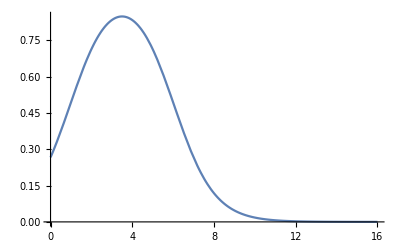

```mathematica
(*Define the crater landscape*)
hc[d_]:=1/(1+N[Exp[1(d-6)]])-1/(1+N[Exp[1(d-1)]]);
Plot[hc[x],{x,0,l}]
response=hc[Total[#]]&/@ sequences;
```

## Comparison between ME interpolation and regression models - Figure 2

### Out-of-sample predictions by the minimum epistasis interpolation

```mathematica
hd=HammingDistance[ConstantArray[0,l],#]&/@sequences;
seqbyhd=Table[Flatten[Position[hd,d]],{d,0,l}];
seqsbyD=GatherBy[Transpose@{HammingDistance[#,ConstantArray[0,l]]&/@sequences,sequences},First][[All,All,2]];
hdsub=Flatten@Table[RandomSample[seq2pos/@seqsbyD[[i]],1],{i,lg@seqsbyD}];
```

```mathematica
(*We give minimum epistasis interpolation 1%, 10%, 50% and 90% of all data as training and use the rest of the data as test*)
training=Table[RandomSample[Range[alpha^l],Ceiling[i alpha^l]],{i,{.01,.1,.5,.9}}];
test=Table[Complement[Range[alpha^l],training[[i]]]//Flatten,{i,4}];
Do[If[Intersection[test[[i]],seqbyhd[[j]]]=={},test[[i]] = Union[test[[i]],{hdsub[[j]]}]],{j,lg@hdsub},{i,lg@test}]
training=Table[Complement[Range[alpha^l],test[[i]]]//Flatten,{i,Length[test]}];
```

```mathematica
pdMEI=Table[Cinterp[training[[i]],response[[training[[i]]]]],{i,4}];
```

### 100% data regressions vs interpolation

```mathematica
(*We fit the three regression models to all the data using ordinary least squares. We implement it by projecting the response vector into the eigenspaces up to the 1st,2nd,or 3rd order using the projection matrix W_0 + ... W_k, for k=1,2,3*)
pd1Way100percent=SprsinLnBy[response,Inverse[LPs].(wkd[[All,;;2]].ConstantArray[1,2])];
pd2Way100percent=SprsinLnBy[response,Inverse[LPs].(wkd[[All,;;3]].ConstantArray[1,3])];
pd3Way100percent=SprsinLnBy[response,Inverse[LPs].(wkd[[All,;;4]].ConstantArray[1,4])];

(*Analytical formula for leave-one-out prediction by Minimum Epistasis Interpolation for a sequence at distance d to WT based on function f*)
loohc[d_,f_]:=2*1/(l(alpha-1))(d f[Abs[d-1]]+d(alpha-2)f[d]+(l-d)(alpha-1)f[d+1])-(Binomial[d,2]f[Abs[d-2]]+(d(l-d)(alpha-1)+Binomial[d,2](alpha-2)^2)f[d]+Binomial[l-d,2](alpha-1)^2 f[d+2])/(Binomial[l,2])

(*Leave-one-out prediction using Minimum epistasis interpolation*)
pdMELOO=Smooth[response];
```

### Figure 2

```mathematica
ticklabsize=14;
labsize=14;
```

```mathematica
plotdats1=Table[dp@Transpose[{Total[#]&/@sequences[[test[[i]]]],pdMEI[[i]][[test[[i]]]]}],{i,lg@test}];
```

```mathematica
labs1=Table[Style["Interpolation "<>ToString[IntegerPart[100 {.01,.1,.5,.9}[[i]]]]<> "%",FontSize->labsize],{i,4}];
```

```mathematica
plotdats2={dp@Transpose[{Total[#]&/@sequences,pd1Way100percent}],dp@Transpose[{Total[#]&/@sequences,pd2Way100percent}],dp@Transpose[{Total[#]&/@sequences,pd3Way100percent}],dp@Transpose[{Total[#]&/@sequences,pdMELOO}]};
```

```mathematica
labs2={"Additive 100%","Pairwise 100%","Three-way 100%","Interpolation\n leave-one-out"};
labs2=Table[Style[labs2[[i]],FontSize->labsize],{i,4}];
```

```mathematica
xticks=Range[0,l+1,4];
yticks=Range[-6,6,1];
tk={{#,Style[Text[#]],{.02,0}}&/@xticks,{#,Style[Text[#]],{.02,0}}&/@yticks};
ticks=ConstantArray[tk,4];
```

```mathematica
pr={{0,l+1},{-.8,2}};
```

```mathematica
as=6(pr[[2,2]]-pr[[2,1]])/17;
```

```mathematica
axstyle1=Join[{{Transparent,Automatic}},ConstantArray[{Transparent,Transparent},3]];
tkstyle1=Join[{{Transparent,Automatic}},ConstantArray[{Transparent,Transparent},3]];
axstyle2=Join[{{Automatic,Automatic}},ConstantArray[{Automatic,Transparent},3]];
tkstyle2=Join[{{Automatic,Automatic}},ConstantArray[{Automatic,Transparent},3]];
```

```mathematica
fig2=Rasterize[Grid[{{Labeled[Labeled[Grid[{Table[Show[ListPlot[plotdats1[[i]],PlotRange->pr,BaseStyle->{FontSize-> ticklabsize},PlotStyle->{PointSize[.02],Black},AspectRatio->as,PlotRangeClipping->False,Ticks->ticks[[i]],AxesStyle->axstyle1[[i]],TicksStyle->tkstyle1[[i]],Epilog->Inset[labs1[[i]],{8,1.8}],ImageSize->{200,Automatic}],
Plot[hc[x],{x,0,l},PlotStyle->Gray,PlotRange->All,Exclusions->None]],{i,4}]}],Style["Fitness",FontFamily->"Helvetica",FontSize->labsize+1],Left,RotateLabel->True],Style["\n A",FontFamily->"Helvetica",FontSize->labsize+4],{{Left,Top}}]},{Labeled[Labeled[Grid[{Table[Show[ListPlot[plotdats2[[i]],PlotRange->pr,BaseStyle->{FontSize-> ticklabsize},PlotStyle->{PointSize[.02],Black},AspectRatio->as,PlotRangeClipping->False,Ticks->ticks[[i]],AxesStyle->axstyle2[[i]],TicksStyle->tkstyle2[[i]],Epilog->Inset[labs2[[i]],{8,1.8}],ImageSize->{200,Automatic},AxesOrigin->{0,-.8}],
Plot[hc[x],{x,0,l},PlotStyle->Gray,PlotRange->All,Exclusions->None]],{i,4}]}],{Style["Fitness",FontFamily->"Helvetica",FontSize->labsize+1],Style["Hamming distance to WT",FontFamily->"Helvetica",FontSize->labsize+1]},{Left,Bottom},RotateLabel->True],Style["\n B",FontFamily->"Helvetica",FontSize->labsize+4],{{Left,Top}}]}}],RasterSize->2000]
```

-Graphics-

```mathematica
Export["Figure2.pdf",fig2];
```

## Behavior of ME interpolation with increasing sequencing length - Figure S2

### sample sequences

```mathematica
wt=ConstantArray[0,l];
mks=Table[Binomial[l,k](alpha-1)^k,{k,0,l}];
```

```mathematica
(*If no seq left in distance class, We randomly choose one to exclude in the training set*)
hd=HammingDistance[ConstantArray[0,l],#]&/@sequences;
weights=hd/.associate[Range[0,l],mks^(-1)];
tr=RandomSample[weights->Range[alpha^l],10000];
```

```mathematica
tr=Complement[tr,seq2pos/@Table[Permute[PadRight[ConstantArray[1,d],l],RandomPermutation[l]],{d,0,l}]];
lg@tr
```

49

```mathematica
seqs=sequences[[tr]];
```

```mathematica
dvec=HammingDistance[#,ConstantArray[0,l]]&/@seqs;
```

### l=16

```mathematica
seqstr=PadRight[#,l]&/@seqs;
```

```mathematica
l=16;
```

```mathematica
y=hc[#]&/@dvec;
```

```mathematica
seqstest=Flatten[Table[Table[Permute[PadRight[ConstantArray[1,d],l],RandomPermutation[l]],20],{d,0,l}],1];
seqstest=Complement[seqstest,seqstr];
```

```mathematica
tr=seq2pos/@seqstr;
ts=seq2pos/@seqstest;
sol=Cinterp[tr,y][[ts]];;
```

```mathematica
Transpose[{Total[#]&/@seqstest,sol}] >> "plotdat16.m"
```

### l>16

```mathematica
lengths={16,17,18,19,20,22,25,30,50,100};
```

```mathematica
Do[{
l=lengths[[i]];
seqstr=Table[Insert[seqs[[i]],0,{#}&/@RandomChoice[Range[16],l-16]],{i,Length[seqs]}];wkd=Table[w[k,d],{d,0,l},{k,0,l}];KIentries=wkd.Join[{0,0},Table[1/((alpha k)^2-alpha(alpha k)),{k,2,l}]]//N;hdm=ConstantArray[ConstantArray[{},Length[seqstr]],Length[seqstr]];Do[hdm[[i,j]]=hdm[[j,i]]=HammingDistance[seqstr[[i]],seqstr[[j]]],{i,lg@seqstr},{j,i}];Kbb=hdm/.associate[Range[0,l],KIentries];seqstest=Flatten[Table[Table[Permute[PadRight[ConstantArray[1,d],l],RandomPermutation[l]],20],{d,0,l}],1];
seqstest=Complement[seqstest,seqstr];Kib=Table[HammingDistance[i,j],{i,seqstest},{j,seqstr}]/.associate[Range[0,l],KIentries];nulltr=SparseArray[Flatten[Table[Join[Table[designrules[seqstr[[j]],k,ConstantArray[0,l],j],{k,0,1}]],{j,Length[seqstr]}],2],{Length[seqstr],Total@Table[Binomial[l, k]*(alpha - 1)^k,{k,0,1}]}];nulltest=SparseArray[Flatten[Table[Join[Table[designrules[seqstest[[j]],k,ConstantArray[0,l],j],{k,0,1}]],{j,Length[seqstest]}],2],{Length[seqstest],Total@Table[Binomial[l, k]*(alpha - 1)^k,{k,0,1}]}];beta=LinearSolve[Transpose[nulltr].Kbb.nulltr,Transpose[nulltr].Kbb.y];epsilon=10^-4;alph=LinearSolve[Kbb,y-nulltr.beta];sol=Kib.alph+nulltest.beta;
Export[StringJoin["plotdat",ToString[lengths[[i]]],".m"],Transpose[{Total[#]&/@seqstest,sol}]];
},{i,Length[lengths]}];//abt
```

### Plotting

```mathematica
plotdats=Table[Import[StringJoin["plotdat",ToString[n],".m"]],{n,lengths}];
```

```mathematica
prs={{{0,17},{-1.1,1.1}},{{0,18},{-1.1,1.1}},{{0,19},{-1.1,1.1}},{{0,20},{-1.1,1.1}},{{0,21},{-1.1,1.1}},{{0,23},{-2.0028923457188545,1.0014461728594273}},{{0,26},{-2.264139173421314,1.132069586710657}},{{0,31},{-2.264139173421314,1.132069586710657}},{{0,51},{-4.441196070941809,2.2205980354709043}},{{0,101},{-8.795309865982796,4.397654932991398}}};
as=Table[6(prs[[i]][[2,2]]-prs[[i]][[2,1]])/(lengths[[i]]+1),{i,lg@prs}];
r=.5;
```

```mathematica
steps={1,2,5,10,20};
maketicks[min_,max_]:=Module[{s,ticks},s=First@Select[steps,IntervalMemberQ[Interval[{3,8}],Total@Boole[IntervalMemberQ[Interval[{min,max}],#]&/@Range[-100,100,#]]]&];
ticks=Range[Floor[min],Ceiling[max],s]
]
```

```mathematica
tks=Table[{maketicks[0,lengths[[i]]+1],maketicks[prs[[i]][[2]][[1]],prs[[i]][[2]][[2]]]},{i,lg@prs}];
ticks=Table[{{#,Style[Text[#]],{.02,0}}&/@tks[[i]][[1]],{#,Style[Text[#]],{.02,0}}&/@tks[[i]][[2]]},{i,lg@tks}];
```

```mathematica
labsize=14;
ticklabsize=14;
```

```mathematica
hc[d_]:=1/(1+N[Exp[1(d-6)]])-1/(1+N[Exp[1(d-1)]]);
```

```mathematica
FigureS2=Labeled[Grid[ArrayReshape[Table[Show[ListPlot[plotdats[[i]],AspectRatio->as[[i]],PlotRange->prs[[i]],BaseStyle->{FontSize->ticklabsize},PlotStyle->{PointSize[.02],Black},Ticks->ticks[[i]],PlotRangeClipping->False,PlotRangePadding->.05,PlotLabel->Style["l="<>ToString[lengths[[i]]],FontSize->labsize,Black],ImageSize->{Automatic,180}],Plot[hc[x],{x,0,lengths[[i]]+10},PlotStyle->Gray,PlotRange->All]],{i,{1,2,3,4,7,8,9,10}}],{2,4}]],{"Fitness","Hamming Distance to WT"},{Left,Bottom},LabelStyle->Directive[FontFamily->"Helvetica"],RotateLabel->True];
```

```mathematica
Export["FigureS2.pdf",Rasterize[%,RasterSize->2000]];
```

## Comparison between ME interpolation and regression models - simulated mutagenesis - Figure S3

### Define the crater landscape

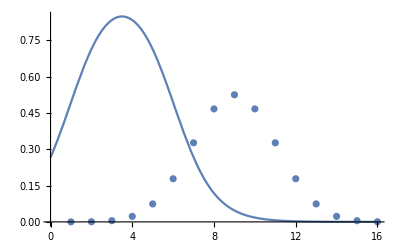

```mathematica
l=16;
hc[d_]:=1/(1+N[Exp[1(d-6)]])-1/(1+N[Exp[1(d-1)]]);
Show[Plot[hc[x],{x,0,l}],ListPlot[Normalize@Table[Binomial[l,k],{k,0,l}]]]
response=hc[Total[#]]&/@ sequences;
noise=RandomVariate[NormalDistribution[0,.2],alpha^l];
response=response+noise;
```

```mathematica
proportions={.01,.1,.5,.9};
```

### Sampling

```mathematica
hd=HammingDistance[ConstantArray[0,l],#]&/@sequences;
seqbyhd=Table[Flatten[Position[hd,d]],{d,0,l}];
seqsbyD=GatherBy[Transpose@{HammingDistance[#,ConstantArray[0,l]]&/@sequences,sequences},First][[All,All,2]];
hdsub=Flatten@Table[RandomSample[seq2pos/@seqsbyD[[i]],1],{i,lg@seqsbyD}];
```

```mathematica
p=.2;
weights=(1-p)^(-#+l) p^# &/@hd;
```

```mathematica
(*We give minimum epistasis interpolation 1%, 10%, 50% and 90% of all data as training and use the rest of the data as test*)
training=Table[RandomSample[weights->Range[alpha^l],Ceiling[i alpha^l]],{i,proportions}];
test=Table[Complement[Range[alpha^l],training[[i]]]//Flatten,{i,Length[proportions]}];
```

```mathematica
(*(*If there is zero seq in the held out data in a distance class,we choose one random sequence to be held out*)*)
Do[If[Intersection[test[[i]],seqbyhd[[j]]]=={},test[[i]] = Union[test[[i]],{hdsub[[j]]}]],{j,lg@hdsub},{i,lg@test}]
(*Do[Do[test[[i]]=Union[test[[i]],hdsub],{k,1,l+1}],{i,Length[test]}]*)
```

```mathematica
Table[Tally[HammingDistance[#,sequences[[1]]]&/@sequences[[test[[i]]]]]//Length,{i,Length[proportions]}]
```

{17,17,17,17}

```mathematica
training=Table[Complement[Range[alpha^l],test[[i]]]//Flatten,{i,Length[proportions]}];
```

### Pairwise (This take ~2h to evaluate)

```mathematica
design2way = Table[
   Join[s2dTaylor[sequences[[i]], 0, ConstantArray[0,l]], 
    s2dTaylor[sequences[[i]], 1, ConstantArray[0,l]],s2dTaylor[sequences[[i]], 2, ConstantArray[0,l]]], {i, Length[sequences]}];//AbsoluteTiming
```

{38.2749,Null}

```mathematica
lambdas=Table[10^k,{k,Range[-5,2,.5]}];
```

```mathematica
crossval2way=Table[Crossvalidation[design2way[[training[[i]]]],response[[training[[i]]]],lambdas,10],{i,Length[training]}];//AbsoluteTiming
bestlambdas=Table[CV[crossval2way[[i]],lambdas][[1]],{i,Length[crossval2way]}];
```

```mathematica
pd2way=Table[design2way.RidgeRegression[design2way[[training[[i]]]],response[[training[[i]]]],bestlambdas[[i]]],{i,Length[proportions]}];//AbsoluteTiming
```

{5.12626,Null}

### Three-way (This take ~2h to evaluate)

```mathematica
design3way = Table[
   Join[s2dTaylor[sequences[[i]], 0, ConstantArray[0,l]], 
    s2dTaylor[sequences[[i]], 1, ConstantArray[0,l]],s2dTaylor[sequences[[i]], 2, ConstantArray[0,l]],s2dTaylor[sequences[[i]], 3, ConstantArray[0,l]]], {i, Length[sequences]}];//AbsoluteTiming
```

{231.337,Null}

```mathematica
crossval3way=Table[Crossvalidation[design3way[[training[[i]]]],response[[training[[i]]]],lambdas,10],{i,Length[training]}];//AbsoluteTiming
bestlambdas=Table[CV[crossval3way[[i]],lambdas][[1]],{i,Length[crossval3way]}];
```

```mathematica
pd3way=Table[design3way.RidgeRegression[design3way[[training[[i]]]],response[[training[[i]]]],bestlambdas[[i]]],{i,Length[proportions]}];//AbsoluteTiming
```

### Interpolation

```mathematica
pdMEI=Table[Cinterp[training[[i]],response[[training[[i]]]]],{i,Length[proportions]}];
```

### Plotting

```mathematica
labsize=14;
ticklabsize=14;
```

```mathematica
hc[d_]:=1/(1+N[Exp[1(d-6)]])-1/(1+N[Exp[1(d-1)]]);
plotdat={pdMEI,pd2way,pd3way};
```

```mathematica
pr=Table[{{0,l+1},{Flatten@plotdat[[k]]//Min,Flatten@plotdat[[k]]//Max}+{-.1,.1}},{k,3}];
pr[[1]][[2]]={-1.4,1.3};
pr[[3]][[2]]={-7.5,6};
as=Table[6(pr[[k,2,2]]-pr[[k,2,1]])/17,{k,3}];
```

```mathematica
names={"Interpolation ","Pairwise ","Three-way "};
```

```mathematica
labs=Table[Style[names[[k]]<>ToString[IntegerPart[100 proportions[[i]]]]<> "%",FontSize->labsize],{k,3},{i,lg@proportions}];
```

```mathematica
labpos={{8,1.2},{8,1.2},{8,5.5}};
```

```mathematica
xticks=Range[0,l+1,4];
yticks=Range[-10,6,1];
tk={{#,Style[Text[#]],{.02,0}}&/@xticks,{#,Style[Text[#]],{.02,0}}&/@yticks};
ticks=ConstantArray[tk,4];
```

```mathematica
axstyle=Join[{{Transparent,Automatic}},ConstantArray[{Transparent,Transparent},3]];
tkstyle=Join[{{Transparent,Automatic}},ConstantArray[{Transparent,Transparent},3]];
```

```mathematica
axstyle=Join[ConstantArray[Join[{{Transparent,Automatic}},ConstantArray[{Transparent,Transparent},3]],2],{Join[{{Automatic,Automatic}},ConstantArray[{Automatic,Transparent},3]]}];
```

```mathematica
plotdat1=Table[Table[Rasterize[Show[ListPlot[Transpose[{Total[#]&/@sequences[[test[[i]]]],plotdat[[k]][[i]][[test[[i]]]]}],BaseStyle->{FontSize->ticklabsize},PlotRange->pr[[k]],PlotStyle->{PointSize[.02],Black},AspectRatio->as[[k]],PlotRangeClipping->False,Axes->True,Ticks->ticks[[i]],Epilog->Inset[labs[[k,i]],labpos[[k]]],ImageSize->{200,Automatic},ImagePadding->{{Automatic,0},{16,10}},AxesStyle->axstyle[[k]][[i]],AxesOrigin->{0,-7.5}],
Plot[hc[x],{x,0,l},PlotStyle->Gray],ImageMargins->0],RasterSize->400,ImageSize->{200,Automatic}],{i,lg@training}],{k,3}];
```

```mathematica
fractionbyD=Table[PadLeft[PadRight[Sort[Tally[HammingDistance[wt,#]&/@sequences[[training[[i]]]]]][[All,2]],l],l+1]/mks,{i,lg@training}];
labsfrac=Table[Style[(*"Fraction sampled "<>*)ToString[IntegerPart[100 proportions[[i]]]]<> "%",FontSize->labsize],{i,lg@proportions}];
axstylefrac=Join[{{Automatic,Automatic}},ConstantArray[{Automatic,Transparent},3]];
```

```mathematica
plotdat2=Table[Rasterize[ListPlot[Transpose@{Range[0,l],fractionbyD[[i]]},PlotRange->{{0,17},{0,1.3}},BaseStyle->{FontSize->ticklabsize},PlotStyle->{PointSize[.02],Black},PlotRangeClipping->False,Ticks->{{#,Style[Text[#]],{.02,0}}&/@Range[0,l+1,5],{#,Style[Text[#/.{0.->0,1.->1}],FontSize->12],{.02,0}}&/@Range[0,1,.5]},Epilog->Inset[labsfrac[[i]],{8,1.2}],ImageSize->{200,Automatic},AxesStyle->axstylefrac[[i]],Filling->Axis],RasterSize->400,ImageSize->{200,Automatic}],{i,lg@fractionbyD}];
```

```mathematica
FigureS3=Labeled[Grid[{{Labeled[Labeled[Grid[{plotdat2},Spacings->0],Style["Fraction",FontFamily->"Helvetica",FontSize->labsize+1],Left,RotateLabel->True],Style["\n A",FontFamily->"Helvetica",FontSize->14+4],{{Left,Top}},RotateLabel->False]},{Labeled[Labeled[Grid[{plotdat1[[1]]},Spacings->0],Style["Fitness",FontFamily->"Helvetica",FontSize->labsize+1],Left,RotateLabel->True],Style["\n B",FontFamily->"Helvetica",FontSize->14+4],{{Left,Top}},RotateLabel->False]},{Labeled[Labeled[Grid[{plotdat1[[2]]},Spacings->0],Style["Fitness",FontFamily->"Helvetica",FontSize->labsize+1],Left,RotateLabel->True],Style["\n C",FontFamily->"Helvetica",FontSize->14+4],{{Left,Top}},RotateLabel->False]},{Labeled[Labeled[Grid[{plotdat1[[3]]},Spacings->0],Style["Fitness",FontFamily->"Helvetica",FontSize->labsize+1],Left,RotateLabel->True],Style["\n D",FontFamily->"Helvetica",FontSize->14+4],{{Left,Top}},RotateLabel->False]}},Spacings->{0,2}],Style["Hamming distance to WT",FontSize->labsize+1,FontFamily->"Helvetica"],Bottom];
```

```mathematica
Export["FigureS3.pdf",Rasterize[FigureS3,RasterSize->1000]];
```

## Sparse random field landscape

## Set parameters

```mathematica
alpha=4;(* alleles per site *)
l=7;(* length of sequence *)
A=Range[0,alpha-1];(*the alphabet in numbers 0-19*)
sequences=Tuples[A,l];(*list of all sequences*)
seq2pos[seq_]:=FromDigits[seq,alpha]+1;
wt=ConstantArray[0,l];
multiplicities=Table[Binomial[l,k](alpha-1)^k,{k,0,l}];
```

```mathematica
samplesizes=Table[Round[i Length[sequences]],{i,Join[{.01,.05},Range[.1,.9,.1]]}];
```

```mathematica
proportions=samplesizes/(alpha^l);
```

## Functions

### Basic functions

```mathematica
dp[v_]:=v//DeleteDuplicates
uqc[v_]:=v//DeleteDuplicates//Length
lg[v_]:=v//Length
dim[m_]:=m//Dimensions
```

```mathematica
seq2posAA[seqAA_]:=seq2pos[Characters[seqAA]/.AAtoDigitRules]
```

```mathematica
associate0[list_,obj_]:=Table[list[[i]]->obj,{i,Length[list]}]
```

```mathematica
MakeDiagonal[vect_]:= SparseArray[Table[{i,i}->vect[[i]],{i,Length[vect]}]]
```

```mathematica
Nbysum[y_]:=(1/Total[y])*y
Nbyfirst[y_]:=(1/First@y)*y
```

```mathematica
ginv[x_]:=If[N[x]==0.,0,1/x]
```

```mathematica
r2[x_, y_] := Correlation[x, y]^2;
mse[x_, y_] := Mean[(x - y)^2];
maxorder[list_] := 
  Module[{i}, 
   For[i = 1, list[[i ;;]] != ConstantArray[0, Length[list[[i ;;]]]], 
    i++]; i - 1];

(*From sequence to lexicographical position*)

seq2pos[seq_] := FromDigits[seq, alpha] + 1

(*Map a vector of length m to a vector of length alpha^l. "list" contains the lexicographical positions for all sequences in "data"*)MapPartialVal[list_,data_,height_]:=Module[{Ab},Ab=SparseArray[Transpose[{list,Range[1,Length[list]]}]->1,{height,Length[list]}];Ab.data]
```

### Projection operators

```mathematica
Pby[x_,Pcoeffs_]:=Pcoeffs[[1;;maxorder[Pcoeffs]]].NestList[L.#&,x,maxorder[Pcoeffs]-1];
```

```mathematica
Pkby[x_,k_]:=Module[{Pcoeffs},Pcoeffs=Inverse[LPs].wkd[[All,k+1]];Pcoeffs[[1;;maxorder[Pcoeffs]]].NestList[L.#&,x,maxorder[Pcoeffs]-1]];
```

### Regression functions

```mathematica
(*Ridge regression with regularization parameter "Î»" and design matrix "design"*)

RidgeRegression[design_, response_, Î»_] := Module[{cross},
  cross = Transpose[design].design;
  Do[cross[[i, i]] += Î»^2, {i, Length[cross]}];
  LinearSolve[cross,
   Transpose[design].response,
   Method -> {"Krylov", "Method" -> "ConjugateGradient", 
     "Preconditioner" -> "ILU0"}]]

(*Ordinary least square regression*)

OrdinaryRegression[design_, response_] := Module[{cross},
  cross = Transpose[design].design;
  LinearSolve[cross, Transpose[design].response, Method -> "Krylov"]]

(*Build design vector for a sequence using the Taylor encoding*)

s2dTaylor[seq_, order_, wt_] := Module[{seqprime, sub1, sub2, pos},
  seqprime = Mod[seq - wt, alpha];
  sub1 = Subsets[seqprime, {order}];
  sub2 = Table[Join[{i}, sub1[[i]]], {i, Length[sub1]}]; 
  pos = FromDigits[Rest[#] - 1, alpha - 1] + 
      1 + (#[[1]] - 1)*((alpha - 1)^order) & /@ 
    Select[sub2, ! MemberQ[#, 0] &];
  SparseArray[
   Table[pos[[i]] -> 1, {i, 
     Length[pos]}], {Binomial[l, order]*(alpha - 1)^order}]
  ]
(*Build design vector for sequence using the one-hot encoding*)

s2d[seq_, order_] := Module[{sub1, sub2, pos},
  sub1 = Subsets[seq, {order}];
  sub2 = Table[Join[{i}, sub1[[i]]], {i, Length[sub1]}]; 
  pos = FromDigits[Rest[#], alpha] + 
      1 + (#[[1]] - 1)*(alpha^order) & /@ sub2;
  SparseArray[
   Table[pos[[i]] -> 1, {i, 
     Length[pos]}], {Binomial[l, order]*(alpha)^order}]
  ]

designrules[seq_, order_, wt_,j_]:=Module[{seqprime, sub1, sub2, pos},
  seqprime = Mod[seq - wt, alpha];
  sub1 = Subsets[seqprime, {order}];
  sub2 = Table[Join[{i}, sub1[[i]]], {i, Length[sub1]}]; 
  pos = FromDigits[Rest[#] - 1, alpha - 1] + 
      1 + (#[[1]] - 1)*((alpha - 1)^order)+ Total@Table[Binomial[l,k](alpha-1)^(k),{k,0,order-1}]& /@ 
    Select[sub2, ! MemberQ[#, 0] &];
  Table[{j,pos[[i]]} -> 1, {i, 
     Length[pos]}]
  ]
s2dTaylor2[seqs_,order_,wt_]:=Module[{rules},rules=Flatten[Table[Join[Table[designrules[seqs[[j]],k,wt,j],{k,order}]],{j,Length[seqs]}],2];SparseArray[rules,{Length[seqs],Total@Table[Binomial[l, k]*(alpha - 1)^k,{k,order}]}]]

designrulesonehot[seq_, order_,j_]:=Module[{ sub1, sub2, pos},

  sub1 = Subsets[seq, {order}];
  sub2 = Table[Join[{i}, sub1[[i]]], {i, Length[sub1]}]; 
  pos = FromDigits[Rest[#] , alpha ] + 
      1 + (#[[1]]-1 )*((alpha )^order)+ Total@Table[Binomial[l,k](alpha)^(k),{k,0,order-1}]& /@ 
    sub2;
  Table[{j,pos[[i]]} -> 1, {i, 
     Length[pos]}]
  ]
s2donehot[seqs_,order_]:=Module[{rules},rules=Flatten[Table[Join[Table[designrulesonehot[seqs[[j]],k,j],{k,order}]],{j,Length[seqs]}],2];SparseArray[rules,{Length[seqs],Total@Table[Binomial[l, k]*(alpha ^k),{k,order}]}]]
```

### Kernelized regressions

```mathematica
CIby[x_]:={0,-alpha/2,1/2}.NestList[L.#&,x,2](*Similar to C.f, we implement multiplication by a matrix that can be expressed as a polynomial in L using NestList.*)(*coeffsinLn: vector of coefficients for L^n*)
SprsinLnBy[x_,coeffsinLn_]:=coeffsinLn[[1;;maxorder[coeffsinLn]]].NestList[L.#&,x,maxorder[coeffsinLn]-1](*Apply the locally non-epistatic smoother M to a vector*)
Smooth[x_]:=-(1/(Binomial[l,2](alpha-1)^2))CIby[x]+x(*Calculate the average squared epistasic coefficient for a vector x*)
Cnorm[x_]:=(1/(nfaces))x.CIby[x]
```

```mathematica
(*Multiplication by the C matrix defined in the main text. For the matrix by vector multiplication C.f, we evaluate it as {0,-alpha/2,1/2}.{f,L.f,L.L.f} using the function NestList. Note that we have omitted the constant 1/s, since it does not affect the solution to the linear equation*)
(*Minimum epistasis interpolation solver*)
Cinterp[training_,y_]:=Module[{Ai,Ab},Ai=SparseArray[Transpose[{Complement[Range[1,alpha^l],training],Range[1,alpha^l-Length[training]]}]->1,{alpha^l,alpha^l-Length[training]}];Ab=SparseArray[Transpose[{training,Range[1,Length[training]]}]->1,{alpha^l,Length[training]}];(Ai.LinearSolve[Transpose[Ai].CIby[Ai.#]&,-Transpose[Ai].CIby[Ab.y],Method->{"Krylov",Method->"ConjugateGradient",Tolerance->10^-15}])+Ab.y](*Regularized regression with regularization parameter given by "rp". "Ccoeffs" and "Pcoeffs" contain entries for a general cost matrix C (not necessarily the C used in the minimum epistasis interpolation problem) and projection matrix P each of which is represented as the coefficients of a polynomial in L. "Ccoeffs" and "Pcoeffs" for fitting models of different orders are defined below*)
Creg[Ccoeffs_,Pcoeffs_,training_,data_,rp_,var_,startingvector_]:=Module[{Ab,W,Cby,Pby},W=(1/Length[data]) SparseArray[Table[{training[[i]],training[[i]]}->(1/var[[i]]),{i,Length[training]}],{alpha^l,alpha^l}];Ab=SparseArray[Transpose[{training,Range[1,Length[training]]}]->1,{alpha^l,Length[training]}];Cby[x_]:=rp*Ccoeffs[[1;;maxorder[Ccoeffs]]].NestList[L.#&,x,maxorder[Ccoeffs]-1];Pby[x_]:=Pcoeffs[[1;;maxorder[Pcoeffs]]].NestList[L.#&,x,maxorder[Pcoeffs]-1];LinearSolve[(Cby[#]+Pby[W.Pby[#]])&,Pby[W.Ab.data],Method->{"Krylov",Method->"ConjugateGradient","StartingVector"->If[Length[startingvector]==0,ConstantArray[0,alpha^l],startingvector]}]]

(*10-fold crossvalidation using the function Creg*)CrossvalidationC[Ccoeffs_,Pcoeffs_,list_,response_,rps_,variance_,fold_,rep_]:=Module[{size,subsets,r,rpsr},
size=Ceiling[Length[response]/fold]; 
subsets=Partition[RandomSample[Range[1,Length[response]]],size,size,1,{}];r=Table[Table[{},Length[rps]+1],rep];Do[Do[r[[k]][[i+1]]=Creg[Ccoeffs,Pcoeffs,list[[Flatten[Drop[subsets,{k}]]]],response[[Flatten[Drop[subsets,{k}]]]],rps[[i]],variance[[Flatten[Drop[subsets,{k}]]]],{}],{i,Length[rps]}],{k,rep}];Table[mse[r[[k]][[i+1]][[list[[subsets[[k]]]]]],response[[subsets[[k]]]]]
,{k,rep},{i,Length[rps]}]
]

(*Extract best regularization parameter from the crossvalidation outputs*)CV[mse_,rps_]:=Module[{means,ses,min,bestlambda},means=Mean[mse];ses=If[Dimensions[mse][[1]]>1,StandardDeviation[mse]/√(Dimensions[mse][[1]]),ConstantArray[0,Dimensions[mse][[2]]]];min=First[Ordering[means]];bestlambda=rps[[min ]];{bestlambda,means,ses}]
```

### Matrix coefficients

```mathematica
(*Krawtchouk polynomial*)
w[ k_, d_] := alpha^(-l) ∑_(q=0)^Min[k,d] (-1)^q(alpha-1)^(k-q)Binomial[d,q]Binomial[l-d,k-q]
wkd = Table[w[k,d],{d,0,l},{k,0,l}];
```

```mathematica
(*LPs contains entries of L^n defined at d=0,1,...l. For any matrix whose (i,j)-th entry only depends on d(i,j), we can then solve a linear equation for the coefficients*)
B=SparseArray[{i_,i_}->(alpha-1)*l,{l+1,l+1}]-1*(SparseArray[{i_,j_}/;i==j:>(i-1)*(alpha-2),{l+1,l+1}]+SparseArray[{i_,j_}/;i-j==1:>i-1,{l+1,l+1}]+SparseArray[{i_,j_}/;i-j==-1:>(l-j+2)*(alpha-1),{l+1,l+1}]);
LPs=ArrayReshape[{PadRight[{1},l+1],PadRight[{(alpha-1)*l,-1},l+1],Table[MatrixPower[B,i].PadRight[{(alpha-1)*l,-1},l+1],{i,1,l-1}]},{l+1,l+1}]//Transpose;

(*Entries of the pseudo-inverse of the interpolation matrix C*)
KIentries=Table[ReleaseHold[Hold[∑_(k=2)^length (alpha^(-l)  1/(((a k)^2-a(a k))a^length)∑_(q=0)^Min[k,d] (-1)^q(alpha-1)^(k-q)Binomial[d,q]Binomial[l-d,k-q])]/.{length->l,a->alpha}],{d,0,l}];

(*Entries of the cost matrix for pairwise regression*)
C2entries=Table[ReleaseHold[Hold[∑_(k=2)^2 (alpha^(-l)  ∑_(q=0)^Min[k,d] (-1)^q(alpha-1)^(k-q)Binomial[d,q]Binomial[l-d,k-q])]/.{length->l,a->alpha}],{d,0,l}];

(*Entries of the cost matrix for three-way regression*)
C3entries=Table[ReleaseHold[Hold[∑_(k=2)^3 (alpha^(-l)  ∑_(q=0)^Min[k,d] (-1)^q(alpha-1)^(k-q)Binomial[d,q]Binomial[l-d,k-q])]/.{length->l,a->alpha}],{d,0,l}];
(*Entries of the cost matrix for the Additive model*)
P1entries=Table[ReleaseHold[Hold[∑_(k=0)^1 (alpha^(-l)∑_(q=0)^Min[k,d] (-1)^q(alpha-1)^(k-q)Binomial[d,q]Binomial[l-d,k-q])]/.{length->l,a->alpha}],{d,0,l}];

(*Entries of the cost matrix for the Pairwise model*)
P2entries=Table[ReleaseHold[Hold[∑_(k=0)^2 (alpha^(-l)∑_(q=0)^Min[k,d] (-1)^q(alpha-1)^(k-q)Binomial[d,q]Binomial[l-d,k-q])]/.{length->l,a->alpha}],{d,0,l}];

(*Entries of the cost matrix for the Three-way model*)
P3entries=Table[ReleaseHold[Hold[∑_(k=0)^3 (alpha^(-l)∑_(q=0)^Min[k,d] (-1)^q(alpha-1)^(k-q)Binomial[d,q]Binomial[l-d,k-q])]/.{length->l,a->alpha}],{d,0,l}];
(*Coefficients for the interpolation matrix C in L*)
CIinLn=PadRight[{0,-alpha/2,1/2},l+1];

(*Coefficients for the interpolation kernel matrix K in L*)
KIinLn=Inverse[LPs].KIentries;

(*Coefficients for the cost matrix for the Pairwise model in L*)
C2inLn=Inverse[LPs].C2entries;

(*Coefficients for the cost matrix for the Three-way model in L*)
C3inLn=Inverse[LPs].C3entries;

(*Coefficients for the projection matrix for the Three-way model in L*)
P3inLn=Inverse[LPs].P3entries;

(*Coefficients for the projection matrix for the Pairwise model in L*)
P2inLn=Inverse[LPs].P2entries;

(*Coefficients for the projection matrix for the Additive model in L*)
P1inLn=Inverse[LPs].P1entries;
```

### Build matrices

```mathematica
(*Build graph Laplacian of the sequence space. L is a sparse matrix with sparsity = 1 - ((alpha-1)l+1)/(alpha^l). Therefore we'll use it to facilitate fast solution of most linear equations in this notebook*)
MakeLaplacian[A_,l_]:=SparseArray[Join[Table[{i,i}->l(A-1),{i,1,A^l}],Flatten[Table[{i,FromDigits[ReplacePart[IntegerDigits[i-1,A,l],-k->alt],A]+1}->-1,{i,1,A^l},{k,1,l},{alt,Complement[Range[0,A-1],{IntegerDigits[i-1,A,l][[-k]]}]}],2]]]
```

```mathematica
AbsoluteTiming[L=MakeLaplacian[alpha,l];]
```

{3.43573,Null}

```mathematica
MakeAdj[A_,l_]:=SparseArray[Flatten[Table[{i,FromDigits[ReplacePart[IntegerDigits[i-1,A,l],-k->alt],A]+1}->1,{i,1,A^l},{k,1,l},{alt,Complement[Range[0,A-1],{IntegerDigits[i-1,A,l][[-k]]}]}],2]]
```

```mathematica
Adj=MakeAdj[alpha,l];//AbsoluteTiming
```

{3.06014,Null}

## Analysis

```mathematica
samplesizes=Table[Round[i Length[sequences]],{i,Join[{.01,.05},Range[.1,.9,.1],{.95,.99}]}];
```

```mathematica
proportions=samplesizes/(alpha^l);
```

```mathematica
trs=Table[RandomSample[Range[Length[sequences]],samplesizes[[i]]],{i,Length[samplesizes]}];
```

```mathematica
tts=Table[Complement[Range[alpha^l],trs[[i]]],{i,Length[trs]}];
```

#### Generate random FL

```mathematica
designAllonehot=s2donehot[sequences,Range[0,l]];//AbsoluteTiming
```

{34.4038,Null}

```mathematica
m=dim[designAllonehot][[2]];
s=.1;(*set sparsity*)
sigma=1;
nrep=3;
```

```mathematica
fs=Table[Module[{beta},beta=RandomVariate[NormalDistribution[0,1],m];beta[[RandomSample[Range[m],m - Ceiling[s m]]]];designAllonehot.beta + RandomVariate[NormalDistribution[0,sigma],alpha^l]],nrep];
```

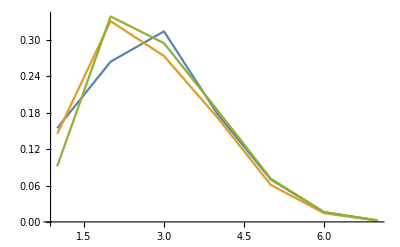

```mathematica
ListLinePlot[Table[Nbysum@Rest[Table[Norm[Pkby[fs[[j]],k]]^2,{k,0,l}]],{j,nrep}],PlotRange->All]
```

```mathematica
pdME=Table[Cinterp[trs[[i]],fs[[j]][[trs[[i]]]]],{j,nrep},{i,lg@trs}];
```

#### L2 regressions

```mathematica
rps2=N@Table[10^i,{i,Range[-20,0,4]}];
rps3=N@Table[10^i,{i,Range[-20,0,4]}];
```

```mathematica
crossval2=Table[{},nrep,lg@trs];
crossval3=Table[{},nrep,lg@trs];
```

```mathematica
var=ConstantArray[1,alpha^l];
```

```mathematica
Do[{crossval2[[i,j]]=CrossvalidationC[C2inLn,P2inLn,trs[[j]],fs[[i]][[trs[[j]]]],rps2,ConstantArray[1,Length[trs[[j]]]],10,10],Print[StringJoin[ToString[i]," ",ToString[j]]]},{j,lg@trs},{i,3}]
```

```mathematica
bestlambdas2=Table[CV[crossval2[[i,j]],rps2][[1]],{i,nrep},{j,lg@trs}];
```

```mathematica
pd2L2=Table[{},3,lg@trs];
```

```mathematica
Do[pd2L2[[i,j]]=Creg[C2inLn,P2inLn,trs[[j]],fs[[i]][[trs[[j]]]],bestlambdas2[[i,j]],var,{}],{i,3},{j,lg@trs}];
```

```mathematica
Do[{crossval3[[i,j]]=CrossvalidationC[C3inLn,P3inLn,trs[[j]],fs[[i]][[trs[[j]]]],rps3,ConstantArray[1,Length[trs[[j]]]],10,10],Print[StringJoin[ToString[i]," ",ToString[j]]]},{j,lg@trs},{i,3}]
```

```mathematica
bestlambdas3=Table[CV[crossval3[[i,j]],rps3][[1]],{i,nrep},{j,lg@trs}];
```

```mathematica
pd3L2=Table[{},3,lg@trs];
```

```mathematica
Do[pd3L2[[i,j]]=Creg[C3inLn,P3inLn,trs[[j]],fs[[i]][[trs[[j]]]],bestlambdas3[[i,j]],var,{}],{i,3},{j,lg@trs}];
```

#### Export files to R

```mathematica
CreateDirectory["SparseRF"];
```

```mathematica
SetDirectory[StringJoin[wd,"/SparseRF"]];
```

```mathematica
Do[Export[StringJoin["tr_",ToString[i],".tsv"],trs[[i]],"TSV"],{i,lg@trs}];
```

```mathematica
Do[Export[StringJoin["f_",ToString[i],".tsv"],fs[[i]],"TSV"],{i,nrep}]
```

```mathematica
rules=Flatten[Table[Join[Table[designrulesonehot[sequences[[j]],k,j],{k,3}]],{j,Length[sequences]}],2];
null3=SparseArray[rules,{Length[sequences],Total@Table[Binomial[l, k]*alpha^k,{k,0,3}]}];
Export["rules.tsv",Transpose@{Most[ArrayRules[null3]][[All,1]][[All,1]],Most[ArrayRules[null3]][[All,1]][[All,2]]},"TSV"];
```

#### Import R outputs

First run R file “SparseRF.R”

```mathematica
pd3L1=Table[{},nrep,lg@trs];
Do[pd3L1[[i,j]]=Flatten@Import[StringJoin["pd_3way_L1_",ToString[i],"_",ToString[j],".tsv"],"TSV"][[2;;,2;;]],{i,nrep},{j,lg@trs}]
```

```mathematica
SetDirectory[wd];
```

#### R2

```mathematica
startpos=2;
```

```mathematica
RME=Table[r2[pdME[[i,j]][[tts[[j]]]],fs[[i]][[tts[[j]]]]],{i,3},{j,startpos,Length[trs]}];
R1=Table[r2[pd1[[i,j]][[tts[[j]]]],fs[[i]][[tts[[j]]]]],{i,3},{j,startpos,Length[trs]}];
R2L2=Table[r2[pd2L2[[i,j]][[tts[[j]]]],fs[[i]][[tts[[j]]]]],{i,3},{j,startpos,Length[trs]}];
R3L2=Table[r2[pd3L2[[i,j]][[tts[[j]]]],fs[[i]][[tts[[j]]]]],{i,3},{j,startpos,Length[trs]}];
R3L1=Table[r2[(pd3L1[[i,j]])[[tts[[j]]]],fs[[i]][[tts[[j]]]]],{i,3},{j,startpos,Length[trs]}];
```

```mathematica
plotdat={Table[{Around[proportions[[i+startpos-1]],0],Around[Mean@RME[[All,i]],StandardDeviation@RME[[All,i]]/Sqrt[nrep]]},{i,Length[trs]-startpos+1}],
Table[{Around[proportions[[i+startpos-1]],0],Around[Mean@R1[[All,i]],StandardDeviation@R1[[All,i]]/Sqrt[nrep]]},{i,Length[trs]-startpos+1}],Table[{Around[proportions[[i+startpos-1]],0],Around[Mean@R2L2[[All,i]],StandardDeviation@R2L2[[All,i]]/Sqrt[nrep]]},{i,Length[trs]-startpos+1}],Table[{Around[proportions[[i+startpos-1]],0],Around[Mean@R3L2[[All,i]],StandardDeviation@R3L2[[All,i]]/Sqrt[nrep]]},{i,Length[trs]-startpos+1}],Table[{Around[proportions[[i+startpos-1]],0],Around[Mean@R3L1[[All,i]],StandardDeviation@R3L1[[All,i]]/Sqrt[nrep]]},{i,Length[trs]-startpos+1}]};
```

```mathematica
ticklength=.02;
```

```mathematica
xticks={#,Text[#],{ticklength,0}}&/@(Range[0,1,.1]/.{0.->0,1.->1});
yticks={#,Text[#],{ticklength,0}}&/@{0,.2,.4,.6,.8,1};
```

```mathematica
colors={Black,Gray,RGBColor@@({51,160,44}/255),RGBColor@@({31,120,180}/255),RGBColor@@({140,180,227}/255)}
```

{GrayLevel[0],GrayLevel[0.5],RGBColor[Rational[1, 5], Rational[32, 51], Rational[44, 255]],RGBColor[Rational[31, 255], Rational[8, 17], Rational[12, 17]],RGBColor[Rational[28, 51], Rational[12, 17], Rational[227, 255]]}

```mathematica
style=Table[{colors[[i]]},{i,5}];
```

```mathematica
fontsize=14;
```

```mathematica
labs={Style["Interpolation",FontFamily->"Helvetica"],Style["Additive",FontFamily->"Helvetica"],Row[{Subscript[Style["L",FontFamily->"Helvetica",Italic],2],Style[" Pairwise",FontFamily->"Helvetica"]}],Row[{Subscript[Style["L",FontFamily->"Helvetica",Italic],2],Style[" Three-way",FontFamily->"Helvetica"]}],Row[{Subscript[Style["L",FontFamily->"Helvetica",Italic],1],Style[" Three-way",FontFamily->"Helvetica"]}]}
```

{Interpolation,Additive,L_2 Pairwise,L_2 Three-way,L_1 Three-way}

```mathematica
fig=Show[ListPlot[plotdat,BaseStyle->{FontSize->16,PointSize[.02]},PlotStyle->style,AspectRatio->1,PlotRange->{{0,1},{0.05,1}},PlotRangePadding->{{0,Scaled[.02]},{0,0}},Frame->True,FrameTicks->{{xticks,False},{yticks,False}},FrameLabel->{"Proportion training data","Out-of-sample "Superscript[R,2]},Joined->False,ClippingStyle->None,ImageSize->350,PlotLegends->Placed[LineLegend[Automatic,labs,LabelStyle->{FontSize->12,GrayLevel[.4]},Spacings->.2],{.2,.86}],FrameStyle->Table[{GrayLevel[.3],Thickness[.002]},4],ImageMargins->10],ListLinePlot[plotdat,PlotStyle->style]];
```

```mathematica
Export["Figure3.pdf",fig];
```

## Protein GB1

A. Download the dataset at https://elifesciences.org/articles/16965/figures#SD1-data by click the link “Download elife-16965-supp1-v4.xlsx“
B. Put file “elife-16965-supp1-v4.csv” in the working directory

### Set parameters

```mathematica
SetDirectory[wd];
alpha=20;(* alleles per site *)
l=4;(* length of sequence *)
A=Range[0,alpha-1];(*the alphabet in numbers 0-19*)
sequences=Tuples[A,l];(*list of all sequences*)
AA={"K","R","H","E","D","N","Q","T","S","C","G","A","V","L","I","M","P","Y","F","W"} (*the alphabet in amino acids*);
AAtoDigitRules=Table[AA[[i]]->i-1,{i,20}] (*convert amino acids to numbers*);
DigitToAARules=Table[i-1->AA[[i]],{i,20}](*convert numbers to amino acids*);
sequencesAA=StringJoin[#/.DigitToAARules]&/@sequences (*list of all possible sequences in amino acids*);
data=Rest[Import["elife-16965-supp1-v4.csv"]]; (*import data*)
logfitness=N[Log[(data[[All,4]]+1/2)/(data[[All,3]]+1/2)]-Log[(data[[1,4]]+1/2)/(data[[1,3]]+1/2)]] (*convert data to logscale with 1/2 as pseudocount to avoid Log[0]. See Wu et al. 2016*);
seq2pos[seq_]:=FromDigits[seq,alpha]+1;(*maps a sequence to its lexicographical order*)
seqlist=(seq2pos[Characters[#]/.AAtoDigitRules])&/@data[[All,1]] (*list of positions for all sequences in the data using lexicographical ordering*);
missing=Complement[Range[1,alpha^l],seqlist]; (*list of positions for all sequences that are missing using lexicographical ordering*)
AB=SparseArray[Transpose[{seqlist,Range[1,Length[seqlist]]}]->1,{alpha^l,Length[seqlist]}]; (*sparse matrix that maps values of all sequences in the data to their lexicographical position. Output is a vector of length alpha^l. *)
responseGB1=AB.logfitness;
var=ConstantArray[1,Length[seqlist]]; (*Constant variance for all sequences*)
variance=N[1/(data[[All,3]]+1/2)+1/(data[[All,4]]+1/2)+1/(data[[1,4]]+1/2)+1/(data[[1,4]]+1/2)];
wt=sequences[[seqlist[[1]]]]; (*sequence of the WT*)
multiplicities=Table[Binomial[l,k](alpha-1)^k,{k,0,l}]; (*multiplicites of eigenvalues lambda_k, k=0,1,...,l*)
nfaces=Binomial[l,2] (Binomial[alpha,2]^2 ) alpha^(l-2);(*Number of faces of the sequence space*)
```

### Functions

```mathematica
r2[x_, y_] := Correlation[x, y]^2;
mse[x_, y_] := Mean[(x - y)^2];
maxorder[list_] := 
  Module[{i}, 
   For[i = 1, list[[i ;;]] != ConstantArray[0, Length[list[[i ;;]]]], 
    i++]; i - 1];

(*From sequence to lexicographical position*)

seq2pos[seq_] := FromDigits[seq, 20] + 1

(*Ridge regression with regularization parameter "λ" and design matrix "design"*)

RidgeRegression[design_, response_, λ_] := Module[{cross},
  cross = Transpose[design].design;
  Do[cross[[i, i]] += λ^2, {i, Length[cross]}];
  LinearSolve[cross,
   Transpose[design].response,
   Method -> {"Krylov", "Method" -> "ConjugateGradient", 
     "Preconditioner" -> "ILU0"}]]

(*Ordinary least square regression*)

OrdinaryRegression[design_, response_] := Module[{cross},
  cross = Transpose[design].design;
  LinearSolve[cross, Transpose[design].response, Method -> "Krylov"]]

(*Build design vector for a sequence using the Taylor encoding*)

s2dTaylor[seq_, order_, wt_] := Module[{seqprime, sub1, sub2, pos},
  seqprime = Mod[seq - wt, alpha];
  sub1 = Subsets[seqprime, {order}];
  sub2 = Table[Join[{i}, sub1[[i]]], {i, Length[sub1]}]; 
  pos = FromDigits[Rest[#] - 1, alpha - 1] + 
      1 + (#[[1]] - 1)*((alpha - 1)^order) & /@ 
    Select[sub2, ! MemberQ[#, 0] &];
  SparseArray[
   Table[pos[[i]] -> 1, {i, 
     Length[pos]}], {Binomial[l, order]*(alpha - 1)^order}]
  ]
(*Build design vector for sequence using the one-hot encoding*)

s2d[seq_, order_] := Module[{sub1, sub2, pos},
  sub1 = Subsets[seq, {order}];
  sub2 = Table[Join[{i}, sub1[[i]]], {i, Length[sub1]}]; 
  pos = FromDigits[Rest[#], alpha] + 
      1 + (#[[1]] - 1)*(alpha^order) & /@ sub2;
  SparseArray[
   Table[pos[[i]] -> 1, {i, 
     Length[pos]}], {Binomial[l, order]*(alpha)^order}]
  ]

designrulesonehot[seq_, order_,j_]:=Module[{ sub1, sub2, pos},

  sub1 = Subsets[seq, {order}];
  sub2 = Table[Join[{i}, sub1[[i]]], {i, Length[sub1]}]; 
  pos = FromDigits[Rest[#] , alpha ] + 
      1 + (#[[1]]-1 )*((alpha )^order)+ Total@Table[Binomial[l,k](alpha)^(k),{k,0,order-1}]& /@ 
    sub2;
  Table[{j,pos[[i]]} -> 1, {i, 
     Length[pos]}]
  ]

s2donehot[seqs_,order_]:=Module[{rules},rules=Flatten[Table[Join[Table[designrulesonehot[seqs[[j]],k,j],{k,order}]],{j,Length[seqs]}],2];SparseArray[rules,{Length[seqs],Total@Table[Binomial[l, k]*(alpha ^k),{k,order}]}]]
(*Design matrix X for fitting nonepistatic models*)

null = Table[
   Join[s2dTaylor[sequences[[i]], 0, wt], 
    s2dTaylor[sequences[[i]], 1, wt]], {i, Length[sequences]}];

(*Krawtchouk polynomial*)
w[ k_, d_] := alpha^(-l) ∑_(q=0)^Min[k,d] (-1)^q(alpha-1)^(k-q)Binomial[d,q]Binomial[l-d,k-q]
wkd = Table[w[k,d],{d,0,l},{k,0,l}];


(*Map a vector of length m to a vector of length alpha^l. "list" contains the lexicographical positions for all sequences in "data"*)
MapPartialVal[list_,data_,height_]:=Module[{Ab},
Ab=SparseArray[Transpose[{list,Range[1,Length[list]]}]->1,{height,Length[list]}];
Ab.data
]

(*Build graph Laplacian of the sequence space. L is a sparse matrix with sparsity = 1 - ((alpha-1)l+1)/(alpha^l). Therefore we'll use it to facilitate fast solution of most linear equations in this notebook*)
MakeLaplacian[A_,l_]:=SparseArray[
Join[Table[{i,i}->l(A-1),{i,1,A^l}],
Flatten[Table[
{i,FromDigits[ReplacePart[IntegerDigits[i-1,A,l],-k->alt],A]+1}->-1,
{i,1,A^l},{k,1,l},{alt,Complement[Range[0,A-1],{IntegerDigits[i-1,A,l][[-k]]}]}],2]]]
AbsoluteTiming[L=MakeLaplacian[alpha,l];]
```

{163.653,Null}

```mathematica
(*Multiplication by the C matrix defined in the main text. For the matrix by vector multiplication C.f, we evaluate it as {0,-alpha/2,1/2}.{f,L.f,L.L.f} using the function NestList. Note that we have omitted the constant 1/s, since it does not affect the solution to the linear equation*)
CIby[x_]:={0,-alpha/2,1/2}.NestList[L.#&,x,2]

(*Similar to C.f, we implement multiplication by a matrix that can be expressed as a polynomial in L using NestList.*)
(*coeffsinLn: vector of coefficients for L^n*)
SprsinLnBy[x_,coeffsinLn_]:=coeffsinLn[[1;;maxorder[coeffsinLn]]].NestList[L.#&,x,maxorder[coeffsinLn]-1]

(*Apply the locally non-epistatic smoother M to a vector*)
Smooth[x_]:=-(1/(Binomial[l,2](alpha-1)^2))CIby[x]+x

(*Calculate the average squared epistasic coefficient for a vector x*)
Cnorm[x_]:=(1/(nfaces))x.CIby[x]

(*Minimum epistasis interpolation solver*)
Cinterp[training_,y_]:=Module[
{Ai,Ab},
Ai=SparseArray[Transpose[{Complement[Range[1,alpha^l],training],Range[1,alpha^l-Length[training]]}]->1,{alpha^l,alpha^l-Length[training]}];
Ab=SparseArray[Transpose[{training,Range[1,Length[training]]}]->1,{alpha^l,Length[training]}];(Ai.LinearSolve[Transpose[Ai].CIby[Ai.#]&,-Transpose[Ai].CIby[Ab.y],Method->{"Krylov",Method->"ConjugateGradient",Tolerance->10^-15}])+Ab.y]

(*Regularized regression with regularization parameter given by "rp". "Ccoeffs" and "Pcoeffs" contain entries for a general cost matrix C (not necessarily the C used in the minimum epistasis interpolation problem) and projection matrix P each of which is represented as the coefficients of a polynomial in L. "Ccoeffs" and "Pcoeffs" for fitting models of different orders are defined below*)
Creg[Ccoeffs_,Pcoeffs_,training_,data_,rp_,var_,startingvector_]:=Module[{Ab,W,Cby,Pby},
W=(1/Length[data]) SparseArray[Table[{training[[i]],training[[i]]}->(1/var[[i]]),{i,Length[training]}],{alpha^l,alpha^l}];
Ab=SparseArray[Transpose[{training,Range[1,Length[training]]}]->1,{alpha^l,Length[training]}];
Cby[x_]:=rp*Ccoeffs[[1;;maxorder[Ccoeffs]]].NestList[L.#&,x,maxorder[Ccoeffs]-1];
Pby[x_]:=Pcoeffs[[1;;maxorder[Pcoeffs]]].NestList[L.#&,x,maxorder[Pcoeffs]-1];
LinearSolve[(Cby[#]+Pby[W.Pby[#]])&,Pby[W.Ab.data],Method->{"Krylov",Method->"ConjugateGradient","StartingVector"->If[Length[startingvector]==0,ConstantArray[0,alpha^l],startingvector]}]
]

(*10-fold crossvalidation using the function Creg*)
CrossvalidationC[Ccoeffs_,Pcoeffs_,list_,response_,rps_,variance_,fold_,rep_]:=Module[{size,subsets,r,rpsr},
size=Ceiling[Length[response]/fold]; 
subsets=Partition[RandomSample[Range[1,Length[response]]],size,size,1,{}];
r=Table[Table[{},Length[rps]+1],rep];
Do[Do[r[[k]][[i+1]]=Creg[Ccoeffs,Pcoeffs,list[[Flatten[Drop[subsets,{k}]]]],response[[Flatten[Drop[subsets,{k}]]]],rps[[i]],variance[[Flatten[Drop[subsets,{k}]]]],r[[k]][[i]]],{i,Length[rps]}],{k,rep}];
Table[mse[r[[k]][[i+1]][[list[[subsets[[k]]]]]],response[[subsets[[k]]]]]
,{k,rep},{i,Length[rps]}]
]

(*Extract best regularization parameter from the crossvalidation outputs*)
CV[mse_,rps_]:=Module[
{means,ses,min,bestlambda},
means=Mean[mse];
ses=If[Dimensions[mse][[1]]>1,StandardDeviation[mse]/√(Dimensions[mse][[1]]),ConstantArray[0,Dimensions[mse][[2]]]];
min=First[Ordering[means]];
bestlambda=rps[[min ]];
{bestlambda,means,ses}
]

(*LPs contains entries of L^n defined at d=0,1,...l. For any matrix whose (i,j)-th entry only depends on d(i,j), we can then solve a linear equation for the coefficients*)
B=SparseArray[{i_,i_}->(alpha-1)*l,{l+1,l+1}]-1*(SparseArray[{i_,j_}/;i==j:>(i-1)*(alpha-2),{l+1,l+1}]+SparseArray[{i_,j_}/;i-j==1:>i-1,{l+1,l+1}]+SparseArray[{i_,j_}/;i-j==-1:>(l-j+2)*(alpha-1),{l+1,l+1}]);
LPs=ArrayReshape[{PadRight[{1},l+1],PadRight[{(alpha-1)*l,-1},l+1],Table[MatrixPower[B,i].PadRight[{(alpha-1)*l,-1},l+1],{i,1,l-1}]},{l+1,l+1}]//Transpose;

(*Entries of the pseudo-inverse of the interpolation matrix C*)
KIentries=Table[ReleaseHold[Hold[∑_(k=2)^length (alpha^(-l)  1/(((a k)^2-a(a k))a^length)∑_(q=0)^Min[k,d] (-1)^q(alpha-1)^(k-q)Binomial[d,q]Binomial[l-d,k-q])]/.{length->l,a->alpha}],{d,0,l}];

(*Entries of the cost matrix for pairwise regression*)
C2entries=Table[ReleaseHold[Hold[∑_(k=2)^2 (alpha^(-l)  ∑_(q=0)^Min[k,d] (-1)^q(alpha-1)^(k-q)Binomial[d,q]Binomial[l-d,k-q])]/.{length->l,a->alpha}],{d,0,l}];

(*Entries of the cost matrix for three-way regression*)
C3entries=Table[ReleaseHold[Hold[∑_(k=2)^3 (alpha^(-l)  ∑_(q=0)^Min[k,d] (-1)^q(alpha-1)^(k-q)Binomial[d,q]Binomial[l-d,k-q])]/.{length->l,a->alpha}],{d,0,l}];
(*Entries of the cost matrix for the Additive model*)
P1entries=Table[ReleaseHold[Hold[∑_(k=0)^1 (alpha^(-l)∑_(q=0)^Min[k,d] (-1)^q(alpha-1)^(k-q)Binomial[d,q]Binomial[l-d,k-q])]/.{length->l,a->alpha}],{d,0,l}];

(*Entries of the cost matrix for the Pairwise model*)
P2entries=Table[ReleaseHold[Hold[∑_(k=0)^2 (alpha^(-l)∑_(q=0)^Min[k,d] (-1)^q(alpha-1)^(k-q)Binomial[d,q]Binomial[l-d,k-q])]/.{length->l,a->alpha}],{d,0,l}];

(*Entries of the cost matrix for the Three-way model*)
P3entries=Table[ReleaseHold[Hold[∑_(k=0)^3 (alpha^(-l)∑_(q=0)^Min[k,d] (-1)^q(alpha-1)^(k-q)Binomial[d,q]Binomial[l-d,k-q])]/.{length->l,a->alpha}],{d,0,l}];
(*Coefficients for the interpolation matrix C in L*)
CIinLn=PadRight[{0,-alpha/2,1/2},l+1];

(*Coefficients for the interpolation kernel matrix K in L*)
KIinLn=Inverse[LPs].KIentries;

(*Coefficients for the cost matrix for the Pairwise model in L*)
C2inLn=Inverse[LPs].C2entries;

(*Coefficients for the cost matrix for the Three-way model in L*)
C3inLn=Inverse[LPs].C3entries;

(*Coefficients for the projection matrix for the Three-way model in L*)
P3inLn=Inverse[LPs].P3entries;

(*Coefficients for the projection matrix for the Pairwise model in L*)
P2inLn=Inverse[LPs].P2entries;

(*Coefficients for the projection matrix for the Additive model in L*)
P1inLn=Inverse[LPs].P1entries;
```

### A. Comparison between the minimum epistasis interpolation and the regression models - Figure4&FigureS4

#### Generate random training data

proportions: proportion of the total sequence assigned as training samples
“rep”: number of replicates for each training sample size

```mathematica
proportions={0.01,0.025,0.05,0.075,0.1,0.125,0.15,0.175,0.2,0.25,0.3,0.4,0.5,0.6,0.7,0.8,0.9,0.924};
rep=3;
samples = Table[Table[RandomSample[Range[1,Length[seqlist]],Ceiling[proportions[[i]]*alpha^l]],rep],{i,Length[proportions]}];
```

#### L2 regularized regression: Choose regularization parameter for pairwise and three-way models by crossvalidation * (this will take ~135hrs to evaluate!)

```mathematica
fold=10;(*10-fold crossvalidation*)
nsubsets=ConstantArray[fold,Length[proportions]];
```

Pairwise model

```mathematica
priorbestlambdas2way={-5.2,-5.7,-5.9,-6.10,-6.2,-6.4,-6.4,-6.4,-6.7,-6.7,-6.7,-6.9,-6.9,-7.10,-7.3,-7.3,-7.1,-7.1};
(*Candidate crossvalidation parameter on Log10 scale for the Pairwise model*)
rps2=Table[10^Range[priorbestlambdas2way[[i]]-1,priorbestlambdas2way[[i]]+1,.2],{i,Length[proportions]}];
TableForm[Table[Join[{proportions[[i]]},Log10@rps2[[i]]],{i,Length[proportions]}],TableSpacing->{1, 1},TableHeadings->{None, {"Proportion","","","","","","Log(λ)"}}]
```

```mathematica
crossval2=Table[Table[{},rep],Length[proportions]];
```

```mathematica
SetSharedVariable[crossval2]
ParallelDo[ crossval2[[i,j]]=CrossvalidationC[C2inLn,P2inLn,seqlist[[samples[[i,j]]]],responseGB1[[seqlist[[samples[[i,j]]]]]],rps2[[i]],var,10,nsubsets[[i]]],{i,1,Length[samples]},{j,1,3}];//AbsoluteTiming
```

```mathematica
bestlambdas2=Table[Table[CV[crossval2[[i,j]],rps2[[i]]],{i,Length[proportions]}][[All,1]],{j,rep}];

(*Plotting best lambda vs. training data proportion*)
ListLinePlot[{Transpose@{proportions,Log10@bestlambdas2[[1]]},Transpose@{proportions,Log10@bestlambdas2[[2]]},Transpose@{proportions,Log10@bestlambdas2[[3]]}}]

Export["bestlambdas2.m",bestlambdas2]
```

Three-way model

```mathematica
priorbestlambdas3way={-4.5,-4.7,-4.9,-5.2,-5.4,-5.4,-5.6,-5.7,-5.7,-5.8,-5.9,-5.9,-6.2,-6.2,-6.2,-6.2,-6.4,-6.4};
(*Candidate crossvalidation parameter on Log10 scale for the Three-way model*)
rps3=Table[10^Range[priorbestlambdas3way[[i]]-1,priorbestlambdas3way[[i]]+1,.2],{i,Length[proportions]}];
TableForm[Table[Join[{proportions[[i]]},Log10@rps3[[i]]],{i,Length[proportions]}],TableSpacing->{1, 1},TableHeadings->{None, {"Proportion","","","","","","Log(λ)"}}]
```

```mathematica
crossval3=Table[Table[{},rep],Length[proportions]];
```

```mathematica
SetSharedVariable[crossval3]
ParallelDo[ crossval3[[i,j]]=CrossvalidationC[C3inLn,P3inLn,seqlist[[samples[[i,j]]]],responseGB1[[seqlist[[samples[[i,j]]]]]],rps3[[i]],var,10,nsubsets[[i]]],{i,1,Length[proportions]},{j,1,3}];//AbsoluteTiming
```

```mathematica
bestlambdas3=Table[Table[CV[crossval3[[i,j]],rps3[[i]]],{i,Length[proportions]}][[All,1]],{j,rep}];

(*Plotting best lambda vs. training data proportion*)
ListLinePlot[{Transpose@{proportions,Log10@bestlambdas3[[1]]},Transpose@{proportions,Log10@bestlambdas3[[2]]},Transpose@{proportions,Log10@bestlambdas3[[3]]}}]

Export["bestlambdas3.m",bestlambdas3]
```

#### L2 regularized regression: Predictions based on cross-validated lambdas* (this will take ~2hrs to evaluate)

```mathematica
(*Best crossvalidated lambdas for training samples used in the paper.
You can use these lambdas if you'd not like to run the crossvalidation step.
If you have run the crossvalidation step,do not run this!*)

bestlambdas2={{6.30957344480193*^-6,1.9952623149688787*^-6,1.2589254117941661*^-6,7.943282347242822*^-7,6.30957344480193*^-7,3.981071705534969*^-7,3.981071705534969*^-7,3.981071705534969*^-7,3.162277660168379*^-7,1.9952623149688787*^-7,1.9952623149688787*^-7,1.2589254117941662*^-7,7.943282347242805*^-8,7.943282347242822*^-8,7.943282347242805*^-8,5.0118723362727144*^-8,5.011872336272725*^-8,5.011872336272725*^-8},{6.30957344480193*^-6,3.162277660168379*^-6,1.2589254117941661*^-6,7.943282347242822*^-7,6.30957344480193*^-7,3.981071705534969*^-7,3.981071705534969*^-7,2.511886431509577*^-7,3.162277660168379*^-7,1.9952623149688787*^-7,1.9952623149688787*^-7,1.2589254117941662*^-7,7.943282347242805*^-8,7.943282347242822*^-8,7.943282347242805*^-8,5.0118723362727144*^-8,5.011872336272725*^-8,5.011872336272725*^-8},{6.30957344480193*^-6,3.162277660168379*^-6,1.2589254117941661*^-6,7.943282347242822*^-7,6.30957344480193*^-7,3.981071705534969*^-7,3.981071705534969*^-7,2.511886431509577*^-7,3.162277660168379*^-7,1.9952623149688787*^-7,1.9952623149688787*^-7,1.2589254117941662*^-7,1.2589254117941662*^-7,7.943282347242822*^-8,7.943282347242805*^-8,5.0118723362727144*^-8,5.011872336272725*^-8,5.011872336272725*^-8}};

bestlambdas3={{0.00007943282347242822,0.000019952623149688786,7.943282347242805*^-6,6.30957344480193*^-6,3.981071705534969*^-6,3.981071705534969*^-6,2.5118864315095823*^-6,1.9952623149688787*^-6,1.9952623149688787*^-6,1.584893192461114*^-6,1.2589254117941661*^-6,1.2589254117941661*^-6,1.*^-6,6.30957344480193*^-7,6.30957344480193*^-7,6.30957344480193*^-7,3.981071705534969*^-7,3.981071705534969*^-7},{0.00031622776601683794,0.000012589254117941661,7.943282347242805*^-6,6.30957344480193*^-6,3.981071705534969*^-6,3.981071705534969*^-6,2.5118864315095823*^-6,1.9952623149688787*^-6,1.9952623149688787*^-6,1.584893192461114*^-6,1.2589254117941661*^-6,1.2589254117941661*^-6,1.*^-6,6.30957344480193*^-7,6.30957344480193*^-7,6.30957344480193*^-7,3.981071705534969*^-7,3.981071705534969*^-7},{7.943282347242822*^-6,7.943282347242822*^-6,0.000012589254117941661,6.30957344480193*^-6,3.981071705534969*^-6,3.981071705534969*^-6,2.5118864315095823*^-6,3.162277660168379*^-6,1.9952623149688787*^-6,1.584893192461114*^-6,1.2589254117941661*^-6,1.2589254117941661*^-6,1.*^-6,6.30957344480193*^-7,6.30957344480193*^-7,6.30957344480193*^-7,3.981071705534969*^-7,3.981071705534969*^-7}};
```

Fit all models. Regularized pairwise and threeway models are fit using the best crossvalidated lambdas

```mathematica
(*
ME:minimum epistasis interpolation
1:additive model
2:pairwise model
3:three-way model*)
pdME=Table[Table[{},rep],Length[proportions]];
pd1=Table[Table[{},rep],Length[proportions]];
pd2=Table[Table[{},rep],Length[proportions]];
pd3=Table[Table[{},rep],Length[proportions]];
Do[pdME[[i,j]]=Smooth[Cinterp[seqlist[[samples[[i,j]]]],responseGB1[[seqlist[[samples[[i,j]]]]]]]],{i,Length[proportions]},{j,rep}];//AbsoluteTiming
Do[pd1[[i,j]]=null.OrdinaryRegression[null[[seqlist[[samples[[i,j]]]]]],responseGB1[[seqlist[[samples[[i,j]]]]]]],{i,Length[samples]},{j,rep}];//AbsoluteTiming
Do[pd2[[i,j]]=Creg[C2inLn,P2inLn,seqlist[[samples[[i,j]]]],responseGB1[[seqlist[[samples[[i,j]]]]]],bestlambdas2[[j,i]],var,{}],{i,Length[samples]},{j,rep}];//AbsoluteTiming
Do[pd3[[i,j]]=Creg[C3inLn,P3inLn,seqlist[[samples[[i,j]]]],responseGB1[[seqlist[[samples[[i,j]]]]]],bestlambdas3[[j,i]],var,{}],{i,Length[samples]},{j,rep}];//AbsoluteTiming
```

{450.172,Null}

{173.309,Null}

{2083.61,Null}

{1920.41,Null}

#### L1 regularized regression: export data to R

```mathematica
CreateDirectory["GB1_L1"];
```

```mathematica
SetDirectory[StringJoin[wd,"GB1_L1"]];
```

```mathematica
rules=Flatten[Table[Join[Table[designrulesonehot[sequences[[j]],k,j],{k,3}]],{j,Length[sequences]}],2];
null3=SparseArray[rules,{Length[sequences],Total@Table[Binomial[l, k]*alpha^k,{k,0,3}]}];
```

```mathematica
Export["rules.tsv",Transpose@{Most[ArrayRules[null3]][[All,1]][[All,1]],Most[ArrayRules[null3]][[All,1]][[All,2]]},"TSV"];
```

training sets

```mathematica
Do[Export[StringJoin["tr_",ToString[i],"_",ToString[j],".tsv"],seqlist[[samples[[i,j]]]],"TSV"],{i,18},{j,3}];
```

response vector

```mathematica
Export["response.tsv",responseGB1,"TSV"];
```

sequence list

```mathematica
Export["seqlist.tsv",seqlist,"TSV"];
```

#### L1 regularized regression: import data from R

Execute “GB1_L1.R”

```mathematica
pdL1=Table[{},18,3];
Do[pdL1[[i,j]]=Flatten@Import[StringJoin["pd_",ToString[i],"_",ToString[j],".tsv"],"TSV"][[2;;,2;;]],{i,18},{j,3}];
```

```mathematica
SetDirectory[wd];
```

#### analysis 1: R squares

```mathematica
(*Out-of-sample,in-sample,and total R^2*)
r2sME=Table[Table[{r2[pdME[[i,j]][[seqlist[[Complement[Range[1,Length[seqlist]],samples[[i,j]]]]]]],responseGB1[[seqlist[[Complement[Range[1,Length[seqlist]],samples[[i,j]]]]]]]],r2[pdME[[i,j]][[seqlist[[samples[[i,j]]]]]],responseGB1[[seqlist[[samples[[i,j]]]]]]],r2[pdME[[i,j]][[seqlist]],responseGB1[[seqlist]]]},{j,3}],{i,Length[proportions]}];
r2s1way=Table[Table[{r2[pd1[[i,j]][[seqlist[[Complement[Range[1,Length[seqlist]],samples[[i,j]]]]]]],responseGB1[[seqlist[[Complement[Range[1,Length[seqlist]],samples[[i,j]]]]]]]],r2[pd1[[i,j]][[seqlist[[samples[[i,j]]]]]],responseGB1[[seqlist[[samples[[i,j]]]]]]],r2[pd1[[i,j]][[seqlist]],responseGB1[[seqlist]]]},{j,3}],{i,Length[proportions]}];
r2s2way=Table[Table[{r2[pd2[[i,j]][[seqlist[[Complement[Range[1,Length[seqlist]],samples[[i,j]]]]]]],responseGB1[[seqlist[[Complement[Range[1,Length[seqlist]],samples[[i,j]]]]]]]],r2[pd2[[i,j]][[seqlist[[samples[[i,j]]]]]],responseGB1[[seqlist[[samples[[i,j]]]]]]],r2[pd2[[i,j]][[seqlist]],responseGB1[[seqlist]]]},{j,3}],{i,Length[proportions]}];
r2s3way=Table[Table[{r2[pd3[[i,j]][[seqlist[[Complement[Range[1,Length[seqlist]],samples[[i,j]]]]]]],responseGB1[[seqlist[[Complement[Range[1,Length[seqlist]],samples[[i,j]]]]]]]],r2[pd3[[i,j]][[seqlist[[samples[[i,j]]]]]],responseGB1[[seqlist[[samples[[i,j]]]]]]],r2[pd3[[i,j]][[seqlist]],responseGB1[[seqlist]]]},{j,3}],{i,Length[proportions]}];
```

```mathematica
r2s3wayL1=Table[Table[{r2[pdL1[[i,j]][[seqlist[[Complement[Range[1,Length[seqlist]],samples[[i,j]]]]]]],responseGB1[[seqlist[[Complement[Range[1,Length[seqlist]],samples[[i,j]]]]]]]],r2[pdL1[[i,j]][[seqlist[[samples[[i,j]]]]]],responseGB1[[seqlist[[samples[[i,j]]]]]]],r2[pdL1[[i,j]][[seqlist]],responseGB1[[seqlist]]]},{j,3}],{i,Length[proportions]}];
```

#### analysis 2: Aveage local epistasis

```mathematica
normME=Table[Cnorm[Smooth[pdME[[i,j]]]],{i,Length[proportions]},{j,rep}];
norm1=Table[Cnorm[pd1[[i,j]]],{i,Length[proportions]},{j,rep}];
norm2=Table[Cnorm[pd2[[i,j]]],{i,Length[proportions]},{j,rep}];
norm3=Table[Cnorm[pd3[[i,j]]],{i,Length[proportions]},{j,rep}];
norm3L1=Table[Cnorm[pdL1[[i,j]]],{i,Length[proportions]},{j,rep}];
```

#### analysis 3: Out-of-sample average local epistasis * (This cell will take ~7hrs to evaluate)

```mathematica
(*Define matrix for calculating squared epistatic coefficient for a given face*)
C4={{1,-1,-1,1},{-1,1,1,-1},{-1,1,1,-1},{1,-1,-1,1}};

FaceSprVec[face_]:=SparseArray[Table[face[[j]]->1,{j,4}],{alpha^l}]

associate[Table1_,Table2_]:=Table[Table1[[i]]->Table2[[i]],{i,Length[Table1]}]

(*Generate a random face*)
rf[rorder_]:=seq2pos/@(#[[rorder]]&/@(Tuples@{{0,1}/.associate[Range[0,alpha-1],RandomSample[Range[0,alpha-1]]],{0,1}/.associate[Range[0,alpha-1],RandomSample[Range[0,alpha-1]]],{0}/.associate[Range[0,alpha-1],RandomSample[Range[0,alpha-1]]],{0}/.associate[Range[0,alpha-1],RandomSample[Range[0,alpha-1]]]}))

SampleSpr[sample_]:=SparseArray[Table[sample[[i]]->1,{i,Length[sample]}],{alpha^l}]
```

```mathematica
(*For each training sample, generate set of random faces that are outside the training data*)
t1facesbysize=Table[{},Length[proportions],3];
Do[t1facesbysize[[i,j]]=
Module[{rfaces,ss,counts},
rfaces=Table[rf[RandomSample[{1,2,3,4}]],10000];
ss=SampleSpr[seqlist[[samples[[i,j]]]]];
counts=Table[ss.FaceSprVec[rfaces[[i]]],{i,Length[rfaces]}];
rfaces[[Flatten@Position[counts,0]]]],
{i,18},{j,3}
];//AbsoluteTiming
```

{353.752,Null}

```mathematica
(*Randomly pick 10,000 faces for each sample*)
t1facesbysizer=Table[t1facesbysize[[i,j]][[RandomSample[Range[Length[t1facesbysize[[i,j]]]],100]]],{i,18},{j,3}];
```

```mathematica
(*Calcualte squared epistatic coefficients for all random faces*)
OSP$ME=Table[Table[pdME[[i,j]][[t1facesbysizer[[i,j,k]]]].C4.pdME[[i,j]][[t1facesbysizer[[i,j,k]]]],{k,10000}],{i,18},{j,3}];
OSP$2=Table[Table[pd2[[i,j]][[t1facesbysizer[[i,j,k]]]].C4.pd2[[i,j]][[t1facesbysizer[[i,j,k]]]],{k,10000}],{i,18},{j,3}];
OSP$3=Table[Table[pd3[[i,j]][[t1facesbysizer[[i,j,k]]]].C4.pd3[[i,j]][[t1facesbysizer[[i,j,k]]]],{k,10000}],{i,18},{j,3}];
OSP$3L=Table[Table[pdL1[[i,j]][[t1facesbysize[[i,j,k]]]].C4.pdL1[[i,j]][[t1facesbysize[[i,j,k]]]],{k,10000}],{i,18},{j,3}];

(*Calculate mean squared epistatic coefficients over all random faces*)
OSP$ME$Mean=Table[Mean@OSP$ME[[i,j]],{i,18},{j,3}];
OSP$2$Mean=Table[Mean@OSP$2[[i,j]],{i,18},{j,3}];
OSP$3$Mean=Table[Mean@OSP$3[[i,j]],{i,18},{j,3}];
OSP$3L$Mean=Table[Mean@OSP$3L[[i,j]],{i,18},{j,3}];
```

#### analysis 4: Number of local peaks * (This cell will take ~10min to evaluate)

```mathematica
(*Generate list of distance 1 neighbors for all sequences*)
NBlist=Table[Flatten[Table[
FromDigits[ReplacePart[seq,-k->alt],alpha]+1,{k,1,l},{alt,Complement[Range[0,alpha-1],{seq[[-k]]}]}],2],{seq,sequences}];//AbsoluteTiming

LocalPeakQ[seq_,f_]:=Boole[f[[seq2pos[seq]]]>Max[f[[NBlist[[seq2pos[seq]]]]]]];
```

{2.92069,Null}

```mathematica
LocalPeaksME=Table[Table[Flatten@Position[LocalPeakQ[#,pdME[[i,j]]]&/@sequences,1],{j,3}],{i,Length[pdME]}];//AbsoluteTiming
Numberlp$size$ME=Table[Length/@LocalPeaksME[[i]],{i,Length[LocalPeaksME]}];
NumberlpOut$size$ME=Table[Table[Length[Complement[LocalPeaksME[[i,j]],seqlist[[samples[[i,j]]]]]],{j,Length[LocalPeaksME[[i]]]}],{i,18}];

LocalPeaksLinear=Table[Table[Flatten@Position[LocalPeakQ[#,pd1[[i,j]]]&/@sequences,1],{j,3}],{i,Length[pd1]}];//AbsoluteTiming
Numberlp$size$Linear=Table[Length/@LocalPeaksLinear[[i]],{i,Length[LocalPeaksLinear]}];
NumberlpOut$size$Linear=Table[Table[Length[Complement[LocalPeaksLinear[[i,j]],samples[[i,j]]]],{j,3}],{i,18}];

LocalPeaks2way=Table[Table[Flatten@Position[LocalPeakQ[#,pd2[[i,j]]]&/@sequences,1],{j,3}],{i,Length[pd2]}];//AbsoluteTiming
Numberlp$size$2way=Table[Length/@LocalPeaks2way[[i]],{i,Length[LocalPeaks2way]}];
NumberlpOut$size$2way=Table[Table[Length[Complement[LocalPeaks2way[[i,j]],seqlist[[samples[[i,j]]]]]],{j,3}],{i,18}];

LocalPeaks3way=Table[Table[Flatten@Position[LocalPeakQ[#,pd3[[i,j]]]&/@sequences,1],{j,3}],{i,Length[pd3]}];//AbsoluteTiming
Numberlp$size$3way=Table[Length/@LocalPeaks3way[[i]],{i,Length[LocalPeaks3way]}];
NumberlpOut$size$3way=Table[Table[Length[Complement[LocalPeaks3way[[i,j]],seqlist[[samples[[i,j]]]]]],{j,3}],{i,18}];
LocalPeaks3wayL1=Table[Table[Flatten@Position[LocalPeakQ[#,pdL1[[i,j]]]&/@sequences,1],{j,3}],{i,Length[pdL1]}];//AbsoluteTiming
Numberlp$size$3wayL1=Table[Length/@LocalPeaks3wayL1[[i]],{i,Length[LocalPeaks3wayL1]}];
NumberlpOut$size$3wayL1=Table[Table[Length[Complement[LocalPeaks3wayL1[[i,j]],seqlist[[samples[[i,j]]]]]],{j,3}],{i,18}];
```

{131.819,Null}

{116.303,Null}

{112.949,Null}

{124.246,Null}

#### Figure 4 - Model performance for the GB1 combinatorial mutagenesis dataset

```mathematica
Fig4Adat={Table[{Around[proportions[[i]],0],Around[Mean[r2sME[[i,All,1]]],StandardDeviation[r2sME[[i,All,1]]]/Sqrt[rep]]},{i,Length[proportions]}],Table[{Around[proportions[[i]],0],Around[Mean[r2s1way[[i,All,1]]],StandardDeviation[r2s1way[[i,All,1]]]/Sqrt[rep]]},{i,Length[proportions]}],Table[{Around[proportions[[i]],0],Around[Mean[r2s2way[[i,All,1]]],StandardDeviation[r2s2way[[i,All,1]]]/Sqrt[rep]]},{i,Length[proportions]}],Table[{Around[proportions[[i]],0],Around[Mean[r2s3way[[i,All,1]]],StandardDeviation[r2s3way[[i,All,1]]]/Sqrt[rep]]},{i,Length[proportions]}],Table[{Around[proportions[[i]],0],Around[Mean[r2s3wayL1[[i,All,1]]],StandardDeviation[r2s3wayL1[[i,All,1]]]/Sqrt[rep]]},{i,Length[proportions]}]};
```

```mathematica
OPSdat={OSP$ME$Mean,Table[0,Length@proportions,rep],OSP$2$Mean,OSP$3$Mean,OSP$3L$Mean};
```

```mathematica
Fig4Bdat=Table[Table[{Around[proportions[[i]],0],Around[Mean[OPSdat[[k]][[i]]],StandardDeviation[OPSdat[[k]][[i]]]/Sqrt[rep]]},{i,Length[proportions]}],{k,5}];
Fig4Bdat[[1]][[All,2]] = Around[0,0.000001];
```

```mathematica
r2s={r2sME,r2s1way,r2s2way,r2s3way,r2s3wayL1};
norms={normME,norm1,norm2,norm3,norm3L1};
Fig4Cdat=Table[Table[{Around[Mean[r2s[[k]][[i,All,3]]],StandardDeviation[r2s[[k]][[i,All,3]]]/Sqrt[rep]],Around[Mean[norms[[k]][[i]]],StandardDeviation[norms[[k]][[i]]]/Sqrt[rep]]},{i,Length@proportions}],{k,Length@r2s}];
```

```mathematica
Numberlp$size$1way=Table[{1,1,1},18];
npeaks={Numberlp$size$ME,Numberlp$size$1way,Numberlp$size$2way,Numberlp$size$3way,Numberlp$size$3wayL1};
Fig4Ddat=Table[{proportions[[i]],Around[Mean@npeaks[[k]][[i]],StandardDeviation@npeaks[[k]][[i]]/Sqrt[rep]]},{k,Length@npeaks},{i,Length@proportions}];
```

```mathematica
Fig4Edat=Table[Table[{Around[Mean[r2s[[k]][[i,All,1]]],StandardDeviation[r2s[[k]][[i,All,1]]]/Sqrt[rep]],Around[Mean[r2s[[k]][[i,All,2]]],StandardDeviation[r2s[[k]][[i,All,2]]]/Sqrt[rep]]},{i,Length@proportions}],{k,Length@r2s}];
```

```mathematica
plotdats={Fig4Adat,Fig4Bdat,Fig4Cdat,Fig4Ddat,Fig4Edat};
```

```mathematica
colors={Black,Gray,RGBColor@@({51,160,44}/255),RGBColor@@({140,180,227}/255),RGBColor@@({31,120,180}/255)}
```

{GrayLevel[0],GrayLevel[0.5],RGBColor[Rational[1, 5], Rational[32, 51], Rational[44, 255]],RGBColor[Rational[28, 51], Rational[12, 17], Rational[227, 255]],RGBColor[Rational[31, 255], Rational[8, 17], Rational[12, 17]]}

```mathematica
startpos=1;
fontsize=20;
style=Table[{colors[[i]]},{i,5}];
padding=1.05{{55,10},{60,10}};
labelpos=Scaled[{.06,.95}];
```

```mathematica
barst=IntervalMarkersStyle-><|"FenceStyle"->{Thickness[.002]},"FenceWidth"->.006,"WhiskerStyle"->{Thickness[.002]}|>;
```

```mathematica
plotdat=plotdats[[1]];
Fig4A=Labeled[ListPlot[plotdat[[All]],BaseStyle->{FontSize->fontsize-2},AspectRatio->1,PlotStyle->style,PlotRange->{{0,1},{.2,.9}},Frame->True,FrameTicks->{{Range[.1,.9,.1],False},{{0,.2,.4,.6,.8,1},False}},FrameLabel->{"Proportion training data","Out-of-sample "Superscript[R,2]},Joined->True,ClippingStyle->None,ImageSize->300,ImagePadding->padding,IntervalMarkers->"Fences",barst],Style["a",Bold,FontFamily->"Helvetica",FontSize->20],{{Left,Top}}];
```

```mathematica
plotdat=plotdats[[2]];
Fig4B=ListPlot[plotdat[[All,startpos;;]],BaseStyle->{FontSize->fontsize-2},AspectRatio->1,PlotStyle->style,PlotRange->{{0,1},{0.,1.2}},Frame->True,FrameTicks->{{Join[{0},Range[.2,2,.2]/.{1.->1}],False},{{0,.2,.4,.6,.8,1},False}},FrameLabel->{"Proportion training data","Out-of-sample local epistasis"},Joined->True,ClippingStyle->None,PlotRangeClipping->False,ImageSize->300,ImagePadding->padding,IntervalMarkers->"Fences",barst];
Fig4B=Labeled[Fig4B,Style["b",Bold,FontFamily->"Helvetica",FontSize->20],{{Left,Top}}];
```

```mathematica
plotdat=plotdats[[3]];
Fig4C=Show[ListPlot[plotdat[[All,startpos;;]],Joined->True,PlotRange->{{.15,1},{0,1.2}},BaseStyle->{FontSize->fontsize-2},AspectRatio->1,Frame->True,FrameLabel->{"Total " Superscript[R,2] ,"Average local epistasis "},PlotRangeClipping->False,ClippingStyle->None,FrameTicks->{{Join[{0},Range[.2,2,.2]/.{1.->1}],None},{Range[.2,1,.2]/.{1.->1},None}},ImageSize->300,ImagePadding->padding,PlotStyle->style,IntervalMarkers->"Fences",barst],Table[Graphics[Table[{Blend[{GrayLevel[.8],Black},proportions[[i]]],PointSize[.03],Point[plotdat[[k]][[i,All,1]]]},{i,startpos,Length[proportions]}]],{k,5}]];
Fig4C=Labeled[Fig4C,Style["c",Bold,FontFamily->"Helvetica",FontSize->20],{{Left,Top}}];
```

```mathematica
plotdat=plotdats[[4]];
Fig4D=ListPlot[plotdat,PlotRange->{{0,1},{0,70}},Joined->True,BaseStyle->{FontSize->fontsize-2},AspectRatio->1,PlotStyle->style,Frame->True,FrameTicks->{{Range[0,70,10],False},{{0,.2,.4,.6,.8,1},False}},FrameLabel->{"Proportion training data","Number of local peaks"},ClippingStyle->None,ImageSize->300,ImagePadding->padding,IntervalMarkers->"Fences",barst];
Fig4D=Labeled[Fig4D,Style["d",Bold,FontFamily->"Helvetica",FontSize->20],{{Left,Top}}];
```

```mathematica
plotdat=plotdats[[5]];
Fig4E=Show[
ListPlot[plotdat[[All,startpos;;]],Joined->True,PlotRange->{{.22,1},{.22,1}},BaseStyle->{FontSize->fontsize-2},AspectRatio->1,PlotStyle->style,Frame->True,FrameTicks->{{Range[0,1,.1]/.{1.->1},False},{Range[0,1,.1]/.{1.->1},False}},AspectRatio->1,FrameLabel->{"Out-of-sample " Superscript[R,2],"In-sample " Superscript[R,2]},ClippingStyle->None,ImageSize->300,ImageMargins->0,ImagePadding->padding,IntervalMarkers->"Fences",barst],Table[Graphics[Table[{Blend[{GrayLevel[.8],Black},proportions[[i]]],PointSize[.03],Point[plotdat[[k]][[i,All,1]]]},{i,startpos,Length[proportions]}]],{k,5}],Plot[x,{x,0,1},PlotStyle->{Gray,Dashed,Thickness[.002]}]];
Fig4E=Labeled[Fig4E,Style["e",Bold,FontFamily->"Helvetica",FontSize->20],{{Left,Top}}];
```

```mathematica
legp=BarLegend[{Blend[{GrayLevel[.8],Black},#]&,{0,1}},LabelStyle->Directive[GrayLevel[.4],FontSize->14],LegendLayout->"Row",LegendLabel->Style["Proportion training data",GrayLevel[.4],FontFamily->"Helvetica"],LegendMarkerSize->200,LegendMargins->{{-10,0},{5,5}},Ticks->Range[0,1,.2],TicksStyle->GrayLevel[.4],Spacings->-.2,LegendFunction->Framed]
```

```mathematica
legl=LineLegend[colors,{"Interpolation","Additive","Pairwise L2","Three-way L2","Three-way L1"},LabelStyle->{FontSize->14,GrayLevel[.4]},Spacings->.2,LegendFunction->Framed]
```

```mathematica
leg=Grid[{{legl},{legp}},Alignment->Left,Spacings->{0,1}];
```

```mathematica
Grid[{{Fig4A,Fig4B,Fig4C},{Fig4D,leg,Fig4E}},Spacings->{1.2,.8}];
Rasterize[%,RasterSize->2000];
```

```mathematica
Export["Figure4.pdf",%,"PDF"];
```

#### Figure S4 - Enrichment of local peaks out of data

```mathematica
totalpeaks={Numberlp$size$ME,Numberlp$size$2way,Numberlp$size$3way,Numberlp$size$3wayL1};
outsidepeaks={NumberlpOut$size$ME,NumberlpOut$size$2way,NumberlpOut$size$3way,NumberlpOut$size$3wayL1,NumberlpOut$size$ME};
```

```mathematica
(*Calculate Enrichment of local peaks outside data*)
plotdatEnrichment=Table[Table[{proportions[[i]],Around[Mean@(outsidepeaks[[k]][[i]]/totalpeaks[[k]][[i]])/(1-proportions[[i]]),StandardDeviation@((outsidepeaks[[k]][[i]]/totalpeaks[[k]][[i]])/(1-proportions[[i]]))/Sqrt[Length[Numberlp$size$ME[[i]]]]]},{i,Length[proportions]}],{k,4}];
style={{Gray,Thickness[.002]},{Gray,Thickness[.002]},{Gray,Thickness[.002]},{Gray,Thickness[.002]}};
fontsize=20;
plotdat=plotdatEnrichment;
```

```mathematica
labels2=Graphics[{
Inset[lab2,{0.89,1.92}],
Inset[labme,{0.63,0.395},Automatic,{0.26,0.23},{{1.,0.},{0.,1.}}],
Inset[lab32, {0.634, 3.98}],
{Arrowheads[0.02],Arrow[{{0.76,0.45},{0.82,0.76}}]},Arrow[{{0.75, 3.95}, {0.90, 
    3.48}}],{Arrowheads[0.02], Arrow[{{0.72, 4.9}, 
    {0.875, 4.52}}],Inset[lab31, {0.64, 5.08}]}}];
```

```mathematica
FigureS4=Show[ListPlot[plotdatEnrichment,BaseStyle->{FontSize->fontsize-2},PlotStyle->style,PlotRange->{{0,1},{0,5.5}},Joined->True,BaseStyle->{FontSize->16-2},AspectRatio->1,Frame->True,FrameTicks->{{Range[0,6,1],False},{{0,.2,.4,.6,.8,1},False}},FrameLabel->{"Proportion training data","Enrichment of local peaks out of data"},ClippingStyle->None,ImageSize->400,PlotRangeClipping->False],Table[Graphics[Table[{Blend[{Blue,Red},proportions[[i]]],PointSize[.02],Point[{proportions[[i]],Mean@(outsidepeaks[[k]][[i]]/totalpeaks[[k]][[i]])/(1-proportions[[i]])}]},{i,18}]],{k,4}],labels2];
```

```mathematica
Export["FigureS4.pdf",FigureS4];
```

### B. Visualization of GB1 landscape - Figure 5&Figure S5

In this section we visualize the full GB1 landscape imputed with all available data using minimum epistasis interpolation. The pipeline here can be easily modified to visualize other fitness landscapes under a continuous time Markov chain.

The visualization procedure consists of four main steps:
Step 1: Imputation of full landscape
Step 2: Building the transition rate matrix Q
Step 3: Eigendecompostion of the matrix Q
Step 4: Plotting the visualization using eigenvectors of Q as coordinates

#### Visualization Functions

```mathematica
Nbysum[y_]:=(1/Total[y])*y

MakeDiagonal[vect_]:= SparseArray[Table[{i,i}->vect[[i]],{i,Length[vect]}]]

(*Substitution rate from "old" sequence to "new" sequence*)
FixationProb[oldfitness_,newfitness_,c_]:=Module[{S},
S=c*(newfitness-oldfitness);
If[S==0,1,S/(1-E^-S)]
]

(*Transition rate matrix. Time is scaled so that the mutation rate per site is equal to 1.*)
QMatrixMutSparse[c_,fitnessvec_,adj_]:=Module[{output,rules},
rules=Most[ArrayRules[adj]];
output=SparseArray[
Table[rules[[i,1]]-> FixationProb[fitnessvec[[rules[[i,1,1]] ]],fitnessvec[[rules[[i,1,2]] ]],c],
{i,Length[rules]}]
,{Length[adj],Length[adj]}];
output=1/(alpha-1)(-MakeDiagonal[Total/@output]+output)
]

MakeNormalized[vect_,mat_]:=MakeDiagonal[vect^(1/2)].(mat.MakeDiagonal[vect^-(1/2)])

(*Eigendecompostion of Q. "stationary" is the stationary distribution of the Markov chain. "num" specifies the number of eigenvectors to calculate*)
EigenDecompPart[stationary_,Q_,num_]:=Module[{normalized,vals,vecs,invals},
normalized=MakeNormalized[stationary,Q];
{vals,vecs}=Eigensystem[normalized,num,Method->{Automatic,Tolerance->10^-15,MaxIterations->100000}];
Do[vecs[[i]]=Normalize[vecs[[i]]],{i,1,Length[vecs]}];
invals=1/(-vals[[2;;]]);
invals=Prepend[invals,0];
{vals,invals,MatrixForm[Transpose[vecs]],MatrixForm[MakeDiagonal[stationary^(-1/2)]. Transpose[vecs]]}
]
```

#### Step 1. Imputation of full landscape

```mathematica
completelandscapeME=Cinterp[seqlist,logfitness];
mesmooth=Smooth[completelandscapeME];
fitness=mesmooth;
```

#### Step 2. Building the transition rate matrix Q (this will take ~10min to evaluate)

```mathematica
(* Build adjacency matrix*)
MakeAdj[A_,l_]:=SparseArray[
Flatten[Table[
{i,FromDigits[ReplacePart[IntegerDigits[i-1,A,l],-k->alt],A]+1}->1,
{i,1,A^l},{k,1,l},{alt,Complement[Range[0,A-1],{IntegerDigits[i-1,A,l][[-k]]}]}],2]]
Adj=MakeAdj[alpha,l];
```

```mathematica
(*c is the conversion factor that transforms log binding to scaled fitness*)
(*We have chosen c so that the expected fitness at stationarity is equal to the fitness of the wt sequence based on the smoothed landscape*)
c=1.1422;
```

```mathematica
(*Q: rate matrix of the continuous time Markov chain.*)
Qmat=QMatrixMutSparse[c,fitness,Adj];//AbsoluteTiming
```

{239.215,Null}

#### Step 3. Eigendecompostion of Q (this will take ~8min to evaluate)

```mathematica
(*Stationary distribution*)
Stat=Nbysum@Table[E^(c*fitness[[i]]),{i,Length[fitness]}];
```

10.0711

{190.25,Null}

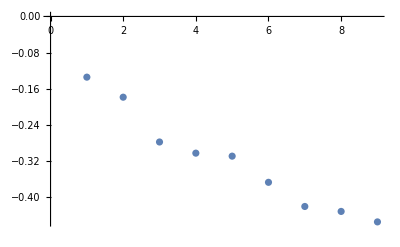

```mathematica
(*For 2-dimensional representation of the GB1 landscape we use as coordinates the right eigenvectors of Q associated with the 2 largest nonzero eigenvalues. Because Q has all nonpositive eigenvalues and the eigendecomposition function returns the eigenvalues and vectors with the largest moduli first, we add a diagonal matrix 2r*I to Q so that 2r*I+Q has all positive eigenvalues and the eigenvalues/vectors of interest will be calculated first. 
2r is a upperbound for the modulus of the leading eigenvalue of Q. So we convert the eigenvalues back by substracting off 2r. 
*)
r=Table[Abs@Qmat[[i,i]],{i,Length[Qmat]}]//Max
Eig=EigenDecompPart[Stat,MakeDiagonal[Table[2r,alpha^l]]+Qmat,10];//AbsoluteTiming
Eigvecs=Replace[Eig[[4]],MatrixForm[a_,___]:>a];
Eigenvals=Rest[Eig[[1]]]-2r;
ListPlot[Eigenvals ]
```

```mathematica
(*Eigenvectors are rescaled by the square root of the associated relaxation time, and these vectors are used as the coordinates for the visualization.*)
Eigvecs2=Eigvecs.MakeDiagonal[Prepend[1/(Sqrt[-Eigenvals]),0]];
coordinates=Eigvecs2[[All,2;;4]];
```

#### Insets (this will take ~10min to evaluate)

```mathematica
colordata=(ColorData["TemperatureMap"][#]&/@Rescale[fitness]);
```

Local peaks

```mathematica
(*Generate list of distance 1 neighbors for all sequences*)
NBlist=Table[Flatten[Table[
FromDigits[ReplacePart[seq,-k->alt],alpha]+1,{k,1,l},{alt,Complement[Range[0,alpha-1],{seq[[-k]]}]}],2],{seq,sequences}];//AbsoluteTiming

LocalPeakQ[seq_,f_]:=Boole[f[[seq2pos[seq]]]>Max[f[[NBlist[[seq2pos[seq]]]]]]];
```

{66.01,Null}

```mathematica
posLP=Flatten@Position[Table[LocalPeakQ[sequences[[i]],fitness],{i,Length[fitness]}],1];
```

Arrows

```mathematica
arrows=Graphics[{{RGBColor[0,0,0], PointSize[0.008], Thickness[0.002], 
   Arrowheads[{{0.01, 1, {GraphicsBox[{EdgeForm[None], Dashing[{}], 
         PolygonBox[{{-1, 0.5}, {0, 0}, {-1, -0.5}}]}], 0.98}}}], 
   EdgeForm[{GrayLevel[0.], Opacity[0.3], AbsoluteThickness[0.2]}], 
   EdgeForm[None], FaceForm[RGBColor[0.178927, 0.305394, 0.933501]], 
   Arrow[{{-3.8495238925178064, 0.7840752695425894}, {-4.0189264262906725, 
    0.6360986945148865}}]}, 
  {{RGBColor[0,0,0], 
    PointSize[0.008], Thickness[0.002], 
    Arrowheads[{{0.01, 1, {GraphicsBox[{EdgeForm[None], Dashing[{}], 
          PolygonBox[{{-1, 0.5}, {0, 0}, {-1, -0.5}}]}], 0.98}}}], 
    EdgeForm[{GrayLevel[0.], Opacity[0.3], AbsoluteThickness[0.2]}], 
    EdgeForm[None], FaceForm[RGBColor[0.178927, 0.305394, 0.933501]], 
    Arrow[{{-4.57449309000487, 0.3369914630693065}, {-4.416363491770526, 
     0.49695807010915516}}]}, {RGBColor[0,0,0], PointSize[0.008], 
    Thickness[0.002], Arrowheads[
     {{0.01, 1, {GraphicsBox[{EdgeForm[None], Dashing[{}], 
          PolygonBox[{{-1, 0.5}, {0, 0}, {-1, -0.5}}]}], 0.98}}}], 
    EdgeForm[{GrayLevel[0.], Opacity[0.3], AbsoluteThickness[0.2]}], 
    EdgeForm[None], FaceForm[RGBColor[0.178927, 0.305394, 0.933501]], 
    Arrow[{{-3.956177252443351, 0.3205389174911913}, {-4.137801947331428, 
     0.4139978599705587}}]}}}];
```

Local peaks

```mathematica
LPplot=Show[Graphics[Prepend[Riffle[colordata[[posLP]],Point/@coordinates[[posLP,{1,2}]]],PointSize[.008]],Frame->False],Table[Graphics[{Thickness[.004],Circle[coordinates[[posLP,{1,2}]][[i]],.045]}],{i,Length[posLP]}]];
```

Wild type

```mathematica
WTplot=Show[Graphics[{colordata[[seq2pos@wt]],PointSize[.008],Point[coordinates[[seq2pos@wt,{1,2}]]]}],
Graphics[{Thickness[.004],GrayLevel[.4],Circle[coordinates[[seq2pos@wt,{1,2}]],.045]}]];
```

Local peak labels

```mathematica
textLP=Graphics[{{Inset[Style["RCSE",LineColor->GrayLevel[0],FrontFaceColor->GrayLevel[0],GraphicsColor->GrayLevel[0],FontSize->12,FontWeight->Bold,FontColor->GrayLevel[0],BackFaceColor->GrayLevel[0]],{-0.35-.04,0.1529}],Inset[Style["VHGC",LineColor->GrayLevel[0],FrontFaceColor->GrayLevel[0],GraphicsColor->GrayLevel[0],FontSize->12,FontWeight->Bold,FontColor->GrayLevel[0],BackFaceColor->GrayLevel[0]],{-3.759+.04,0.273+.02}],Inset[Style["VWGM",LineColor->GrayLevel[0],FrontFaceColor->GrayLevel[0],GraphicsColor->GrayLevel[0],FontSize->12,FontWeight->Bold,FontColor->GrayLevel[0],BackFaceColor->GrayLevel[0]],{-4.908+.03-.28,0.794+.06}],Inset[Style["LICA",LineColor->GrayLevel[0],FrontFaceColor->GrayLevel[0],GraphicsColor->GrayLevel[0],FontSize->12,FontWeight->Bold,FontColor->GrayLevel[0],BackFaceColor->GrayLevel[0]],{2.2380+.05,-4.615}],Inset[Style["LYGV",LineColor->GrayLevel[0],FrontFaceColor->GrayLevel[0],GraphicsColor->GrayLevel[0],FontSize->12,FontWeight->Bold,FontColor->GrayLevel[0],BackFaceColor->GrayLevel[0]],{-4.474-.15,0.794+.05}],Inset[Style["INAA",LineColor->GrayLevel[0],FrontFaceColor->GrayLevel[0],GraphicsColor->GrayLevel[0],FontSize->12,FontWeight->Bold,FontColor->GrayLevel[0],BackFaceColor->GrayLevel[0]],{1.4517+.07,-4.077}],Inset[Style["IWGC",LineColor->GrayLevel[0],FrontFaceColor->GrayLevel[0],GraphicsColor->GrayLevel[0],FontSize->12,FontWeight->Bold,FontColor->GrayLevel[0],BackFaceColor->GrayLevel[0]],{-4.61,0.262}],Inset[Style["WRCA",LineColor->GrayLevel[0],FrontFaceColor->GrayLevel[0],GraphicsColor->GrayLevel[0],FontSize->12,FontWeight->Bold,FontColor->GrayLevel[0],BackFaceColor->GrayLevel[0]],{2.394+.07,-4.4517}],Inset[Style["WWLG",LineColor->GrayLevel[0],FrontFaceColor->GrayLevel[0],GraphicsColor->GrayLevel[0],FontSize->12,FontWeight->Bold,FontColor->GrayLevel[0],BackFaceColor->GrayLevel[0]],{3.649-.6,3.945}]},Inset[Style["WT", LineColor -> GrayLevel[0], FrontFaceColor -> GrayLevel[0], GraphicsColor -> GrayLevel[0], FontSize -> 12, FontWeight -> Bold, FontColor -> GrayLevel[0]],   {-3.7303, 0.83}]}];
```

Ridge labels

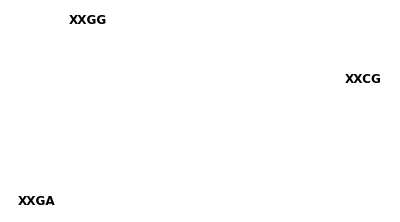
```mathematica
ridgeslabel=-Graphics-;
```

Region polygons

```mathematica
pad=0.02;
pr={{-5.6-pad,3.6+pad},{-5-pad,4.3+pad}};
a1={-2,0};
a2={0,1.5};
a3={1.5,0};
a4={0,-1.5};
marg=.15;
pgRU=Polygon[{a3+{0,marg},a2+{marg,0},{0,4.3}+{marg,0},{3.6,4.3},{3.6,0}+{0,marg}}];
pgRL=Polygon[{a4+{marg,0},{0,-5}+{marg,0},{2.7,-5},{2.7,0}-{0,marg+.1},a3-{0,marg+.1}}];
pgL=Polygon[{{-marg-.06,1.5},{-marg-.06,2},{-5.6-pad,2},{-5.6-pad,-2},{-.8,-2},{-.8,-1.2},{-1.8,-.5},{-1.8,.5}}];
pgs=Graphics[{EdgeForm[GrayLevel[0,.6]],GrayLevel[1],Opacity[0],pgRU,pgRL,pgL}];
```

Brackets XXGA

```mathematica
pos=seq2pos/@Tuples[{A,A,{"G"/.AAtoDigitRules},{"A"/.AAtoDigitRules}}];
pts={{-3.5,-0.7},{-1,-1.8}};
angle=ArcTan[(pts[[1,2]]-pts[[2,2]])/(pts[[1,1]]-pts[[2,1]])];
horizontalpts=RotationTransform[-angle]@pts;
stick={0,.1};
bracket1=Graphics[GeometricTransformation[{Line[horizontalpts],Line[{horizontalpts[[1]],horizontalpts[[1]]+stick}],Line[{horizontalpts[[2]],horizontalpts[[2]]+stick}]},RotationTransform[ angle]],Frame->True];
```

Brackets XXGG

```mathematica
pos=seq2pos/@Tuples[{A,A,{"G"/.AAtoDigitRules},{"G"/.AAtoDigitRules}}];
pts={{-2.8,1.45},{-.3,1.9}};
angle=ArcTan[(pts[[1,2]]-pts[[2,2]])/(pts[[1,1]]-pts[[2,1]])];
horizontalpts=RotationTransform[-angle]@pts;
stick={0,-.1};
bracket2=Graphics[GeometricTransformation[{Line[horizontalpts],Line[{horizontalpts[[1]],horizontalpts[[1]]+stick}],Line[{horizontalpts[[2]],horizontalpts[[2]]+stick}]},RotationTransform[ angle]],Frame->True];
```

Brackets XXCG

```mathematica
pos=seq2pos/@Tuples[{A,A,{"C"/.AAtoDigitRules},{"G"/.AAtoDigitRules}}];
pts={{2.8,.35},{2.8,1.25}};
angle=ArcCot[(pts[[1,1]]-pts[[2,1]])/(pts[[1,2]]-pts[[2,2]])];
horizontalpts=RotationTransform[-angle]@pts;
stick={0,.1};
bracket3=Graphics[GeometricTransformation[{Line[horizontalpts],Line[{horizontalpts[[1]],horizontalpts[[1]]+stick}],Line[{horizontalpts[[2]],horizontalpts[[2]]+stick}]},RotationTransform[ angle]],Frame->True];
```

#### Step 4. Visualization of the GB1 landscape (this will take ~10min to evaluate)

```mathematica
seqtips=StringJoin/@(sequences/.DigitToAARules);
ordering=Reverse@Ordering[coordinates[[All,3]]]; (*order sequences so that high fitness sequences are plotted first*)
colordataordered=(ColorData["TemperatureMap"][#]&/@Rescale[fitness])[[ordering]];
seqtipsordered=seqtips[[ordering]];
```

```mathematica
verts=Graphics[Prepend[Riffle[colordata[[ordering]],Point/@coordinates[[ordering,{1,2}]]],PointSize[.008]],Frame->False];
```

```mathematica
mainplot=Show[GraphPlot[Adj[[All,All]],
VertexCoordinateRules->coordinates[[All,{1,2}]].{{1,0},{0,1}},PlotStyle->{GrayLevel[.6,.05],PointSize->0,Thickness->8 10^-4},Axes->True,AxesStyle->{{Thickness[.001],GrayLevel[0],Arrowheads[.025]},{Thickness[.001],GrayLevel[0],Arrowheads[.025]}},Ticks->{{#,#,{0.005,0.005}}&/@Range[-6,4,1],{#,#,{0.005,0.005}}&/@Range[-5,6,1]},TicksStyle->Directive[FontSize->12],PlotRange->pr,ImageSize->800,PlotRangePadding->{0,.1},ImagePadding->None],verts,pgs,WTplot,LPplot,arrows,textLP,ridgeslabel,bracket1, bracket2, bracket3];
```

```mathematica
mainplotr=Rasterize[mainplot,RasterSize->1000];
```

```mathematica
Export["GB1_visualization.jpg",mainplotr,"JPEG",ImageResolution->500];
```

#### Bar legend

```mathematica
{Min@fitness,Max@fitness}
```

{-7.91578,1.93006}

```mathematica
BarLegend[{ColorData["TemperatureMap"][(#-Min@fitness[[All]])/(Max@fitness[[All]]-Min@fitness[[All]])]&,{Min@fitness[[All]],Max@fitness[[All]]}},LabelStyle->Directive[Black,FontSize->18],LegendMarkerSize->300*2,LegendLayout->"Row"]
```

```mathematica
binwidth=.02;
lb=-8;
ub=2;
```

```mathematica
Rasterize[Show[Module[{dist},dist=BinCounts[fitness,{-8,2,binwidth}];
dist=dist/Total[dist];
Graphics[Table[{EdgeForm[{Thick,Gray}],(ColorData["TemperatureMap"][(#-Min@fitness[[All]])/(Max@fitness[[All]]-Min@fitness[[All]])]&)[Range[-8,2,binwidth][[i]] +binwidth/2],Rectangle[{i+.5,dist[[i]]},{i-.5,0}]},{i,(ub-lb)/binwidth}],AspectRatio->.15
]
],Module[{dist},dist=BinCounts[fitness,{-8,2,binwidth}];
dist=dist/Total[dist];
Graphics[Table[{(*EdgeForm[White],*)(ColorData["TemperatureMap"][(#-Min@fitness[[All]])/(Max@fitness[[All]]-Min@fitness[[All]])]&)[Range[-8,2,binwidth][[i]] +binwidth/2],Rectangle[{i+.5,dist[[i]]},{i-.5,0}]},{i,(ub-lb)/binwidth}],AspectRatio->.2
]
]],RasterSize->1000]
```

-Graphics-

#### Fit individual additive models three regions

```mathematica
On[LinearSolve::luc]
```

```mathematica
(*Fit additive model to subset of sequences*)
FitLinearSubset[design_,sub_,response_]:=Module[{posnonnegcoeffs,designsub,coeffs},
posnonnegcoeffs=Position[Table[design[[sub]][[All,i]].ConstantArray[1,Length[sub]]==0,{i,Dimensions[design][[2]]}],False]//Flatten;
designsub=design[[sub,posnonnegcoeffs]];
coeffs=MapPartialVal[posnonnegcoeffs,OrdinaryRegression[designsub,response[[sub]]],Dimensions[design][[2]]];
{designsub.(coeffs[[posnonnegcoeffs]]),
{coeffs[[1]],ArrayReshape[NumberForm[#,2]&/@Rest[coeffs],{l,alpha}]},Dimensions[designsub],designsub.OrdinaryRegression[designsub,response[[sub]]]-response[[sub]],coeffs}]
```

```mathematica
posRegion1=seq2pos/@Tuples[{A,A,{"G"/.AAtoDigitRules},A}];
posRegion2=Flatten@Position[RegionMember[pgRU,coordinates[[All,{1,2}]]],True];
posRegion3=Flatten@Position[RegionMember[pgRL,coordinates[[All,{1,2}]]],True];
```

```mathematica
posRest=Complement[Range[alpha^l],Union[posRegion1,posRegion3,posRegion2]];
```

```mathematica
Length/@{posRegion1,posRegion2,posRegion3,posRest}
```

{8000,13920,10392,127688}

```mathematica
r2[FitLinearSubset[null,posRegion2,completelandscapeME][[1]],completelandscapeME[[posRegion2]]]
r2[FitLinearSubset[null,posRegion3,completelandscapeME][[1]],completelandscapeME[[posRegion3]]]
r2[FitLinearSubset[null,posRegion1,completelandscapeME][[1]],completelandscapeME[[posRegion1]]]
```

0.774705

0.789242

0.799532

```mathematica
{Min[#],Max[#]}&@Union[FitLinearSubset[null,posRegion1,fitness][[1]],FitLinearSubset[null,posRegion3,fitness][[1]],FitLinearSubset[null,posRegion2,fitness][[1]]]
{Min[#],Max[#]}&@completelandscapeME
```

{-8.77171,1.82183}

{-9.27878,2.16277}

```mathematica
prscatter={{-9.5,2.5},{-9.5,2.5}};
```

```mathematica
XY={FitLinearSubset[null,posRegion1,completelandscapeME][[1]],completelandscapeME[[posRegion1]]};
additivefitRegion1=Rasterize[Show[ListPlot[Transpose[XY],PlotRange->prscatter,BaseStyle->{FontSize->22},PlotStyle->{{GrayLevel[0,.5],PointSize[.01]}},AspectRatio->Automatic,Axes->False,Frame->True,FrameTicks->{{Range[-10,2,2],None},{Range[-10,2,2],None}},FrameLabel->{"Additive Prediction","Log relative binding"},FrameStyle->GrayLevel[0,.6]],Plot[x,{x,-10,10},PlotStyle->Table[{GrayLevel[0,.6],Thickness[.003]},4]],Graphics[Text[R^2==Round[r2@@XY,.01],{-7,1}]]],RasterSize->1000];
Export["additivefitRegion1.pdf",additivefitRegion1];

XY={FitLinearSubset[null,posRegion2,completelandscapeME][[1]],completelandscapeME[[posRegion2]]};
additivefitRegion2=Rasterize[Show[ListPlot[Transpose[XY],PlotRange->prscatter,BaseStyle->{FontSize->22},PlotStyle->{{GrayLevel[0,.5],PointSize[.01]}},AspectRatio->Automatic,Axes->False,Frame->True,FrameTicks->{{Range[-10,2,2],None},{Range[-10,2,2],None}},FrameLabel->{"Additive Prediction","Log relative binding"},FrameStyle->GrayLevel[0,.6]],Plot[x,{x,-10,10},PlotStyle->Table[{GrayLevel[0,.6],Thickness[.003]},4]],Graphics[Text[R^2==Round[r2@@XY,.01],{-7,1}]]],RasterSize->1000];
Export["additivefitRegion2.pdf",additivefitRegion2];

XY={FitLinearSubset[null,posRegion3,completelandscapeME][[1]],completelandscapeME[[posRegion3]]};
additivefitRegion3=Rasterize[Show[ListPlot[Transpose[XY],PlotRange->prscatter,BaseStyle->{FontSize->22},PlotStyle->{{GrayLevel[0,.5],PointSize[.01]}},AspectRatio->Automatic,Axes->False,Frame->True,FrameTicks->{{Range[-10,2,2],None},{Range[-10,2,2],None}},FrameLabel->{"Additive Prediction","Log relative binding"},FrameStyle->GrayLevel[0,.6]],Plot[x,{x,-10,10},PlotStyle->Table[{GrayLevel[0,.6],Thickness[.003]},4]],Graphics[Text[R^2==Round[r2@@XY,.01],{-7,1}]]],RasterSize->1000];
Export["additivefitRegion3.pdf",additivefitRegion3];
```

```mathematica
(*Export fasta file of 5000 random sequences for each region*)
Export["seqsRegion1.fasta",{Range[1,5000],StringJoin[#]&/@(sequences[[RandomSample[posRegion1,5000]]]/.DigitToAARules)},"FASTA"];
Export["seqsRegion2.fasta",{Range[1,5000],StringJoin[#]&/@(sequences[[RandomSample[posRegion2,5000]]]/.DigitToAARules)},"FASTA"];
Export["seqsRegion3.fasta",{Range[1,5000],StringJoin[#]&/@(sequences[[RandomSample[posRegion3,5000]]]/.DigitToAARules)},"FASTA"];
```

#### Permutation p-values for local additive models (this will take ~2hrs to evaluate for n=1000)

```mathematica
(*Set number of permutations*)
n=1000;
```

```mathematica
R2Region1=Table[Module[{sub},
sub=RandomSample[Range[alpha^l],Length[posRegion1]];
r2[FitLinearSubset[null,sub,completelandscapeME][[1]],completelandscapeME[[sub]]]],n];//AbsoluteTiming
R2Region2=Table[Module[{sub},
sub=RandomSample[Range[alpha^l],Length[posRegion2]];
r2[FitLinearSubset[null,sub,completelandscapeME][[1]],completelandscapeME[[sub]]]],n];//AbsoluteTiming
R2Region3=Table[Module[{sub},
sub=RandomSample[Range[alpha^l],Length[posRegion3]];
r2[FitLinearSubset[null,sub,completelandscapeME][[1]],completelandscapeME[[sub]]]],n];//AbsoluteTiming
```

Permutation p-value

```mathematica
r2[FitLinearSubset[null,posRegion1,completelandscapeME][[1]],completelandscapeME[[posRegion1]]];
Total[Boole[#>%]&/@R2Region1 ]/n//N
```

0.

```mathematica
r2[FitLinearSubset[null,posRegion2,completelandscapeME][[1]],completelandscapeME[[posRegion2]]];
Total[Boole[#>%]&/@R2Region2 ]/n//N
```

0.

```mathematica
r2[FitLinearSubset[null,posRegion3,completelandscapeME][[1]],completelandscapeME[[posRegion3]]];
Total[Boole[#>%]&/@R2Region3 ]/n//N
```

0.

#### Figure S5 - Comparison of mean mutation effects between the three high fitness regions in the GB1 visualization

```mathematica
(*Extract effects of all mutations for a focal sequence*)
SingleMutationEffects[seq_,fitness_]:=Module[{effects},effects=Table[Table[fitness[[seq2pos[ReplacePart[seq,k->i]]]],{i,0,alpha-1}]-fitness[[seq2pos[seq]]],{k,1,l}];
effects//Flatten
]
```

```mathematica
mScale[v_]:=v-Max[v];
```

```mathematica
meRegion1=Table[SingleMutationEffects[sequences[[posRegion1[[i]]]],completelandscapeME],{i,Length[posRegion1]}];
meRegion2=Table[SingleMutationEffects[sequences[[posRegion2[[i]]]],completelandscapeME],{i,Length[posRegion2]}];
meRegion3=Table[SingleMutationEffects[sequences[[posRegion3[[i]]]],completelandscapeME],{i,Length[posRegion3]}];
```

```mathematica
MutationEffects={ArrayReshape[Round[#,.1]&/@Mean@meRegion1,{4,20}],ArrayReshape[Round[#,.1]&/@Mean@meRegion2,{4,20}],ArrayReshape[Round[#,.1]&/@Mean@meRegion3,{4,20}]};
```

```mathematica
mufixed=Table[mScale/@MutationEffects[[i]],{i,3}];
```

```mathematica
region2vregion1=Table[
Show[
Plot[x,{x,-7,0},PlotRange->{{-6,.2},{-6,.2}},AspectRatio->1,PlotStyle->{Gray,Thickness[.002],FontSize[12]},Frame->True,FrameTicks->{{Range[-6,.5,2],None},{Range[-6,.5,2],None}},FrameTicksStyle->Directive[Gray,14],FrameLabel->{Style["Amino acid defect - Region 1",FontSize->14],Style["Amino acid defect - Region 2",FontSize->14]},ImageSize->300],Graphics@Table[Text[Style[AA[[i]],FontSize->10],{mufixed[[1]][[site]][[i]],mufixed[[2]][[site]][[i]]}],{i,20}],Graphics[Text[Style[Superscript[R,2] ==Round[r2[mufixed[[1]][[site]],mufixed[[2]][[site]]],.01],FontSize->16],{-4.75,-.5}]]],{site,4}];
```

```mathematica
region3vregion1=Table[
Show[
Plot[x,{x,-7,0},PlotRange->{{-6,.2},{-6,.2}},AspectRatio->1,PlotStyle->{Gray,Thickness[.002],FontSize[12]},Frame->True,FrameTicks->{{Range[-6,.5,2],None},{Range[-6,.5,2],None}},FrameTicksStyle->Directive[Gray,14],FrameLabel->{Style["Amino acid defect - Region 1",FontSize->14],Style["Amino acid defect - Region 3",FontSize->14]},ImageSize->300],Graphics@Table[Text[Style[AA[[i]],FontSize->10],{mufixed[[1]][[site]][[i]],mufixed[[3]][[site]][[i]]}],{i,20}],Graphics[Text[Style[Superscript[R,2] ==Round[r2[mufixed[[1]][[site]],mufixed[[3]][[site]]],.01],FontSize->16],{-4.75,-.5}]],ImageSize->300],{site,4}];
```

```mathematica
region3vregion2=Table[
Show[
Plot[x,{x,-7,0},PlotRange->{{-6,.2},{-6,.2}},AspectRatio->1,PlotStyle->{Gray,Thickness[.002],FontSize[12]},Frame->True,FrameTicks->{{Range[-6,.5,2],None},{Range[-6,.5,2],None}},FrameTicksStyle->Directive[Gray,14],FrameLabel->{Style["Amino acid defect - Region 2",FontSize->14],Style["Amino acid defect - Region 3",FontSize->14]},ImageSize->300],Graphics@Table[Text[Style[AA[[i]],FontSize->10],{mufixed[[2]][[site]][[i]],mufixed[[3]][[site]][[i]]}],{i,20}],Graphics[Text[Style[Superscript[R,2] ==Round[r2[mufixed[[2]][[site]],mufixed[[3]][[site]]],.01],FontSize->16],{-4.75,-.5}]],ImageSize->300],{site,4}];
```

```mathematica
aa={Style["Amino acid \n" ,FontFamily->"Helvetica",FontSize->Scaled[.04]],"",""};
```

Tables of mutational effects by region

```mathematica
(*colorblock[x_,max_,min_]:=Graphics[{Blend[{Blue,White},(x-min)/(max-min)],EdgeForm[Directive[Thin,Gray]],Rectangle[],Inset[Style[ToString[x],Black,FontSize->Scaled[.4]]]}]
style[tex_]:=Style[tex,FontFamily->"Helvetica",FontSize->Scaled[.05]]*)
```

```mathematica
(*tabdat=Table[Table[colorblock[mufixed[[k]][[i,j]],0,Min[Flatten[mufixed]]],{i,4},{j,20}],{k,3}];*)
```

```mathematica
(*FigureS5=Grid[{{Labeled[Show[Rasterize[TableForm[{region2vregion1,region3vregion1,region3vregion2},TableHeadings->{Style[#,FontFamily->"Helvetica",FontSize->14,Black]&/@{"Region 2 vs. Region 1","Region 3 vs. Region 1","Region 3 vs. Region 2"},Style[StringJoin["Site ",ToString[#]],FontFamily->"Helvetica",FontSize->14]&/@{39,40,41,54}},TableAlignments->Center,TableSpacing->4{1, 1}],RasterSize->1000],ImageSize->1000],Style["A  ",FontFamily->"Helvetica",FontSize->18],Left]},{Labeled[Grid[Table[{Rasterize[Labeled[Labeled[TableForm[tabdat[[k]],TableHeadings->{style/@{39,40,41,54},style/@AA},TableSpacing->{0,0},TableAlignments->Center],{Style["Site \n",FontFamily->"Helvetica",FontSize->Scaled[.04]],aa[[k]]},{Left,Top},RotateLabel->True],Style[StringJoin["\n Region",ToString[k],"   "],FontFamily->"Helvetica",FontSize->Scaled[.04]],Left],RasterSize->2000,ImageSize->600]},{k,3}],Spacings->{0,2}],Style["B  ",FontFamily->"Helvetica",FontSize->18],Left]}},Spacings->{1,5}];*)
```

Tables of marginal frequency of amino acids by region

```mathematica
colorblock[x_,max_,min_]:=Graphics[{Blend[{White,White},(x-min)/(max-min)],EdgeForm[Directive[Thin,Gray]],Rectangle[],Inset[Style[ToString[x],Black,FontSize->Scaled[.4]]]}]
style[tex_]:=Style[tex,FontFamily->"Helvetica",FontSize->Scaled[.04]]
```

```mathematica
tabdat=Table[colorblock[Round[ Count[(Transpose@sequences[[region]])[[site]],aa]/Length[region],.01]/.{0.->0,1.->1},0,1],{region,{posRegion1,posRegion2,posRegion3}},{site,4},{aa,A}];
```

```mathematica
FigureS5=Grid[{{Labeled[Show[Rasterize[TableForm[{region2vregion1,region3vregion1,region3vregion2},TableHeadings->{Style[#,FontFamily->"Helvetica",FontSize->14,Black]&/@{"Region 2 vs. Region 1","Region 3 vs. Region 1","Region 3 vs. Region 2"},Style[StringJoin["Site ",ToString[#]],FontFamily->"Helvetica",FontSize->14]&/@{39,40,41,54}},TableAlignments->Center,TableSpacing->4{1, 1}],RasterSize->1000],ImageSize->1000],Style["A  ",FontFamily->"Helvetica",FontSize->18],Left]},{Labeled[Grid[Table[{Rasterize[Labeled[Labeled[TableForm[tabdat[[k]],TableHeadings->{style/@{39,40,41,54},style/@AA},TableSpacing->{0,0},TableAlignments->Center],{Style["Site \n",FontFamily->"Helvetica",FontSize->Scaled[.04]],aa[[k]]},{Left,Top},RotateLabel->True],Style[StringJoin["\n Region",ToString[k],"   "],FontFamily->"Helvetica",FontSize->Scaled[.04]],Left],RasterSize->2000,ImageSize->600]},{k,3}],Spacings->{0,2}],Style["B  ",FontFamily->"Helvetica",FontSize->18],Left]}},Spacings->{1,5}];
```

```mathematica
Export["FigureS5.pdf",Rasterize[FigureS5,RasterSize->2000]];
```

### Regularized minimum epistasis interpolation - Figure S9

```mathematica
sizes={0.01,0.1,.8};
```

```mathematica
nrep=5;
```

```mathematica
trs=Table[Table[RandomSample[seqlist,Round[sizes [[i]] alpha^l ]],nrep],{i,Length@sizes}];
```

```mathematica
lambdas=Table[10^k,{k,Range[-15,2,1]}];
```

```mathematica
outME=Table[Cinterp[trs[[j]][[i]],responseGB1[[trs[[j]][[i]]]]],{j,Length@trs},{i,nrep}];//AbsoluteTiming
```

{90.9023,Null}

```mathematica
out=Table[Creg[PadRight[{0,-alpha/2,1/2},l+1],PadRight[{1},l+1],trs[[j]][[i]],responseGB1[[trs[[j]][[i]]]],lambdas[[k]],var,{}],{j,Length@trs},{i,nrep},{k,Length@lambdas}];//AbsoluteTiming
```

{1041.35,Null}

```mathematica
msetab=Table[mse[responseGB1[[Complement[seqlist,trs[[j]][[i]]]]],out[[j]][[i]][[k]][[Complement[seqlist,trs[[j]][[i]]]]]],{j,Length@trs},{i,nrep},{k,Length@lambdas}];
```

```mathematica
plotdat=Table[Around[Mean[msetab[[j,All,k]]],StandardDeviation[msetab[[j,All,k]]]/Sqrt[nrep]],{j,Length@msetab},{k,Length@lambdas}];
```

```mathematica
startpos=1;
```

```mathematica
ticklabsize=12;
labsize=15;
```

```mathematica
xticks=Table[{i,Style[Superscript[10,i],FontSize->ticklabsize],{0.02,0}},{i,Range[-20,2,2]}];
yticks={Table[{i,Style[i,FontSize->ticklabsize],{0.02,0}},{i,Range[0,2,.02]}],Table[{i,Style[i,FontSize->ticklabsize],{0.02,0}},{i,Range[0,2,.1]}],Table[{i,Style[i,FontSize->ticklabsize],{0.02,0}},{i,Range[0,2,.2]}]};
```

```mathematica
Grid[Table[pr={Min@plotdat[[j]][[startpos;;]][[All,1]],Max@plotdat[[j]][[startpos;;]][[All,1]]} ;
pad=.1Abs[Subtract@@pr];
pr=pr+ {-pad,pad};
{Labeled[Show[ListPlot[Transpose@{Log10@lambdas[[startpos;;]],plotdat[[j]][[startpos;;]]},PlotStyle->Black,BaseStyle->{FontSize->10},PlotRange->{All,pr},Ticks->{xticks,yticks[[j]]},AxesOrigin->{-16,Automatic},PlotRangePadding->Scaled[.05],ImageSize->400,PlotLabel->Style[StringJoin[ToString[IntegerPart[100 sizes[[j]]]], "% ", "trainining"],FontSize->labsize,FontFamily->"Helvetica"]],Plot[Mean@msetabME[[j]],{x,-20,10},PlotStyle->{Gray,Dashed}]],Style[#,FontSize->labsize,FontFamily->"Helvetica"]&/@{"Mean square error",λ},{Left,Bottom},RotateLabel->True]},{j,3}],Spacings->{0, 2}];
```

```mathematica
Export["FigureS9.pdf",Rasterize[%,RasterSize->2000]];
```

### Visualization with raw data - Figure S6

```mathematica
steps={1,2,5,10,20,50,100};
```

```mathematica
maketicks[min_,max_]:=Module[{s,ticks},s=First@Select[steps,IntervalMemberQ[Interval[{3,8}],Total@Boole[IntervalMemberQ[Interval[{min,max}],#]&/@Range[-1000,1000,#]]]&];
ticks=Range[Floor[min],Ceiling[max],s]
]
```

```mathematica
seq2posAA[seq_]:=seq2pos[Characters[seq]/.AAtoDigitRules]
```

```mathematica
c=1.1422;
```

```mathematica
excldlist={};
```

```mathematica
seqlistsub=Complement[seqlist,excldlist];
```

```mathematica
Qmat=QMatrixMutSparse[c,responseGB1[[seqlistsub]],Adj[[seqlistsub,seqlistsub]]];//AbsoluteTiming
```

{189.353,Null}

17.3329

{372.9,Null}

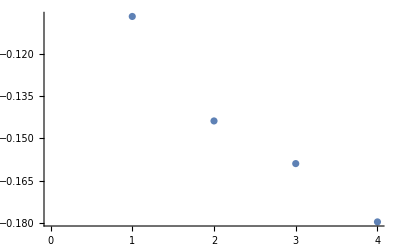

```mathematica
Stat=Nbysum@Table[E^(c*responseGB1[[i]]),{i,seqlistsub}];
r=Table[Abs@Qmat[[i,i]],{i,Length[Qmat]}]//Max
Eig=EigenDecompPart[Stat,MakeDiagonal[Table[2r,Length[seqlist]]]+Qmat,5];//AbsoluteTiming
Eigvecs=Replace[Eig[[4]],MatrixForm[a_,___]:>a];
Eigenvals=Rest[Eig[[1]]]-2r;
ListPlot[Eigenvals ]
```

```mathematica
Eigvecs2=Eigvecs.MakeDiagonal[Prepend[1/(Sqrt[-Eigenvals]),0]];
coordinates=Eigvecs2[[All,2;;3]];
```

```mathematica
seqtips=StringJoin/@(sequences[[seqlistsub]]/.DigitToAARules);
```

```mathematica
colordata=(ColorData["TemperatureMap"][#]&/@Rescale[responseGB1[[seqlistsub]]]);
```

```mathematica
ranges={Floor[Min[#]],Ceiling[Max[#]]}&/@Transpose@coordinates[[All,{1,2}]]
```

{{-7,4},{-1,279}}

```mathematica
coordinates=coordinates[[All,{1,2}]].{{1,0},{0,Abs[Subtract@@ranges[[1]]]/Abs[Subtract@@ranges[[2]]]}};
pr={Floor[Min[#]],Ceiling[Max[#]]}&/@Transpose@coordinates[[All,{1,2}]];
ticks={maketicks@@pr[[1]],maketicks@@pr[[2]]};
padding=1;
```

```mathematica
fig=GraphPlot[Adj[[seqlistsub,seqlistsub]][[sub,sub]],AspectRatio->.0001,
VertexCoordinateRules->coordinates[[sub,{1,2}]].{{1,0},{0,1}},VertexRenderingFunction->Function[{p,l},{colordata[[sub]][[l]],Point[p]}],PlotStyle->{GrayLevel[.8],PointSize->0.01,Thickness->.5 10^-3},Axes->True,AxesStyle->{{Thickness[.001],GrayLevel[0],Arrowheads[.025]},{Thickness[.001],GrayLevel[0],Arrowheads[.025]}},Ticks->{{#,Style[Text[#]],{.01,0}}&/@ticks[[1]],{#,Style[Text[#]],{.01,0}}&/@ticks[[2]]},TicksStyle->Directive[FontSize->12],PlotRange->pr,PlotRangePadding->{0,.1},ImagePadding->padding,ImageSize->{Automatic,400}]
```

```mathematica
figr=Rasterize[fig,RasterSize->500];
```

## TF microarray

## Set parameters

```mathematica
alpha=4;(* alleles per site *)
l=8;(* length of sequence *)
A=Range[0,alpha-1];(*the alphabet in numbers 0-19*)
sequences=Tuples[A,l];(*list of all sequences*)
seq2pos[seq_]:=FromDigits[seq,alpha]+1;
multiplicities=Table[Binomial[l,k](alpha-1)^k,{k,0,l}]; 
nfaces=Binomial[l,2] (Binomial[alpha,2]^2 ) alpha^(l-2);
wt=ConstantArray[0,l];
AA={"A","C","G","T"};
AAtoDigitRules = {"A"->0,"C"->1,"G"->2,"T"->3};
DigitToAARules = {0->"A",1->"C",2->"G",3->"T"};
```

## Functions

### Basic functions

```mathematica
dp[v_]:=v//DeleteDuplicates
uqc[v_]:=v//DeleteDuplicates//Length
lg[v_]:=v//Length
dim[m_]:=m//Dimensions
def[func_]:=func//Definition
```

```mathematica
seq2posAA[seqAA_]:=seq2pos[Characters[seqAA]/.AAtoDigitRules]
```

```mathematica
associate0[list_,obj_]:=Table[list[[i]]->obj,{i,Length[list]}]
```

```mathematica
MakeDiagonal[vect_]:= SparseArray[Table[{i,i}->vect[[i]],{i,Length[vect]}]]
```

```mathematica
Nbysum[y_]:=(1/Total[y])*y
Nbyfirst[y_]:=(1/First@y)*y
```

```mathematica
ginv[x_]:=If[N[x]==0.,0,1/x]
```

```mathematica
r2[x_, y_] := Correlation[x, y]^2;
mse[x_, y_] := Mean[(x - y)^2];
maxorder[list_] := 
  Module[{i}, 
   For[i = 1, list[[i ;;]] != ConstantArray[0, Length[list[[i ;;]]]], 
    i++]; i - 1];

(*From sequence to lexicographical position*)

seq2pos[seq_] := FromDigits[seq, alpha] + 1


(*Map a vector of length m to a vector of length alpha^l. "list" contains the lexicographical positions for all sequences in "data"*)
MapPartialVal[list_,data_,height_]:=Module[{Ab},
Ab=SparseArray[Transpose[{list,Range[1,Length[list]]}]->1,{height,Length[list]}];
Ab.data
]
```

```mathematica
NAremove1[x_]:=Module[{Apos},
Apos=Flatten@Position[(Boole[#!="NaN"]&/@x),1];
x[[Apos]]
]
```

```mathematica
NAremove2[x_,y_]:=Module[{Apos},
Apos=Flatten@Position[(Boole[#!="NaN"]&/@x)*(Boole[#!="NaN"]&/@y),1];
{x[[Apos]],y[[Apos]]}
]
```

### Projection operators

```mathematica
Pby[x_,Pcoeffs_]:=Pcoeffs[[1;;maxorder[Pcoeffs]]].NestList[L.#&,x,maxorder[Pcoeffs]-1];
```

```mathematica
Pkby[x_,k_]:=Module[{Pcoeffs},
Pcoeffs=Inverse[LPs].wkd[[All,k+1]];
Pcoeffs[[1;;maxorder[Pcoeffs]]].NestList[L.#&,x,maxorder[Pcoeffs]-1]];
```

### Regression functions

```mathematica
(*Ridge regression with regularization parameter "λ" and design matrix "design"*)

RidgeRegression[design_, response_, λ_] := Module[{cross},
  cross = Transpose[design].design;
  Do[cross[[i, i]] += λ^2, {i, Length[cross]}];
  LinearSolve[cross,
   Transpose[design].response,
   Method -> {"Krylov", "Method" -> "ConjugateGradient", 
     "Preconditioner" -> "ILU0"}]]

(*Ordinary least square regression*)

OrdinaryRegression[design_, response_] := Module[{cross},
  cross = Transpose[design].design;
  LinearSolve[cross, Transpose[design].response, Method -> "Krylov"]]

(*Build design vector for a sequence using the Taylor encoding*)

s2dTaylor[seq_, order_, wt_] := Module[{seqprime, sub1, sub2, pos},
  seqprime = Mod[seq - wt, alpha];
  sub1 = Subsets[seqprime, {order}];
  sub2 = Table[Join[{i}, sub1[[i]]], {i, Length[sub1]}]; 
  pos = FromDigits[Rest[#] - 1, alpha - 1] + 
      1 + (#[[1]] - 1)*((alpha - 1)^order) & /@ 
    Select[sub2, ! MemberQ[#, 0] &];
  SparseArray[
   Table[pos[[i]] -> 1, {i, 
     Length[pos]}], {Binomial[l, order]*(alpha - 1)^order}]
  ]
(*Build design vector for sequence using the one-hot encoding*)

s2d[seq_, order_] := Module[{sub1, sub2, pos},
  sub1 = Subsets[seq, {order}];
  sub2 = Table[Join[{i}, sub1[[i]]], {i, Length[sub1]}]; 
  pos = FromDigits[Rest[#], alpha] + 
      1 + (#[[1]] - 1)*(alpha^order) & /@ sub2;
  SparseArray[
   Table[pos[[i]] -> 1, {i, 
     Length[pos]}], {Binomial[l, order]*(alpha)^order}]
  ]

designrules[seq_, order_, wt_,j_]:=Module[{seqprime, sub1, sub2, pos},
  seqprime = Mod[seq - wt, alpha];
  sub1 = Subsets[seqprime, {order}];
  sub2 = Table[Join[{i}, sub1[[i]]], {i, Length[sub1]}]; 
  pos = FromDigits[Rest[#] - 1, alpha - 1] + 
      1 + (#[[1]] - 1)*((alpha - 1)^order)+ Total@Table[Binomial[l,k](alpha-1)^(k),{k,0,order-1}]& /@ 
    Select[sub2, ! MemberQ[#, 0] &];
  Table[{j,pos[[i]]} -> 1, {i, 
     Length[pos]}]
  ]
s2dTaylor2[seqs_,order_,wt_]:=Module[{rules},
rules=Flatten[Table[Join[Table[designrules[seqs[[j]],k,wt,j],{k,order}]],{j,Length[seqs]}],2];
SparseArray[rules,{Length[seqs],Total@Table[Binomial[l, k]*(alpha - 1)^k,{k,order}]}]
]

designrulesonehot[seq_, order_,j_]:=Module[{ sub1, sub2, pos},

  sub1 = Subsets[seq, {order}];
  sub2 = Table[Join[{i}, sub1[[i]]], {i, Length[sub1]}]; 
  pos = FromDigits[Rest[#] , alpha ] + 
      1 + (#[[1]]-1 )*((alpha )^order)+ Total@Table[Binomial[l,k](alpha)^(k),{k,0,order-1}]& /@ 
    sub2;
  Table[{j,pos[[i]]} -> 1, {i, 
     Length[pos]}]
  ]

s2donehot[seqs_,order_]:=Module[{rules},rules=Flatten[Table[Join[Table[designrulesonehot[seqs[[j]],k,j],{k,order}]],{j,Length[seqs]}],2];SparseArray[rules,{Length[seqs],Total@Table[Binomial[l, k]*(alpha ^k),{k,order}]}]]
```

### Kernelized regressions

```mathematica
(*Multiplication by the C matrix defined in the main text. For the matrix by vector multiplication C.f, we evaluate it as {0,-alpha/2,1/2}.{f,L.f,L.L.f} using the function NestList. Note that we have omitted the constant 1/s, since it does not affect the solution to the linear equation*)
CIby[x_]:={0,-alpha/2,1/2}.NestList[L.#&,x,2]

(*Similar to C.f, we implement multiplication by a matrix that can be expressed as a polynomial in L using NestList.*)
(*coeffsinLn: vector of coefficients for L^n*)
SprsinLnBy[x_,coeffsinLn_]:=coeffsinLn[[1;;maxorder[coeffsinLn]]].NestList[L.#&,x,maxorder[coeffsinLn]-1]

(*Apply the locally non-epistatic smoother M to a vector*)
Smooth[x_]:=-(1/(Binomial[l,2](alpha-1)^2))CIby[x]+x

(*Calculate the average squared epistasic coefficient for a vector x*)
Cnorm[x_]:=(1/(nfaces))x.CIby[x]

(*Minimum epistasis interpolation solver*)
Cinterp[training_,y_]:=Module[
{Ai,Ab},
Ai=SparseArray[Transpose[{Complement[Range[1,alpha^l],training],Range[1,alpha^l-Length[training]]}]->1,{alpha^l,alpha^l-Length[training]}];
Ab=SparseArray[Transpose[{training,Range[1,Length[training]]}]->1,{alpha^l,Length[training]}];(Ai.LinearSolve[Transpose[Ai].CIby[Ai.#]&,-Transpose[Ai].CIby[Ab.y],Method->{"Krylov",Method->"ConjugateGradient",Tolerance->10^-15}])+Ab.y]

(*Regularized regression with regularization parameter given by "rp". "Ccoeffs" and "Pcoeffs" contain entries for a general cost matrix C (not necessarily the C used in the minimum epistasis interpolation problem) and projection matrix P each of which is represented as the coefficients of a polynomial in L. "Ccoeffs" and "Pcoeffs" for fitting models of different orders are defined below*)
Creg[Ccoeffs_,Pcoeffs_,training_,data_,rp_,var_,startingvector_]:=Module[{Ab,W,Cby,Pby},
W=(1/Length[data]) SparseArray[Table[{training[[i]],training[[i]]}->(1/var[[i]]),{i,Length[training]}],{alpha^l,alpha^l}];
Ab=SparseArray[Transpose[{training,Range[1,Length[training]]}]->1,{alpha^l,Length[training]}];
Cby[x_]:=rp*Ccoeffs[[1;;maxorder[Ccoeffs]]].NestList[L.#&,x,maxorder[Ccoeffs]-1];
Pby[x_]:=Pcoeffs[[1;;maxorder[Pcoeffs]]].NestList[L.#&,x,maxorder[Pcoeffs]-1];
LinearSolve[(Cby[#]+Pby[W.Pby[#]])&,Pby[W.Ab.data],Method->{"Krylov",Method->"ConjugateGradient","StartingVector"->If[Length[startingvector]==0,ConstantArray[0,alpha^l],startingvector]}]
]

(*10-fold crossvalidation using the function Creg*)
3

(*Extract best regularization parameter from the crossvalidation outputs*)
CV[mse_,rps_]:=Module[
{means,ses,min,bestlambda},
means=Mean[mse];
ses=If[Dimensions[mse][[1]]>1,StandardDeviation[mse]/√(Dimensions[mse][[1]]),ConstantArray[0,Dimensions[mse][[2]]]];
min=First[Ordering[means]];
bestlambda=rps[[min ]];
{bestlambda,means,ses}
]
```

3

### Matrix coefficients

```mathematica
(*Krawtchouk polynomial*)
w[k_, d_] := alpha^(-l) ∑_(q=0)^Min[k,d] (-1)^q(alpha-1)^(k-q)Binomial[d,q]Binomial[l-d,k-q]
wkd = Table[w[k,d],{d,0,l},{k,0,l}];
```

```mathematica
(*LPs contains entries of L^n defined at d=0,1,...l. For any matrix whose (i,j)-th entry only depends on d(i,j), we can then solve a linear equation for the coefficients*)
B=SparseArray[{i_,i_}->(alpha-1)*l,{l+1,l+1}]-1*(SparseArray[{i_,j_}/;i==j:>(i-1)*(alpha-2),{l+1,l+1}]+SparseArray[{i_,j_}/;i-j==1:>i-1,{l+1,l+1}]+SparseArray[{i_,j_}/;i-j==-1:>(l-j+2)*(alpha-1),{l+1,l+1}]);
LPs=ArrayReshape[{PadRight[{1},l+1],PadRight[{(alpha-1)*l,-1},l+1],Table[MatrixPower[B,i].PadRight[{(alpha-1)*l,-1},l+1],{i,1,l-1}]},{l+1,l+1}]//Transpose;

(*Entries of the pseudo-inverse of the interpolation matrix C*)
KIentries=Table[ReleaseHold[Hold[∑_(k=2)^length (alpha^(-l)  1/(((a k)^2-a(a k))a^length)∑_(q=0)^Min[k,d] (-1)^q(alpha-1)^(k-q)Binomial[d,q]Binomial[l-d,k-q])]/.{length->l,a->alpha}],{d,0,l}];

(*Entries of the cost matrix for pairwise regression*)
C2entries=Table[ReleaseHold[Hold[∑_(k=2)^2 (alpha^(-l)  ∑_(q=0)^Min[k,d] (-1)^q(alpha-1)^(k-q)Binomial[d,q]Binomial[l-d,k-q])]/.{length->l,a->alpha}],{d,0,l}];

(*Entries of the cost matrix for three-way regression*)
C3entries=Table[ReleaseHold[Hold[∑_(k=2)^3 (alpha^(-l)  ∑_(q=0)^Min[k,d] (-1)^q(alpha-1)^(k-q)Binomial[d,q]Binomial[l-d,k-q])]/.{length->l,a->alpha}],{d,0,l}];
(*Entries of the cost matrix for the Additive model*)
P1entries=Table[ReleaseHold[Hold[∑_(k=0)^1 (alpha^(-l)∑_(q=0)^Min[k,d] (-1)^q(alpha-1)^(k-q)Binomial[d,q]Binomial[l-d,k-q])]/.{length->l,a->alpha}],{d,0,l}];

(*Entries of the cost matrix for the Pairwise model*)
P2entries=Table[ReleaseHold[Hold[∑_(k=0)^2 (alpha^(-l)∑_(q=0)^Min[k,d] (-1)^q(alpha-1)^(k-q)Binomial[d,q]Binomial[l-d,k-q])]/.{length->l,a->alpha}],{d,0,l}];

(*Entries of the cost matrix for the Three-way model*)
P3entries=Table[ReleaseHold[Hold[∑_(k=0)^3 (alpha^(-l)∑_(q=0)^Min[k,d] (-1)^q(alpha-1)^(k-q)Binomial[d,q]Binomial[l-d,k-q])]/.{length->l,a->alpha}],{d,0,l}];
(*Coefficients for the interpolation matrix C in L*)
CIinLn=PadRight[{0,-alpha/2,1/2},l+1];

(*Coefficients for the interpolation kernel matrix K in L*)
KIinLn=Inverse[LPs].KIentries;

(*Coefficients for the cost matrix for the Pairwise model in L*)
C2inLn=Inverse[LPs].C2entries;

(*Coefficients for the cost matrix for the Three-way model in L*)
C3inLn=Inverse[LPs].C3entries;

(*Coefficients for the projection matrix for the Three-way model in L*)
P3inLn=Inverse[LPs].P3entries;

(*Coefficients for the projection matrix for the Pairwise model in L*)
P2inLn=Inverse[LPs].P2entries;

(*Coefficients for the projection matrix for the Additive model in L*)
P1inLn=Inverse[LPs].P1entries;
```

### Build matrices

```mathematica
(*Build graph Laplacian of the sequence space. L is a sparse matrix with sparsity = 1 - ((alpha-1)l+1)/(alpha^l). Therefore we'll use it to facilitate fast solution of most linear equations in this notebook*)
MakeLaplacian[A_,l_]:=SparseArray[
Join[Table[{i,i}->l(A-1),{i,1,A^l}],
Flatten[Table[
{i,FromDigits[ReplacePart[IntegerDigits[i-1,A,l],-k->alt],A]+1}->-1,
{i,1,A^l},{k,1,l},{alt,Complement[Range[0,A-1],{IntegerDigits[i-1,A,l][[-k]]}]}],2]]]
```

```mathematica
AbsoluteTiming[L=MakeLaplacian[alpha,l];]
```

{14.2882,Null}

```mathematica
MakeAdj[A_,l_]:=SparseArray[
Flatten[Table[
{i,FromDigits[ReplacePart[IntegerDigits[i-1,A,l],-k->alt],A]+1}->1,
{i,1,A^l},{k,1,l},{alt,Complement[Range[0,A-1],{IntegerDigits[i-1,A,l][[-k]]}]}],2]]
```

```mathematica
Adj=MakeAdj[alpha,l];//AbsoluteTiming
```

{15.013,Null}

```mathematica
null = Table[
   Join[s2dTaylor[sequences[[i]], 0, wt], 
    s2dTaylor[sequences[[i]], 1, wt]], {i, Length[sequences]}];//AbsoluteTiming
```

{9.76976,Null}

```mathematica
(*null2=SparseArray[Table[Join[s2dTaylor[seq,0,wt],s2dTaylor[seq,1,wt],s2dTaylor[seq,2,wt]],{seq,sequences}]];//AbsoluteTiming*)
```

```mathematica
(*null3=s2dTaylor2[sequences,Range[0,3],wt];//AbsoluteTiming*)
```

#### False discovery rate

```mathematica
fpr[f_,pd_,cutoff_]:=Module[{counts},
counts=Sort@Tally[#>cutoff&/@f[[Flatten@Position[#>cutoff&/@pd,True]]]];
If[Total[counts[[All,2]]]==0,"NaN",counts[[All,2]][[1]]/Total[counts[[All,2]]]//N]
]
```

## Parsing data

```mathematica
SetDirectory[wd];
```

```mathematica
CreateDirectory["TF"];
```

```mathematica
SetDirectory[StringJoin[wd,"/TF"]];
```

To download the data needed for this section
Go to: http://cisbp.ccbr.utoronto.ca/
On the homepage, select “Weirauch, 2014” in the “By Study“ menu
Then Select “version 0.90” in the “Database Build” menu
Click the “GO” button
Click on “Add all TFs to cart”
Click on “View cart” on the menu to the left
Click on “Download TFs in cart”
On the next page, check only the “EScores” box
Click “Download TFs in cart”
Unzip the file, then put in the “wd/TF” folder

```mathematica
EscoreAll=Import["EScore.txt","TSV"];
```

```mathematica
EscoreAll//dim
```

{32897,2221}

```mathematica
seqs=Rest@EscoreAll[[All,1]];
```

```mathematica
seqlist=seq2posAA/@seqs;
```

```mathematica
rc[seq_]:=StringJoin[Reverse[Characters[seq]/.{"A"->"T","T"->"A","C"->"G","G"->"C"}]]
```

```mathematica
rules=Table[{{i,seq2posAA[seqs[[i]]]}->1,{i,seq2posAA[rc[seqs[[i]]]]}->1},{i,Length[seqs]}];
rules=Flatten[rules,1];
AB=SparseArray[rules,{Length[seqs],alpha^l}];
```

```mathematica
TFs=StringSplit[#,":"][[1]]&/@EscoreAll[[1,2;;]]//dp;
```

```mathematica
TFpos=Table[Flatten[Position[StringContainsQ[#,TFs[[i]]]&/@EscoreAll[[1]],True]],{i,Length[TFs]}];
```

```mathematica
numberqcount=Table[Tally[NumberQ/@EscoreAll[[2;;,i]]],{i,2,dim[EscoreAll][[2]]}];
```

```mathematica
metadataEscore={(*seqs*)EscoreAll[[2;;,1]],(*colnames*)EscoreAll[[1,2;;]],TFs,(*number replicates*)Length/@TFpos,(*# of numbers for each column*)numberqcount};
```

```mathematica
TFs=metadataEscore[[3]];
```

```mathematica
TFexcld=StringSplit[#,":"][[1]]&/@metadataEscore[[2]][[Flatten@Position[lg/@metadataEscore[[5]],2]]]
```

```mathematica
EscoreTFlist=Complement[Range[lg@TFs],Flatten@(Position[TFs,#]&/@dp[TFexcld])];
```

#### Export individual datasets & metadata

```mathematica
Export["metadataEscore.m",metadataEscore];
```

```mathematica
Do[Export[StringJoin["Es_",ToString[i],".tsv"],EscoreAll[[All,TFpos[[i]]]]],{i,Length@TFpos}];
```

#### Export data to R

```mathematica
rules=Flatten[Table[Join[Table[designrulesonehot[sequences[[j]],k,j],{k,3}]],{j,Length[sequences]}],2];
null3=SparseArray[rules,{Length[sequences],Total@Table[Binomial[l, k]*alpha^k,{k,0,3}]}];
Export["designrules.tsv",Transpose@{Most[ArrayRules[null3]][[All,1]][[All,1]],Most[ArrayRules[null3]][[All,1]][[All,2]]},"TSV"];
Export["ABrules.tsv",Transpose@{Most[ArrayRules[AB]][[All,1]][[All,1]],Most[ArrayRules[AB]][[All,1]][[All,2]]},"TSV"];
```

## Inference

### Interpolation, additive, pairwise L2, three-way L2

```mathematica
metadataEscore=Import["metadataEscore.m"];
```

```mathematica
TFs=metadataEscore[[3]];
```

```mathematica
(*Exclude experiments with NaN*)
TFexcld=StringSplit[#,":"][[1]]&/@metadataEscore[[2]][[Flatten@Position[lg/@metadataEscore[[5]],2]]]
```

{M02633_2.00,M02633_2.00,M02633_2.00,M02635_2.00,M02635_2.00,M02635_2.00,M02635_2.00,M02635_2.00}

```mathematica
EscoreTFlist=Complement[Range[lg@TFs],Flatten@(Position[TFs,#]&/@dp[TFexcld])];
```

Inferences are done in batches of 50 experiments

```mathematica
subsets=Partition[EscoreTFlist,50];
subsets=Join[subsets,{Complement[EscoreTFlist,Flatten[subsets]]}];
```

```mathematica
CreateDirectory["results"];
CreateDirectory["pds"];
```

```mathematica
Do[
{
pds=Table[{},lg@subsets[[k]]];
results=Table[{},lg@subsets[[k]]];
Do[
{dat=Rest@Import[StringJoin["Es_",ToString[subsets[[k]][[i]]],".tsv"],"TSV"];
f=Transpose[AB].Mean[Transpose@dat];

cutoff=Quantile[f,.95];

training=RandomSample[Range[alpha^l],Round[.9 alpha^l]];test=Complement[Range[alpha^l],training];

pd1=null.OrdinaryRegression[null[[training]],f[[training]]];

pdME=Cinterp[training,f[[training]]];

crossval2=CrossvalidationC[C2inLn,P2inLn,training,f[[training]],rps2,ConstantArray[1,Length[training]],10,10];
bestlambda2=N@CV[crossval2,rps2][[1]];
pd2=Creg[C2inLn,P2inLn,training,f[[training]],bestlambda2,ConstantArray[1,Length[training]],{}];

crossval3=CrossvalidationC[C3inLn,P3inLn,training,f[[training]],rps3,ConstantArray[1,Length[training]],10,10];
bestlambda3=N@CV[crossval3,rps3][[1]];
pd3=Creg[C3inLn,P3inLn,training,f[[training]],bestlambda3,ConstantArray[1,Length[training]],{}];

pds[[i]]=
{{training},{pdME, pd1, pd2, pd3}};

results[[i]]=
{{r2[pdME[[test]],f[[test]]],r2[pd1[[test]],f[[test]]],r2[pd2[[test]],f[[test]]],r2[pd3[[test]],f[[test]]]},{fpr[f[[test]],pdME[[test]],cutoff],fpr[f[[test]],pd1[[test]],cutoff],fpr[f[[test]],pd2[[test]],cutoff],fpr[f[[test]],pd3[[test]],cutoff]}};

Print[StringJoin[ToString[i]," Done"]]
},{i,lg@subsets[[k]]}
];
Export[StringJoin["pds/pds_",ToString[k],".m"],pds];
Export[StringJoin["tr_",ToString[subsets[[k]][[i]]],".tsv"],tr];
Export[StringJoin["results//results_",ToString[k],".m"],results];
Print["Batch "<>ToString[k]<> " is done"]
},{k,Length[subsets]}
]
```

```mathematica
resultsEscore=Flatten[Join[Table[Import[StringJoin["results/results_",ToString[i],".m"]],{i,23}]],1];
```

```mathematica
resultsEscore//dim
```

{1121,2,4}

### three-way L1

First execute R file “TF.R” 
then import results with the following code:

```mathematica
resultsL1=Table[Module[{f,pd,tr,ts},
f=Transpose[AB].Mean[Transpose@Rest@Import[StringJoin["Es_",ToString[i],".tsv"]]];
pd=Import[StringJoin["pd3L1_",ToString[i],".tsv"]][[2;;,2]];
tr=Flatten@Import[StringJoin["tr_",ToString[i],".tsv"]];
ts=Complement[Range[alpha^l],tr];
{r2[f[[ts]],pd[[ts]]],fpr[f[[ts]],pd[[ts]],Quantile[f,.95]]}],{i,EscoreTFlist}];
```

```mathematica
resultsEscore[[All,1]]=Transpose[Join[Transpose@resultsEscore[[All,1]],{resultsL1[[All,1]]}]];
resultsEscore[[All,2]]=Transpose[Join[Transpose@resultsEscore[[All,2]],{resultsL1[[All,2]]}]];
```

### Result summary

```mathematica
labs={Style[" Interpolation",FontFamily->"Helvetica"],Style["Additive",FontFamily->"Helvetica"],Row[{Subscript[Style["L",FontFamily->"Helvetica",Italic],2],Style[" Pairwise",FontFamily->"Helvetica"]}],Row[{Subscript[Style["L",FontFamily->"Helvetica",Italic],2],Style[" Three-way",FontFamily->"Helvetica"]}],Row[{Subscript[Style["L",FontFamily->"Helvetica",Italic],1],Style[" Three-way",FontFamily->"Helvetica"]}]};
```

```mathematica
Labeled[TableForm[Table[{Mean@Select[resultsEscore[[All,1,i]],NumberQ],StandardDeviation@Select[resultsEscore[[All,1,i]],NumberQ]},{i,5}],TableHeadings->{labs,{"\nMean","\nStd"}}],Style[Superscript["R",2],20],Top]
```

| 
Mean | 
Std
 Interpolation | 0.710061 | 0.113336
Additive | 0.315559 | 0.215672
L_2 Pairwise | 0.585453 | 0.142144
L_2 Three-way | 0.679677 | 0.113485
L_1 Three-way | 0.677639 | 0.113876R^2

```mathematica
Labeled[TableForm[Table[{Mean@Select[resultsEscore[[All,2,i]],NumberQ],StandardDeviation@Select[resultsEscore[[All,2,i]],NumberQ]},{i,5}],TableHeadings->{labs,{"\nMean","\nStd"}}],Style["FDR",20],Top]
```

| 
Mean | 
Std
 Interpolation | 0.15417 | 0.117994
Additive | 0.568687 | 0.25939
L_2 Pairwise | 0.337773 | 0.200039
L_2 Three-way | 0.23088 | 0.110541
L_1 Three-way | 0.215634 | 0.111328FDR

```mathematica
Labeled[TableForm[Table[N[Total[#]/Length[#] &@Boole[#>1&/@Select[(resultsEscore[[All,k,i]]/resultsEscore[[All,k,1]]),NumberQ]]],{i,2,5},{k,2}],TableHeadings->{labs[[2;;]],{Style[Superscript["R",2],14],"FDR"}}],Style["Frequncy interpolation has lower value",FontFamily->"Helvetica",20],Top]
```

| R^2 | FDR
Additive | 0. | 0.941284
L_2 Pairwise | 0.00981267 | 0.944545
L_2 Three-way | 0.0651204 | 0.940232
L_1 Three-way | 0.0499554 | 0.877569Frequncy interpolation has lower value

```mathematica
k=1;
```

Percentage of TFs where the interpolation method has higher R2

```mathematica
Total[Table[Product[Boole[resultsEscore[[j,k,1]]>resultsEscore[[j,k,i]]],{i,2,5}],{j,Length@resultsEscore}]]/Length@resultsEscore //N
```

0.933988

Fold reduction in FDR compared with L2 threeway

```mathematica
resultsEscore[[All,2,4]]/resultsEscore[[All,2,1]]//Median
```

1.60611

Fold reduction in FDR compared with L1 threeway

```mathematica
Median[Select[resultsEscore[[All,2,5]]/resultsEscore[[All,2,1]],NumberQ]]
```

1.48693

Fold reduction in FDR compared with L2 pairwise

```mathematica
Median[Select[resultsEscore[[All,2,3]]/resultsEscore[[All,2,1]],NumberQ]]
```

2.17303

### Plotting

```mathematica
padding={{80,10},{60,0}};
```

```mathematica
plotdat1=Table[resultsEscore[[All,1,i]]/resultsEscore[[All,1,1]],{i,3,5}];
```

```mathematica
labsize=20;
ticklabsize=16;
fontsize=16;
```

```mathematica
ticklength=.01;
tickfunc[t_]:={t/.Table[N[i]->i,{i,100}],Text[t/.Table[N[i]->i,{i,-100,100}]],{ticklength,0}}
```

```mathematica
slash=ToString[Style[" / ","Title",GrayLevel[.3],labsize],TraditionalForm];
```

```mathematica
fstyle=Table[{GrayLevel[.3],Thickness[.004]},4];
```

```mathematica
plot1=Table[Labeled[Histogram[plotdat1[[i]],{.015},"Probability",BaseStyle->{FontSize->fontsize},ChartStyle->{GrayLevel[.5]},PlotRange->{{0.4,1.27},{0,0.25}},Frame->{{True,False},{True,False}},FrameTicks->{tickfunc/@Range[0,1.5,.1],tickfunc/@Range[0,1,.05]},FrameLabel->{ToString[Style[Subscript[Superscript[Style["R",Italic],2],labs[[i+2]]],"Title",GrayLevel[.3],labsize],TraditionalForm]<>slash<>ToString[Style[Subscript[Superscript[Style["R",Italic],2],labs[[1]]],"Title",GrayLevel[.3],labsize],TraditionalForm],ToString[Style["Frequency","Title",GrayLevel[.3],labsize],TraditionalForm]},FrameStyle->fstyle,ImagePadding->padding,ImageSize->{400,Automatic}],Style[StringJoin["\n ",ToString[FromLetterNumber[i]]],Bold,FontFamily->"Helvetica",FontSize->18],{{Top,Left}}],{i,3}];
```

```mathematica
plotdat2=Table[resultsEscore[[All,2,i]]/resultsEscore[[All,2,1]],{i,3,5}];
```

```mathematica
plot2=Table[Labeled[Histogram[plotdat2[[i]],{.2},"Probability",PlotRange->{{0,10.5},{0,0.15}},BaseStyle->{FontSize->fontsize},ChartStyle->{GrayLevel[.5]},Frame->{{True,False},{True,False}},FrameTicks->{tickfunc/@Range[0,10,1],tickfunc/@Range[0,1,.04]},FrameLabel->{ToString[Style[Subscript["FDR ",labs[[i+2]]],"Title",GrayLevel[.3],labsize],TraditionalForm]<>slash <>ToString[Style[Subscript["FDR",labs[[1]]],"Title",GrayLevel[.3],labsize],TraditionalForm],ToString[Style["Frequency","Title",GrayLevel[.3],labsize],TraditionalForm]},FrameStyle->fstyle,ImagePadding->padding,ImageSize->{400,Automatic},PlotRangeClipping->True],Style[StringJoin["\n ",ToString[FromLetterNumber[i+3]]],Bold,FontFamily->"Helvetica",FontSize->18],{{Top,Left}}],{i,3}];
```

```mathematica
Figure6=Grid[{plot1,plot2},Spacings->{0,0}];
Export["Figure6.pdf",Figure6];
```

## Hamming class landscapes

## Set parameters

```mathematica
alpha=2;(* alleles per site *)
l=16;(* length of sequence *)
A=Range[0,alpha-1] (*the alphabet*);
sequences=Tuples[A,l](*set of all sequences*);
nfaces=Binomial[l,2] (Binomial[alpha,2]^2 ) alpha^(l-2) (*Number of faces of the sequence space*)
wt=ConstantArray[0,l];
mks=Table[Binomial[l,k](alpha-1)^k,{k,0,l}];
```

1966080

## Functions

```mathematica
(*Krawtchouk polynomial*)
w[k_,d_]:=alpha^(-l)∑_(q=0)^Min[k,d] (-1)^q(alpha-1)^(k-q)Binomial[d,q]Binomial[l-d,k-q]
wkd = Table[w[k,d],{d,0,l},{k,0,l}];

(*Build graph Laplacian of the sequence space. L is a sparse matrix with sparsity = 1 - ((alpha-1)l+1)/(alpha^l). Therefore we'll use it to facilitate fast solution of most linear equations in this notebook*)
MakeLaplacian[A_,l_]:=SparseArray[
Join[Table[{i,i}->l(A-1),{i,1,A^l}],
Flatten[Table[
{i,FromDigits[ReplacePart[IntegerDigits[i-1,A,l],-k->alt],A]+1}->-1,
{i,1,A^l},{k,1,l},{alt,Complement[Range[0,A-1],{IntegerDigits[i-1,A,l][[-k]]}]}],2]]]
L=MakeLaplacian[alpha,l];

(*Multiplication by the C matrix defined in the main text. For the matrix by vector multiplication C.f, we evaluate it as {0,-alpha/2,1/2}.{f,L.f,L.L.f} using the function NestList. Note that we have omitted the constant 1/s, since it does not affect the solution to the linear equation*)
CIby[x_]:={0,-alpha/2,1/2}.NestList[L.#&,x,2]

(*Minimum epistasis interpolation solver*)
Cinterp[training_,y_]:=Module[
{Ai,Ab},
Ai=SparseArray[Transpose[{Complement[Range[1,alpha^l],training],Range[1,alpha^l-Length[training]]}]->1,{alpha^l,alpha^l-Length[training]}];
Ab=SparseArray[Transpose[{training,Range[1,Length[training]]}]->1,{alpha^l,Length[training]}];(Ai.LinearSolve[Transpose[Ai].CIby[Ai.#]&,-Transpose[Ai].CIby[Ab.y],Method->{"Krylov",Method->"ConjugateGradient"}])]

maxorder[list_]:=Module[{i},For[i=1,list[[i;;]]!=ConstantArray[0,Length[list[[i;;]]]],i++];i-1];

(*Similar to C.f, we implement multiplication by a matrix that can be express as a polynomial in L using NestList.*)
(*coeffsinLn: vector of coefficients for L^n*)
SprsinLnBy[x_,coeffsinLn_]:=coeffsinLn[[1;;maxorder[coeffsinLn]]].NestList[L.#&,x,maxorder[coeffsinLn]-1]

(*LPs contains entries of L^n defined at d=0,1,...l. For any matrix whose (i,j)-th entry only depends on d(i,j), we can then solve a linear equation for the coefficients*)
B=SparseArray[{i_,i_}->(alpha-1)*l,{l+1,l+1}]-1*(SparseArray[{i_,j_}/;i==j:>(i-1)*(alpha-2),{l+1,l+1}]+SparseArray[{i_,j_}/;i-j==1:>i-1,{l+1,l+1}]+SparseArray[{i_,j_}/;i-j==-1:>(l-j+2)*(alpha-1),{l+1,l+1}]);
LPs=ArrayReshape[{PadRight[{1},l+1],PadRight[{(alpha-1)*l,-1},l+1],Table[MatrixPower[B,i].PadRight[{(alpha-1)*l,-1},l+1],{i,1,l-1}]},{l+1,l+1}]//Transpose;

(*Apply the locally non-epistatic smoother M to a vector*)
Smooth[x_]:=-(1/(Binomial[l,2](alpha-1)^2))CIby[x]+x;
```

```mathematica
abt:=AbsoluteTiming
```

```mathematica
associate[list1_,list2_]:=Table[list1[[i]]->list2[[i]],{i,Length[list1]}]
```

```mathematica
dp[v_]:=v//DeleteDuplicates
uqc[v_]:=v//DeleteDuplicates//Length
lg[v_]:=v//Length
dim[m_]:=m//Dimensions
```

```mathematica
seq2posAA[seqAA_]:=seq2pos[Characters[seqAA]/.AAtoDigitRules]
```

```mathematica
associate0[list_,obj_]:=Table[list[[i]]->obj,{i,Length[list]}]
```

```mathematica
MakeDiagonal[vect_]:= SparseArray[Table[{i,i}->vect[[i]],{i,Length[vect]}]]
```

```mathematica
Nbysum[y_]:=(1/Total[y])*y
Nbyfirst[y_]:=(1/First@y)*y
```

```mathematica
ginv[x_]:=If[N[x]==0.,0,1/x]
```

```mathematica
r2[x_, y_] := Correlation[x, y]^2;
mse[x_, y_] := Mean[(x - y)^2];
maxorder[list_] := 
  Module[{i}, 
   For[i = 1, list[[i ;;]] != ConstantArray[0, Length[list[[i ;;]]]], 
    i++]; i - 1];

(*From sequence to lexicographical position*)
seq2pos[seq_] := FromDigits[seq, alpha] + 1

(*Map a vector of length m to a vector of length alpha^l. "list" contains the lexicographical positions for all sequences in "data"*)
MapPartialVal[list_,data_,height_]:=Module[{Ab},
Ab=SparseArray[Transpose[{list,Range[1,Length[list]]}]->1,{height,Length[list]}];
Ab.data
]
```

### Define crater landscape

```mathematica
(*Define the crater landscape*)
hc[d_]:=1/(1+N[Exp[1(d-6)]])-1/(1+N[Exp[1(d-1)]]);
Plot[hc[x],{x,0,l}]
response=hc[Total[#]]&/@ sequences;
```

-Graphics-

## Sampling

```mathematica
hd=HammingDistance[ConstantArray[0,l],#]&/@sequences;
seqbyhd=Table[Flatten[Position[hd,d]],{d,0,l}];
seqsbyD=GatherBy[Transpose@{HammingDistance[#,ConstantArray[0,l]]&/@sequences,sequences},First][[All,All,2]];
hdsub=Flatten@Table[RandomSample[seq2pos/@seqsbyD[[i]],1],{i,lg@seqsbyD}];
```

```mathematica
(*We give minimum epistasis interpolation 1%, 10%, 50% and 90% of all data as training and use the rest of the data as test*)
training=Table[RandomSample[Range[alpha^l],Ceiling[i alpha^l]],{i,{.01,.1,.5,.9}}];
test=Table[Complement[Range[alpha^l],training[[i]]]//Flatten,{i,4}];
Do[If[Intersection[test[[i]],seqbyhd[[j]]]=={},test[[i]] = Union[test[[i]],{hdsub[[j]]}]],{j,lg@hdsub},{i,lg@test}]
training=Table[Complement[Range[alpha^l],test[[i]]]//Flatten,{i,Length[test]}];
```

```mathematica
axstyle1=Join[{{Transparent,Automatic}},ConstantArray[{Transparent,Transparent},3]];
tkstyle1=Join[{{Transparent,Automatic}},ConstantArray[{Transparent,Transparent},3]];
```

```mathematica
axstyle2=Join[{{Automatic,Automatic}},ConstantArray[{Automatic,Transparent},3]];
tkstyle2=Join[{{Automatic,Automatic}},ConstantArray[{Automatic,Transparent},3]];
```

```mathematica
labsize=14;
ticklabsize=14;
```

## Hamming Ball

### Define landscape

```mathematica
r=8+.5;
```

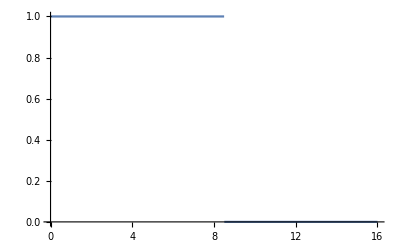

```mathematica
(*Define the crater landscape*)
hc[d_]:=N@If[d<=r,1,0];
Plot[hc[x],{x,0,l}]
response=hc[Total[#]]&/@ sequences;
```

### Out-of-sample predictions by the minimum epistasis interpolation

```mathematica
pdMEI=Table[Cinterp[training[[i]],response[[training[[i]]]]],{i,4}];
```

### 100% data regressions vs interpolation

```mathematica
(*We fit the three regression models to all the data using ordinary least squares. We implement it by projecting the response vector into the eigenspaces up to the 1st,2nd,or 3rd order using the projection matrix W_0 + ... W_k, for k=1,2,3*)
pd1Way100percent=SprsinLnBy[response,Inverse[LPs].(wkd[[All,;;2]].ConstantArray[1,2])];
pd2Way100percent=SprsinLnBy[response,Inverse[LPs].(wkd[[All,;;3]].ConstantArray[1,3])];
pd3Way100percent=SprsinLnBy[response,Inverse[LPs].(wkd[[All,;;4]].ConstantArray[1,4])];

(*Analytical formula for leave-one-out prediction by Minimum Epistasis Interpolation for a sequence at distance d to WT based on function f*)
loohc[d_,f_]:=2*1/(l(alpha-1))(d f[Abs[d-1]]+d(alpha-2)f[d]+(l-d)(alpha-1)f[d+1])-(Binomial[d,2]f[Abs[d-2]]+(d(l-d)(alpha-1)+Binomial[d,2](alpha-2)^2)f[d]+Binomial[l-d,2](alpha-1)^2 f[d+2])/(Binomial[l,2])

(*Leave-one-out prediction using Minimum epistasis interpolation*)
pdMELOO=Smooth[response];
```

```mathematica
pr={{0,l+1},{-2.5,2.5}};
```

```mathematica
plotdats1=Table[dp@Transpose[{Total[#]&/@sequences[[test[[i]]]],pdMEI[[i]][[test[[i]]]]}],{i,lg@test}];
plotdats2={dp@Transpose[{Total[#]&/@sequences,pd1Way100percent}],dp@Transpose[{Total[#]&/@sequences,pd2Way100percent}],dp@Transpose[{Total[#]&/@sequences,pd3Way100percent}],dp@Transpose[{Total[#]&/@sequences,pdMELOO}]};
```

```mathematica
labs1=Table[Style["Interpolation "<>ToString[IntegerPart[100 {.01,.1,.5,.9}[[i]]]]<> "%",FontSize->14],{i,4}];
labs2={"Additive 100%","Pairwise 100%","Three-way 100%","Interpolation\n leave-one-out"};
labs2=Table[Style[labs2[[i]],FontSize->labsize],{i,4}];
```

```mathematica
xticks=Range[0,l+1,4];
yticks=Range[-6,6,1];
tk={{#,Style[Text[#]],{.02,0}}&/@xticks,{#,Style[Text[#]],{.02,0}}&/@yticks};
ticks=ConstantArray[tk,4];
```

```mathematica
axstyle=Join[{{Automatic,Automatic}},ConstantArray[{Automatic,Automatic},3]];
tkstyle=Join[{{Automatic,Automatic}},ConstantArray[{Automatic,Transparent},3]];
```

```mathematica
fig=Grid[{Table[Show[ListPlot[plotdats1[[i]],PlotRange->pr,BaseStyle->{FontSize-> ticklabsize},PlotStyle->{PointSize[.02],Black},AspectRatio->1,PlotRangeClipping->False,Ticks->ticks[[i]],AxesStyle->axstyle1[[i]],TicksStyle->tkstyle1[[i]],Epilog->Inset[labs1[[i]],{8,2}],ImageSize->{200,Automatic}],
Plot[hc[x],{x,0,l},PlotStyle->Gray,PlotRange->All,Exclusions->None]],{i,4}],Table[Show[ListPlot[plotdats2[[i]],PlotRange->pr,BaseStyle->{FontSize-> ticklabsize},PlotStyle->{PointSize[.02],Black},AspectRatio->1,PlotRangeClipping->False,Ticks->ticks[[i]],AxesStyle->axstyle2[[i]],TicksStyle->tkstyle2[[i]],Epilog->Inset[labs2[[i]],{8,2}],ImageSize->{200,Automatic},AxesOrigin->{0,-2.3}],
Plot[hc[x],{x,0,l},PlotStyle->Gray,PlotRange->All,Exclusions->None]],{i,4}]}];
```

```mathematica
figball=Labeled[Labeled[fig,{"Phenotype"},{Left},LabelStyle->Directive[FontFamily->"Helvetica",FontSize->labsize+1],RotateLabel->True],"A",{{Left,Top}},LabelStyle->Directive[FontFamily->"Helvetica",FontSize->labsize+4],RotateLabel->False];
```

## Quadratic

### Define landscape

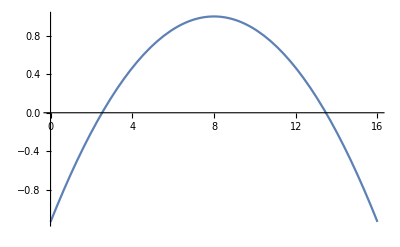

```mathematica
(*Define the crater landscape*)
hc[d_]:=-(2/60)N@(d-8)^2+1;
Plot[hc[x],{x,0,l}]
response=hc[Total[#]]&/@ sequences;
```

### Out-of-sample predictions by the minimum epistasis interpolation

```mathematica
(*We give minimum epistasis interpolation 1%, 10%, 50% and 90% of all data as training and use the rest of the data as test*)
pdMEI=Table[Cinterp[training[[i]],response[[training[[i]]]]],{i,4}];
```

### 100% data regressions vs interpolation

```mathematica
(*We fit the three regression models to all the data using ordinary least squares. We implement it by projecting the response vector into the eigenspaces up to the 1st,2nd,or 3rd order using the projection matrix W_0 + ... W_k, for k=1,2,3*)
pd1Way100percent=SprsinLnBy[response,Inverse[LPs].(wkd[[All,;;2]].ConstantArray[1,2])];
pd2Way100percent=SprsinLnBy[response,Inverse[LPs].(wkd[[All,;;3]].ConstantArray[1,3])];
pd3Way100percent=SprsinLnBy[response,Inverse[LPs].(wkd[[All,;;4]].ConstantArray[1,4])];
pdMELOO=Smooth[response];
```

```mathematica
pr={{0,l+1},{-1.5,1.7}};
```

```mathematica
plotdats1=Table[dp@Transpose[{Total[#]&/@sequences[[test[[i]]]],pdMEI[[i]][[test[[i]]]]}],{i,lg@test}];
```

```mathematica
labs1=Table[Style["Interpolation "<>ToString[IntegerPart[100 {.01,.1,.5,.9}[[i]]]]<> "%",FontSize->labsize],{i,4}];
```

```mathematica
plotdats2={dp@Transpose[{Total[#]&/@sequences,pd1Way100percent}],dp@Transpose[{Total[#]&/@sequences,pd2Way100percent}],dp@Transpose[{Total[#]&/@sequences,pd3Way100percent}],dp@Transpose[{Total[#]&/@sequences,pdMELOO}]};
```

```mathematica
labs2={"Additive 100%","Pairwise 100%","Three-way 100%","Interpolation\n leave-one-out"};
labs2=Table[Style[labs2[[i]],FontSize->labsize],{i,4}];
```

```mathematica
ticks=Table[{Range[0,l+1,4],Range[-3,3,1]},4];
xticks=Range[0,l+1,4];
yticks=Range[-6,6,1];
tk={{#,Style[Text[#]],{.02,0}}&/@xticks,{#,Style[Text[#]],{.02,0}}&/@yticks};
ticks=ConstantArray[tk,4];
```

```mathematica
axstyle=Join[{{Automatic,Automatic}},ConstantArray[{Automatic,Automatic},3]];
tkstyle=Join[{{Automatic,Automatic}},ConstantArray[{Automatic,Transparent},3]];
```

```mathematica
fig=Grid[{Table[Show[ListPlot[plotdats1[[i]],PlotRange->pr,BaseStyle->{FontSize-> ticklabsize},PlotStyle->{PointSize[.02],Black},AspectRatio->1,PlotRangeClipping->False,Ticks->ticks[[i]],AxesStyle->axstyle1[[i]],TicksStyle->tkstyle1[[i]],Epilog->Inset[labs1[[i]],{8,1.4}],ImageSize->{200,Automatic}],
Plot[hc[x],{x,0,l},PlotStyle->Gray,PlotRange->All,Exclusions->None]],{i,4}],Table[Show[ListPlot[plotdats2[[i]],PlotRange->pr,BaseStyle->{FontSize-> ticklabsize},PlotStyle->{PointSize[.02],Black},AspectRatio->1,PlotRangeClipping->False,Ticks->ticks[[i]],AxesStyle->axstyle2[[i]],TicksStyle->tkstyle2[[i]],Epilog->Inset[labs2[[i]],{8,1.4}],ImageSize->{200,Automatic},AxesOrigin->{0,-1.3}],
Plot[hc[x],{x,0,l},PlotStyle->Gray,PlotRange->All,Exclusions->None]],{i,4}]}];
```

```mathematica
figq=Labeled[Labeled[fig,{"Phenotype"},{Left},LabelStyle->Directive[FontFamily->"Helvetica",FontSize->labsize+1],RotateLabel->True],"B",{{Left,Top}},LabelStyle->Directive[FontFamily->"Helvetica",FontSize->labsize+4],RotateLabel->False];
```

## Sinusoidal

### Define landscape

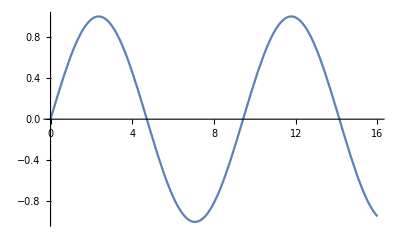

```mathematica
(*Define the crater landscape*)
hc[d_]:=N@Sin[d/1.5];
Plot[hc[x],{x,0,l}]
response=hc[Total[#]]&/@ sequences;
```

### Out-of-sample predictions by the minimum epistasis interpolation

```mathematica
(*We give minimum epistasis interpolation 1%, 10%, 50% and 90% of all data as training and use the rest of the data as test*)
pdMEI=Table[Cinterp[training[[i]],response[[training[[i]]]]],{i,4}];
```

### 100% data regressions vs interpolation

```mathematica
(*We fit the three regression models to all the data using ordinary least squares. We implement it by projecting the response vector into the eigenspaces up to the 1st,2nd,or 3rd order using the projection matrix W_0 + ... W_k, for k=1,2,3*)
pd1Way100percent=SprsinLnBy[response,Inverse[LPs].(wkd[[All,;;2]].ConstantArray[1,2])];
pd2Way100percent=SprsinLnBy[response,Inverse[LPs].(wkd[[All,;;3]].ConstantArray[1,3])];
pd3Way100percent=SprsinLnBy[response,Inverse[LPs].(wkd[[All,;;4]].ConstantArray[1,4])];

(*Analytical formula for leave-one-out prediction by Minimum Epistasis Interpolation for a sequence at distance d to WT based on function f*)
loohc[d_,f_]:=2*1/(l(alpha-1))(d f[Abs[d-1]]+d(alpha-2)f[d]+(l-d)(alpha-1)f[d+1])-(Binomial[d,2]f[Abs[d-2]]+(d(l-d)(alpha-1)+Binomial[d,2](alpha-2)^2)f[d]+Binomial[l-d,2](alpha-1)^2 f[d+2])/(Binomial[l,2])
(*Leave-one-out prediction using Minimum epistasis interpolation*)
pdMELOO=Smooth[response];
```

```mathematica
plotdats1=Table[dp@Transpose[{Total[#]&/@sequences[[test[[i]]]],pdMEI[[i]][[test[[i]]]]}],{i,lg@test}];
```

```mathematica
labs1=Table[Style["Interpolation "<>ToString[IntegerPart[100 {.01,.1,.5,.9}[[i]]]]<> "%",FontSize->14],{i,4}];
```

```mathematica
plotdats2={dp@Transpose[{Total[#]&/@sequences,pd1Way100percent}],dp@Transpose[{Total[#]&/@sequences,pd2Way100percent}],dp@Transpose[{Total[#]&/@sequences,pd3Way100percent}],dp@Transpose[{Total[#]&/@sequences,pdMELOO}]};
```

```mathematica
labs2={"Additive 100%","Pairwise 100%","Three-way 100%","Interpolation\n leave-one-out"};
```

```mathematica
labs2=Table[Style[labs2[[i]],FontSize->14],{i,4}]
```

{Additive 100%,Pairwise 100%,Three-way 100%,Interpolation
 leave-one-out}

```mathematica
pr1={{0,l+1},{-2.5,2.5}};
pr2={{0,l+1},{-2.5,9.5}};
```

```mathematica
as1=2Subtract@@pr1[[2]]/Subtract@@pr1[[1]];
as2=2Subtract@@pr2[[2]]/Subtract@@pr2[[1]];
```

```mathematica
xticks=Range[0,l+1,4];
yticks=Range[-10,10,2];
tk={{#,Style[Text[#]],{.02,0}}&/@xticks,{#,Style[Text[#]],{.02,0}}&/@yticks};
ticks=ConstantArray[tk,4];
```

```mathematica
axstyle=Join[{{Automatic,Automatic}},ConstantArray[{Automatic,Automatic},3]];
tkstyle=Join[{{Automatic,Automatic}},ConstantArray[{Automatic,Transparent},3]];
```

```mathematica
fig=Grid[{Table[Show[ListPlot[plotdats1[[i]],PlotRange->pr1,BaseStyle->{FontSize-> ticklabsize},PlotStyle->{PointSize[.02],Black},AspectRatio->as1,PlotRangeClipping->False,Ticks->ticks[[i]],AxesStyle->axstyle1[[i]],TicksStyle->tkstyle1[[i]],Epilog->Inset[labs1[[i]],{8,2}],ImageSize->{200,Automatic}],
Plot[hc[x],{x,0,l},PlotStyle->Gray,PlotRange->All,Exclusions->None]],{i,4}],Table[Show[ListPlot[plotdats2[[i]],PlotRange->pr2,BaseStyle->{FontSize-> ticklabsize},PlotStyle->{PointSize[.02],Black},AspectRatio->as2,PlotRangeClipping->False,Ticks->ticks[[i]],AxesStyle->axstyle2[[i]],TicksStyle->tkstyle2[[i]],Epilog->Inset[labs2[[i]],{8,8.3}],ImageSize->{200,Automatic},AxesOrigin->{0,-2}],
Plot[hc[x],{x,0,l},PlotStyle->Gray,PlotRange->All,Exclusions->None]],{i,4}]}];
```

```mathematica
figsin=Labeled[Labeled[fig,{"Phenotype"},{Left},LabelStyle->Directive[FontFamily->"Helvetica",FontSize->labsize+1],RotateLabel->True],"C",{{Left,Top}},LabelStyle->Directive[FontFamily->"Helvetica",FontSize->labsize+4],RotateLabel->False];
```

## Plotting

```mathematica
FigureS1=Rasterize[Labeled[Grid[{{figball},{figq},{figsin}},Spacings->{3, 3}],{"Hamming Distance to WT"},{Bottom},LabelStyle->Directive[FontSize->labsize+1,FontFamily->"Helvetica"],RotateLabel->True],RasterSize->2000];
```

```mathematica
Export["FigureS1.pdf",FigureS1];
```

## Quadratic landscape

### Set parameters

```mathematica
alpha=2;(* alleles per site *)
l=20;(* length of sequence *)
A=Range[0,alpha-1] (*the alphabet*);
sequences=Tuples[A,l](*set of all sequences*);
nfaces=Binomial[l,2] (Binomial[alpha,2]^2 ) alpha^(l-2) (*Number of faces of the sequence space*)
```

49807360

### Functions

```mathematica
(*Krawtchouk polynomial*)
w[k_,d_]:=alpha^(-l)∑_(q=0)^Min[k,d] (-1)^q(alpha-1)^(k-q)Binomial[d,q]Binomial[l-d,k-q]
wkd = Table[w[k,d],{d,0,l},{k,0,l}];

(*Build graph Laplacian of the sequence space. L is a sparse matrix with sparsity = 1 - ((alpha-1)l+1)/(alpha^l). Therefore we'll use it to facilitate fast solution of most linear equations in this notebook*)
MakeLaplacian[A_,l_]:=SparseArray[
Join[Table[{i,i}->l(A-1),{i,1,A^l}],
Flatten[Table[
{i,FromDigits[ReplacePart[IntegerDigits[i-1,A,l],-k->alt],A]+1}->-1,
{i,1,A^l},{k,1,l},{alt,Complement[Range[0,A-1],{IntegerDigits[i-1,A,l][[-k]]}]}],2]]]
L=MakeLaplacian[alpha,l];

(*Multiplication by the C matrix defined in the main text. For the matrix by vector multiplication C.f, we evaluate it as {0,-alpha/2,1/2}.{f,L.f,L.L.f} using the function NestList. Note that we have omitted the constant 1/s, since it does not affect the solution to the linear equation*)
CIby[x_]:={0,-alpha/2,1/2}.NestList[L.#&,x,2]

(*Minimum epistasis interpolation solver*)
Cinterp[training_,y_]:=Module[
{Ai,Ab},
Ai=SparseArray[Transpose[{Complement[Range[1,alpha^l],training],Range[1,alpha^l-Length[training]]}]->1,{alpha^l,alpha^l-Length[training]}];
Ab=SparseArray[Transpose[{training,Range[1,Length[training]]}]->1,{alpha^l,Length[training]}];(Ai.LinearSolve[Transpose[Ai].CIby[Ai.#]&,-Transpose[Ai].CIby[Ab.y],Method->{"Krylov",Method->"ConjugateGradient"}])]

maxorder[list_]:=Module[{i},For[i=1,list[[i;;]]!=ConstantArray[0,Length[list[[i;;]]]],i++];i-1];

(*Similar to C.f, we implement multiplication by a matrix that can be express as a polynomial in L using NestList.*)
(*coeffsinLn: vector of coefficients for L^n*)
SprsinLnBy[x_,coeffsinLn_]:=coeffsinLn[[1;;maxorder[coeffsinLn]]].NestList[L.#&,x,maxorder[coeffsinLn]-1]

(*LPs contains entries of L^n defined at d=0,1,...l. For any matrix whose (i,j)-th entry only depends on d(i,j), we can then solve a linear equation for the coefficients*)
B=SparseArray[{i_,i_}->(alpha-1)*l,{l+1,l+1}]-1*(SparseArray[{i_,j_}/;i==j:>(i-1)*(alpha-2),{l+1,l+1}]+SparseArray[{i_,j_}/;i-j==1:>i-1,{l+1,l+1}]+SparseArray[{i_,j_}/;i-j==-1:>(l-j+2)*(alpha-1),{l+1,l+1}]);
LPs=ArrayReshape[{PadRight[{1},l+1],PadRight[{(alpha-1)*l,-1},l+1],Table[MatrixPower[B,i].PadRight[{(alpha-1)*l,-1},l+1],{i,1,l-1}]},{l+1,l+1}]//Transpose;

(*Apply the locally non-epistatic smoother M to a vector*)
Smooth[x_]:=-(1/(Binomial[l,2](alpha-1)^2))CIby[x]+x;
```

```mathematica
designrules[seq_, order_, wt_,j_]:=Module[{seqprime, sub1, sub2, pos},
  seqprime = Mod[seq - wt, alpha];
  sub1 = Subsets[seqprime, {order}];
  sub2 = Table[Join[{i}, sub1[[i]]], {i, Length[sub1]}]; 
  pos = FromDigits[Rest[#] - 1, alpha - 1] + 
      1 + (#[[1]] - 1)*((alpha - 1)^order)+ Total@Table[Binomial[l,k](alpha-1)^(k),{k,0,order-1}]& /@ 
    Select[sub2, ! MemberQ[#, 0] &];
  Table[{j,pos[[i]]} -> 1, {i, 
     Length[pos]}]
  ]
```

### Basic functions

```mathematica
abt:=AbsoluteTiming
```

```mathematica
associate[list1_,list2_]:=Table[list1[[i]]->list2[[i]],{i,Length[list1]}]
```

```mathematica
dp[v_]:=v//DeleteDuplicates
uqc[v_]:=v//DeleteDuplicates//Length
lg[v_]:=v//Length
dim[m_]:=m//Dimensions
```

```mathematica
seq2posAA[seqAA_]:=seq2pos[Characters[seqAA]/.AAtoDigitRules]
```

```mathematica
associate0[list_,obj_]:=Table[list[[i]]->obj,{i,Length[list]}]
```

```mathematica
MakeDiagonal[vect_]:= SparseArray[Table[{i,i}->vect[[i]],{i,Length[vect]}]]
```

```mathematica
Nbysum[y_]:=(1/Total[y])*y
Nbyfirst[y_]:=(1/First@y)*y
```

```mathematica
ginv[x_]:=If[N[x]==0.,0,1/x]
```

```mathematica
r2[x_, y_] := Correlation[x, y]^2;
mse[x_, y_] := Mean[(x - y)^2];
maxorder[list_] := 
  Module[{i}, 
   For[i = 1, list[[i ;;]] != ConstantArray[0, Length[list[[i ;;]]]], 
    i++]; i - 1];

(*From sequence to lexicographical position*)

seq2pos[seq_] := FromDigits[seq, alpha] + 1


(*Map a vector of length m to a vector of length alpha^l. "list" contains the lexicographical positions for all sequences in "data"*)
MapPartialVal[list_,data_,height_]:=Module[{Ab},
Ab=SparseArray[Transpose[{list,Range[1,Length[list]]}]->1,{height,Length[list]}];
Ab.data
]
```

```mathematica
(*Define matrix for calculating squared epistatic coefficient for a given face*)
C4={{1,-1,-1,1},{-1,1,1,-1},{-1,1,1,-1},{1,-1,-1,1}};

FaceSprVec[face_]:=SparseArray[Table[face[[j]]->1,{j,4}],{alpha^l}]

associate[Table1_,Table2_]:=Table[Table1[[i]]->Table2[[i]],{i,Length[Table1]}]

(*Generate a random face*)
SampleSpr[sample_]:=SparseArray[Table[sample[[i]]->1,{i,Length[sample]}],{alpha^l}]
rf[rorder_]:=seq2pos/@(#[[rorder]]&/@(Tuples@Join[{{0,1}/.associate[Range[0,alpha-1],RandomSample[Range[0,alpha-1]]],{0,1}/.associate[Range[0,alpha-1],RandomSample[Range[0,alpha-1]]]},Table[{0}/.associate[Range[0,alpha-1],RandomSample[Range[0,alpha-1]]],l-1]]))
```

```mathematica
Pby[f_,k_]:=Module[{Pcoeffs},
Pcoeffs=LinearSolve[LPs,wkd.PadRight[ConstantArray[1,k+1],l+1]];
Pcoeffs[[1;;maxorder[Pcoeffs]]].NestList[L.#&,f,maxorder[Pcoeffs]-1]]
```

### Define landscape

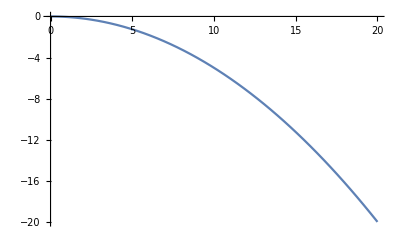

```mathematica
(*Define the crater landscape*)
hc[d_]:=-(1/20)N@(d)^2;
Plot[hc[x],{x,0,l}]
response=hc[Total[#]]&/@ sequences;
```

This landscape has constant local epistasis:

```mathematica
{Mean[#],StandardDeviation[#]}&@Table[Module[{face},face=rf[RandomSample[Range[l]]];
response[[face]].C4.response[[face]]],1000]
```

{0.01,1.52468×10^-16}

### l=20 exponential fractions

```mathematica
l=20;
sequences=Tuples[Range[0,alpha-1],l];
wt=ConstantArray[0,l];
```

```mathematica
hd=HammingDistance[ConstantArray[0,l],#]&/@sequences;
```

```mathematica
mks=Table[Binomial[l,d],{d,0,l}]
```

{1,20,190,1140,4845,15504,38760,77520,125970,167960,184756,167960,125970,77520,38760,15504,4845,1140,190,20,1}

```mathematica
c=.4;
```

```mathematica
pbyd=Table[E^-(c d),{d,0,l}]//N
pbyd[[1]]=0;
```

{1.,0.67032,0.449329,0.301194,0.201897,0.135335,0.090718,0.0608101,0.0407622,0.0273237,0.0183156,0.0122773,0.00822975,0.00551656,0.00369786,0.00247875,0.00166156,0.00111378,0.000746586,0.000500451,0.000335463}

```mathematica
nbyd=Round[pbyd mks]
nbyd//Total
```

{0,13,85,343,978,2098,3516,4714,5135,4589,3384,2062,1037,428,143,38,8,1,0,0,0}

28572

```mathematica
seqs=Table[dp[Table[Permute[PadRight[ConstantArray[1,d],l],RandomPermutation[l]],Round[2 nbyd[[d+1]]]]][[;;nbyd[[d+1]]]],{d,0,l}];
```

```mathematica
tr=seq2pos/@Flatten[seqs,1];
```

```mathematica
y=hc[#]&/@hd[[tr]];
```

```mathematica
f=Cinterp[tr,y]+MapPartialVal[tr,y,alpha^l];
```

```mathematica
faces=Table[Table[Module[{perm},
perm=RandomPermutation[l];
seq2pos[Permute[#,perm]]&/@(Join[PadRight[ConstantArray[1,d],l-2,0],#]&/@{{0,0},{0,1},{1,0},{1,1}})],5000],{d,0,l-2}];
r=Table[Intersection[#,tr]&/@faces[[i]],{i,lg@faces}];//abt
faces2=Table[faces[[i]][[Flatten@Position[r[[i]],{}]]],{i,lg@r}];
facesselect=Table[faces2[[i]][[;;Min[1000,lg@faces2[[i]]]]],{i,1,lg@faces2}];
```

{245.851,Null}

```mathematica
lg/@facesselect
```

{278,393,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000,1000}

```mathematica
test=facesselect//Flatten//dp;
```

```mathematica
elist=Table[Table[Module[{face},
face=facesselect[[i]][[j]];
f[[face[[4]]]]-f[[face[[3]]]]-f[[face[[2]]]]+f[[face[[1]]]]],{j,lg@facesselect[[i]]}],{i,lg@facesselect}];
```

```mathematica
labsize=14;
ticklabsize=14;
padding={{35,10},{30,10}};
pr={{0,l},{hc[20],.5}}
```

{{0,20},{-20.,0.5}}

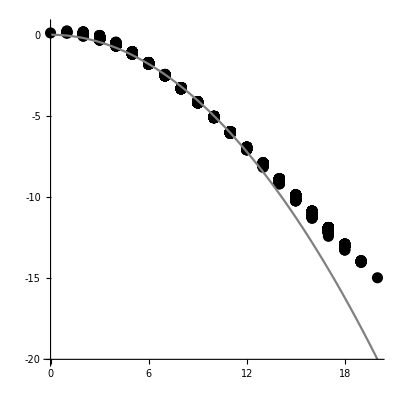
-Graphics-Phenotype
 A

```mathematica
figa=Labeled[Labeled[Show[
ListPlot[Transpose[{Total[#]&/@sequences[[test]],f[[test]]}],PlotRange->pr,BaseStyle->{FontSize->ticklabsize},AspectRatio->1,PlotStyle->{PointSize[.02],Black},Ticks->{{#,Style[Text[#]],{.01,0}}&/@Range[0,l,2],{#,Style[Text[IntegerPart[#]]],{.01,0}}&/@Range[pr[[2]][[1]],pr[[2]][[2]],5]},AxesOrigin->{0,pr[[2]][[1]]},ImageSize->{400,Automatic},PlotRangeClipping->False,ImagePadding->padding],Plot[hc[x],{x,0,l},PlotRange->pr,PlotStyle->Gray]],{"Phenotype"},{Left},LabelStyle->Directive[FontFamily->"Helvetica",FontSize->labsize],RotateLabel->True],{"\n A"},{{Left,Top}},LabelStyle->Directive[FontFamily->"Helvetica",FontSize->labsize+2]]
```

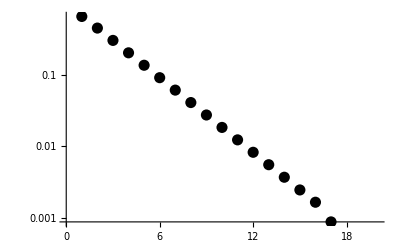
-Graphics-Fraction sampledHamming Distance to WT
 C

```mathematica
figc=Labeled[Labeled[ListLogPlot[Transpose@{Range[0,l],Table[Count[hd[[tr]],d]/Binomial[l,d],{d,0,l}]},PlotRange->{{0,l},All},BaseStyle->{FontSize->ticklabsize},PlotStyle->{PointSize[.02],Black},Ticks->{{#,Style[Text[#]],{.01,0}}&/@Range[0,l,2],Join[{1},{10^#,Style[Text[Superscript[10,#]]],{.01,0}}&/@{-1,-2,-3,-4}]},ImageSize->{400,Automatic},PlotRangePadding->{{0,0},{0,1}}, ImagePadding->padding,PlotRangeClipping->False],{"Fraction sampled","Hamming Distance to WT"},{Left,Bottom},LabelStyle->Directive[FontFamily->"Helvetica",FontSize->labsize],RotateLabel->True],{"\n C"},{{Left,Top}},LabelStyle->Directive[FontFamily->"Helvetica",FontSize->labsize+2]]
```

```mathematica
plotdat=Table[{i,Mean@elist[[i]]},{i,lg@elist}];
```

```mathematica
{Min[#],Max[#]}&@elist
```

{-0.385586,0.248713}

```mathematica
pr={{0,l},{-.3,.1}};
```

#### Mean

```mathematica
pr={{0,l},{-.2,.02}};
```

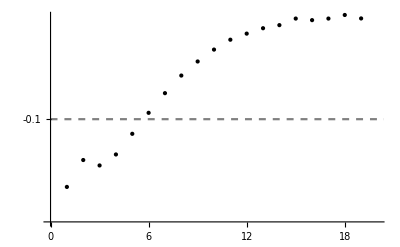
-Graphics-Mean local epistasisB

```mathematica
plotdat=Table[{i,Mean@elist[[i]]},{i,lg@elist}];
figb=Labeled[Labeled[Show[ListPlot[plotdat,PlotRange->pr,BaseStyle->{FontSize->ticklabsize},PlotStyle->{Black,PointSize->.02},Ticks->{{#,Style[Text[#]],{.01,0}}&/@Range[0,l,2],{#,Style[Text[#]],{.01,0}}&/@Range[-.5,.5,.1]/.{0.->0}},ImageSize->{400,Automatic},ImagePadding->padding,AxesOrigin->{0,-.2},PlotRangeClipping->False],Plot[0,{x,0,l+1},PlotStyle->{Gray,Dashed}]],{"Mean local epistasis"},{Left},LabelStyle->Directive[FontFamily->"Helvetica",FontSize->labsize],RotateLabel->True],{"B"},{{Left,Top}},LabelStyle->Directive[FontFamily->"Helvetica",FontSize->labsize+2]]
```

#### Final

```mathematica
Rasterize[Grid[{{figa},{figb},{figc}}],RasterSize->1000];
```

```mathematica
Export["FigureS8.pdf",%]
```